# Squared LTD: e^+ e^- → γ^*→ d d̄ : The quest for α_S/π.

## Global definitions

Resources

Let the integrator always display error message as it provides an estimate of the integral error.

```mathematica
Off[General::stop]
```

```mathematica
$MinPrecision=$MachinePrecision;
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<"./tools/tensTools.m"
<<"./tools/ampTools2.1.m"
```

/Users/valentin/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc

The documented functions in this package are: 
 ?extractTensCoeff
 ?getSymNumericCoeff

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

```mathematica
Needs["Integration`NIntegrateUtilities`"];
```

Facility to create symmetric tensor polynomials

```mathematica
CreateSymmetricPolynomial[externalVars_,loopVars_,Num_,MAXRANK_,IncludeZeros_,replacementRules_]:=Module[
{tensCoefs,symCoeffs,GeVtoPbParam, OverallFactors,NLOOP
},
NLOOP=Length[loopVars];
tensCoefs=extractTensCoeff[{ Num },loopVars,externalVars,0];
symCoeffs=
Table[getSymNumericCoeff[tensCoefs,indices]/.replacementRules,
{indices,
DeleteCases[
Tuples[Flatten[Table[Table[indices, {indices,Sort/@Tuples[{0,1,2,3},rank]//Union}],{rank,0,MAXRANK}],{1,2}],NLOOP],
x_/;Total[Table[Length[inds],{inds,x}]]>MAXRANK
]
}
];
(* always delete coefficients with no value at all, which are those who finish with sym[_] *)
symCoeffs=DeleteCases[symCoeffs,{___,sym[_]}/;True];
(* Then remove zero entries if the user wanted them out *)
If[IncludeZeros,
symCoeffs,
DeleteCases[symCoeffs,x_/;x⟦-1⟧⟦1⟧==0]
]
]
```

Facility to remove all zero coefficients

```mathematica
RemoveZeroCoefficients[coefs_,threshold_]:=Module[{result},
result=DeleteCases[coefs,{___,sym[_]}/;True];
DeleteCases[result,x_/;Abs[x⟦-1⟧⟦1⟧]≤threshold]
]
```

```mathematica
RemoveZeroCoefficients[coefs_]:=RemoveZeroCoefficients[coefs,0]
```

Facility to evaluate symmetric tensor polynomials

```mathematica
EvaluatePolynomial[coefs_,loopmomenta_]:=Module[{},
Total[Table[
Product[
Product[
loopmomenta⟦IcoefsForOneLoop⟧⟦onepower+1⟧
,{onepower,term⟦IcoefsForOneLoop⟧/.{sym[x_]:>x}}]
,{IcoefsForOneLoop,Length[term⟦;;-2⟧]}]*term⟦-1⟧⟦1⟧
,{term,coefs}
]]
]
```

Facility to convert a polynomial into a list of symmetric coefficients

```mathematica
ConvertPolynomialToSymmetricCoefs[polynomial_,LoopMomenta_,MAXRANK_]:=Module[{
ToLorentzReplacementRules
},
ToLorentzReplacementRules=Flatten[Table[
{LoopMomenta⟦iLoop⟧⟦1⟧->SP[k[iLoop],ProjectorE],
LoopMomenta⟦iLoop⟧⟦2⟧->-SP[k[iLoop],ProjectorX],
LoopMomenta⟦iLoop⟧⟦3⟧->-SP[k[iLoop],ProjectorY],
LoopMomenta⟦iLoop⟧⟦4⟧->-SP[k[iLoop],ProjectorZ]
},
{iLoop,Length[LoopMomenta]}
]
];
CreateSymmetricPolynomial[
{ProjectorE,ProjectorX,ProjectorY,ProjectorZ},
Table[k[iLoop] ,{iLoop,Length[LoopMomenta]}],
polynomial/.ToLorentzReplacementRules,
MAXRANK,False,
{
ProjectorE->{1,0,0,0},
ProjectorX->{0,1,0,0},
ProjectorY->{0,0,1,0},
ProjectorZ->{0,0,0,1}
}
]
]
```

Test it!

```mathematica
TestPolynomial=CreateSymmetricPolynomial[{p1,p2},{k,l},SP[k,k]SP[l,p1](SP[k,p2]+SP[l,p2]),4,False,{}];
RemoveZeroCoefficients[TestPolynomial-ConvertPolynomialToSymmetricCoefs[
EvaluatePolynomial[TestPolynomial,{{k0,kx,ky,kz},{l0,lx,ly,lz}}]
,{{k0,kx,ky,kz},{l0,lx,ly,lz}},4]]=={}
```

True

Dot products

```mathematica
LDot[k_List,l_List]:=k⟦1⟧l⟦1⟧-k⟦2⟧l⟦2⟧-k⟦3⟧l⟦3⟧-k⟦4⟧l⟦4⟧
```

```mathematica
VDot[k_List,l_List]:=k⟦1⟧l⟦1⟧+k⟦2⟧l⟦2⟧+k⟦3⟧l⟦3⟧
```

```mathematica
MyPrint[msg_]:=Print[Style[msg,FontFamily->"Monaco"]]
```

```mathematica
Energy[k_List]:=k⟦1⟧
Xcomp[k_List]:=k⟦2⟧
Ycomp[k_List]:=k⟦3⟧
Zcomp[k_List]:=k⟦4⟧
```

```mathematica
GeVtoPbConversion=0.389379304 10^9;
```

```mathematica
SP[x_List,y_List]:=LDot[x,y]
```

Convolution function h(t)

```mathematica
h1[t_,σ_]:=Exp[-t^2/σ^2] 2/(Sqrt[π]σ)
```

```mathematica
Integrate[h1[t,σ],{t,0,∞},Assumptions->{σ>0}]
```

1

This function is however not so nice because it does not go exponentially to zero for small t.

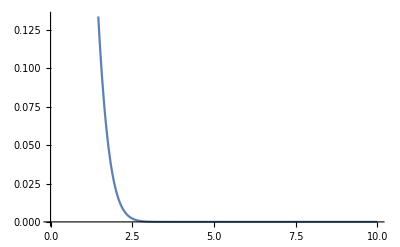

```mathematica
Plot[h1[t,1],{t,0,10}]
```

We will therefore prefer this functional form!

```mathematica
h[t_,σ_]:=Exp[-(σ^2+t^2)/t] 1/(2σ BesselK[1,2σ])
```

```mathematica
ToString[N[2Sqrt[1]BesselK[1,2Sqrt[1]],16],InputForm]
```

0.27973176363304485456919761407082204777`16.

```mathematica
Integrate[h[t,1],{t,0,∞},Assumptions->{σ>0}]
```

1

Test it :

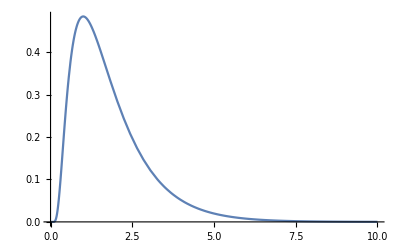

```mathematica
Plot[h[t,1],{t,0,10}]
```

Parametrisations

```mathematica
SphericalMap[x1_,x2_,x3_]:=Module[
{r=x1/(1-x1),θ=x2 π,ϕ=x3 2π,y,drOverdx=1/(x1-1)^2},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)drOverdx r^2 Sin[θ]
|>
]
```

```mathematica
CartesianMap[x1_,x2_,x3_]:=Module[
{Map=y/(1-y)-(1-y)/y,dypOvery=1/y^2+1/(y-1)^2},
<|"vector"->{
Map/.{y->x1},
Map/.{y->x2},
Map/.{y->x3}
},
"jacobian"->(dypOvery/.{y->x1})(dypOvery/.{y->x2})(dypOvery/.{y->x3})
|>
]
```

Test it:

```mathematica
(*Simplify[NIntegrate[If[
((SphericalMap[x1,x2,x3]⟦"vector"⟧⟦1⟧)^2
+(SphericalMap[x1,x2,x3]⟦"vector"⟧⟦2⟧)^2
+(SphericalMap[x1,x2,x3]⟦"vector"⟧⟦3⟧)^2)<4,SphericalMap[x1,x2,x3]⟦"jacobian"⟧,0],
{x1,0,1},{x2,0,1},{x3,0,1}]-4/3 π 8]*)
```

```mathematica
(*Simplify[NIntegrate[If[
((CartesianMap[x1,x2,x3]⟦"vector"⟧⟦1⟧)^2
+(CartesianMap[x1,x2,x3]⟦"vector"⟧⟦2⟧)^2
+(CartesianMap[x1,x2,x3]⟦"vector"⟧⟦3⟧)^2)<4,CartesianMap[x1,x2,x3]⟦"jacobian"⟧,0],
{x1,0,1},{x2,0,1},{x3,0,1}]-4/3 π 8]*)
```

Observables and cuts

Transverse momentum:

```mathematica
ObsPT[k_]:=Sqrt[Xcomp[k]^2+Ycomp[k]^2]
```

Delta R angular separation:

```mathematica
ObsDphi[k_,l_]:=Module[{ptk,ptl,tmp},
ptk=ObsPT[k];
ptl=ObsPT[l];
If[And[ptk==0,ptl==0],10^8,
tmp=(Xcomp[k]Xcomp[l]+Ycomp[k]Ycomp[l])/(ptk ptl);
If[Abs[tmp]>1,If[tmp>0,tmp=1;,tmp=-1;];];
Re[ArcCos[tmp]]
]
]
```

Vectorisable version

```mathematica
NObsDphi[k_,l_]:=Module[{ptk,ptl,tmp},
ptk=ObsPT[k];
ptl=ObsPT[l];
Re[ArcCos[(Xcomp[k]Xcomp[l]+Ycomp[k]Ycomp[l])/(ptk ptl)]]
]
```

```mathematica
ObsEta[k_]:=Module[{pt,pl},
pt=ObsPT[k];
pl=Zcomp[k];
If[And[pt≤10^-5,Abs[pl]≤10^-5],
If[pl≥0,10^8,-10^8],
Re[-Log[Max[Tan[ArcTan[pt,pl]/2],10^-8]]]
]
]
```

Vectorisable version

```mathematica
NObsEta[k_]:=Module[{pt,pl},
pt=ObsPT[k];
pl=Zcomp[k];
Re[-Log[Max[Tan[ArcTan[pt,pl]/2],10^-8]]];
]
```

```mathematica
ObsDR[k_,l_]:=Module[{dEta,dPhi},
dEta=ObsEta[k]-ObsEta[l];
dPhi=ObsDphi[k,l];
Sqrt[dEta^2+dPhi^2]
]
```

Vectorisable version

```mathematica
NObsDR[k_,l_]:=Module[{dEta,dPhi},
dEta=NObsEta[k]-NObsEta[l];
dPhi=NObsDphi[k,l];
Sqrt[dEta^2+dPhi^2]
]
```

And now implement some cuts

```mathematica
Cluster2Jets[ks_,deltaR_]:=Module[{dR12,Jets},
dR12=ObsDR[ks⟦1⟧,ks⟦2⟧];
Jets=If[dR12≤deltaR,
{ks⟦1⟧+ks⟦2⟧},
ks
];
SortBy[Jets,-ObsPT[#]&]
];
Cluster3Jets[ks_,deltaR_]:=Module[{
dR12,dR13,dR23,Jets
},
dR12=ObsDR[ks⟦1⟧,ks⟦2⟧];
dR13=ObsDR[ks⟦1⟧,ks⟦3⟧];
dR23=ObsDR[ks⟦2⟧,ks⟦3⟧];
(*MyPrint["dR12="<>ToString[dR12,InputForm]<>" dR13="<>ToString[dR13,InputForm]<>" dR23="<>ToString[dR23,InputForm]];*)
Jets=Switch[
{dR12≤deltaR,dR13≤deltaR,dR23≤deltaR},
{True,True,True},Cluster2Jets[{ks⟦1⟧+ks⟦2⟧,ks⟦3⟧},deltaR],
{True,True,False},Cluster2Jets[{ks⟦1⟧+ks⟦2⟧,ks⟦3⟧},deltaR],
{True,False,True},Cluster2Jets[{ks⟦1⟧+ks⟦2⟧,ks⟦3⟧},deltaR],
{False,True,True},Cluster2Jets[{ks⟦1⟧+ks⟦3⟧,ks⟦2⟧},deltaR],
{True,False,False},Cluster2Jets[{ks⟦1⟧+ks⟦2⟧,ks⟦3⟧},deltaR],
{False,True,False},Cluster2Jets[{ks⟦1⟧+ks⟦3⟧,ks⟦2⟧},deltaR],
{False,False,True},Cluster2Jets[{ks⟦2⟧+ks⟦3⟧,ks⟦1⟧},deltaR],
{False,False,False},ks,
_,Throw["Should never happen"]
];
SortBy[Jets,-ObsPT[#]&]
];
ClusterJets[ks_,deltaR_]:=Module[
{Jets},
Jets=Switch[
Length[ks],
1,ks,
2,Cluster2Jets[ks,deltaR],
3,Cluster3Jets[ks,deltaR],
_,Throw["Clustering of more than three jets not implemented!"]
];
SortBy[Jets,-ObsPT[#]&]
]
```

Vectorisable versions

```mathematica
NCluster2Jets[ks_,deltaR_]:=Module[{dR12,Jets},
dR12=NObsDR[ks⟦1⟧,ks⟦2⟧];
Jets={ks⟦1⟧+ks⟦2⟧,{0,0,0,0}}HeavisideTheta[deltaR-dR12]+
{ks⟦1⟧,ks⟦2⟧} HeavisideTheta[dR12-deltaR];
{Jets⟦1⟧,Jets⟦2⟧}HeavisideTheta[ObsPT[Jets⟦1⟧]-(ObsPT[Jets⟦2⟧]+10^-8)]+
{Jets⟦2⟧,Jets⟦1⟧}HeavisideTheta[(ObsPT[Jets⟦2⟧]+10^-8)-ObsPT[Jets⟦1⟧]]
];
NCluster3Jets[ks_,deltaR_]:=Module[{
dR12,dR13,dR23,Jets,ptj1,ptj2,ptj3
},
dR12=NObsDR[ks⟦1⟧,ks⟦2⟧];
dR13=NObsDR[ks⟦1⟧,ks⟦3⟧];
dR23=NObsDR[ks⟦2⟧,ks⟦3⟧];
(*MyPrint["dR12="<>ToString[dR12,InputForm]<>" dR13="<>ToString[dR13,InputForm]<>" dR23="<>ToString[dR23,InputForm]];*)
Jets={ks⟦1⟧+ks⟦2⟧,ks⟦3⟧,{0,0,0,0}}HeavisideTheta[deltaR-dR12]HeavisideTheta[dR13-dR12]HeavisideTheta[dR23-dR12]+
{ks⟦1⟧+ks⟦3⟧,ks⟦2⟧,{0,0,0,0}}HeavisideTheta[deltaR-dR13]HeavisideTheta[dR12-dR13]HeavisideTheta[dR23-dR13]+
{ks⟦2⟧+ks⟦3⟧,ks⟦1⟧,{0,0,0,0}}HeavisideTheta[deltaR-dR23]HeavisideTheta[dR12-dR23]HeavisideTheta[dR13-dR23]+
{ks⟦1⟧,ks⟦2⟧,ks⟦3⟧}HeavisideTheta[dR12-deltaR]HeavisideTheta[dR13-deltaR]HeavisideTheta[dR23-deltaR];
(* TODO sort them in PT *)
ptj1=ObsPT[Jets⟦1⟧];
ptj2=ObsPT[Jets⟦2⟧];
ptj3=ObsPT[Jets⟦3⟧];
({Jets⟦1⟧,Jets⟦2⟧,Jets⟦3⟧}HeavisideTheta[ptj2-ptj3]+
{Jets⟦1⟧,Jets⟦3⟧,Jets⟦2⟧}HeavisideTheta[ptj3-ptj2])
HeavisideTheta[ptj1-ptj2]HeavisideTheta[ptj1-ptj3]+
({Jets⟦2⟧,Jets⟦1⟧,Jets⟦3⟧}HeavisideTheta[ptj1-ptj3]+
{Jets⟦2⟧,Jets⟦3⟧,Jets⟦1⟧}HeavisideTheta[ptj3-ptj1])
HeavisideTheta[ptj2-ptj1]HeavisideTheta[ptj2-ptj3]+
({Jets⟦3⟧,Jets⟦1⟧,Jets⟦2⟧}HeavisideTheta[ptj1-ptj2]+
{Jets⟦3⟧,Jets⟦2⟧,Jets⟦1⟧}HeavisideTheta[ptj2-ptj1])
HeavisideTheta[ptj3-ptj2]HeavisideTheta[ptj3-ptj1]
];
```

TestIt:

```mathematica
Cluster3Jets[
{
{1,2,3,4},
{1,2.01,3.01,4.01},
{1,3.1,4.1,5.1}
},0.01
]
```

(2 | 4.01 | 6.01 | 8.01
1 | 3.1 | 4.1 | 5.1)

```mathematica
NCluster2Jets[{
{1,2,3,4},
{1,2.01,3.01,4.01}
},0.01]
```

(2 | 4.01 | 6.01 | 8.01
0 | 0. | 0. | 0.)

```mathematica
NoCut[__]:=1;
```

```mathematica
NoCutFunction=(NoCut[##]&);
```

```mathematica
J1PtCut2[minPT_,maxPT_,deltaR_,
k1_?(VectorQ[#,NumericQ]&),
k2_?(VectorQ[#,NumericQ]&)]:=Module[
{ClusteredJets,ks},
ks={k1,k2};
ClusteredJets=Cluster2Jets[ks,deltaR];
(*Print[ClusteredJets];*)
HeavisideTheta[ObsPT[ClusteredJets⟦1⟧]-minPT]HeavisideTheta[maxPT-ObsPT[ClusteredJets⟦1⟧]]
]
```

```mathematica
J1PtCut3[minPT_,maxPT_,deltaR_,
k1_?(VectorQ[#,NumericQ]&),
k2_?(VectorQ[#,NumericQ]&),
k3_?(VectorQ[#,NumericQ]&)]:=Module[
{ClusteredJets,ks},
ks={k1,k2,k3};
ClusteredJets=Cluster3Jets[ks,deltaR];
(*Print[ClusteredJets];*)
HeavisideTheta[ObsPT[ClusteredJets⟦1⟧]-minPT]HeavisideTheta[maxPT-ObsPT[ClusteredJets⟦1⟧]]
]
```

```mathematica
J3PtCut3[minPT_,maxPT_,deltaR_,
k1_?(VectorQ[#,NumericQ]&),
k2_?(VectorQ[#,NumericQ]&),
k3_?(VectorQ[#,NumericQ]&)]:=Module[
{ClusteredJets,ks},
ks={k1,k2,k3};
ClusteredJets=Join[Cluster3Jets[ks,deltaR],{{0.,0.,0.,0.},{0.,0.,0.,0.}}];
(*Print[ClusteredJets];*)
HeavisideTheta[ObsPT[ClusteredJets⟦3⟧]-minPT]HeavisideTheta[maxPT-ObsPT[ClusteredJets⟦3⟧]]
]
```

Vectorisable version

```mathematica
NJ1PtCut2[minPT_,maxPT_,deltaR_,k1_,k2_]:=Module[
{ClusteredJets,ks},
ks={k1,k2};
(*ClusteredJets=NCluster2Jets[ks,deltaR];*)
ClusteredJets=ks;
(*Print[ClusteredJets];*)
HeavisideTheta[ObsPT[ClusteredJets⟦1⟧]-minPT]HeavisideTheta[maxPT-ObsPT[ClusteredJets⟦1⟧]]
]
```

```mathematica
NJ1PtCut3[minPT_,maxPT_,deltaR_,k1_,k2_,k3_]:=Module[
{ClusteredJets,ks},
ks={k1,k2,k3};
ClusteredJets=NCluster3Jets[ks,deltaR];
(*Print[ClusteredJets];*)
HeavisideTheta[ObsPT[ClusteredJets⟦1⟧]-minPT]HeavisideTheta[maxPT-ObsPT[ClusteredJets⟦1⟧]]
]
```

```mathematica
NJ3PtCut3[minPT_,maxPT_,deltaR_,k1_,k2_,k3_]:=Module[
{ClusteredJets,ks},
ks={k1,k2,k3};
ClusteredJets=NCluster3Jets[ks,deltaR];
(*Print[ClusteredJets];*)
HeavisideTheta[ObsPT[ClusteredJets⟦3⟧]-minPT]HeavisideTheta[maxPT-ObsPT[ClusteredJets⟦3⟧]]
]
```

Test it!

```mathematica
(J1PtCut3[0.1,0.7,0.4,##]&)@@{{1,0.15,0.2,0.0},{1,0.151,0.21,0.0},{1,-0.153,-0.23,0.0}}
(NJ1PtCut3[0.1,0.7,0.4,##]&)@@{{1,0.15,0.2,0.0},{1,0.151,0.21,0.0},{1,-0.153,-0.23,0.0}}
```

1

1

```mathematica
(J1PtCut3[0.2,0.7,0.4,##]&)@@{{1,0.15,0.2,0.0001},{1,0.151,0.21,0.00012},{1,-0.153,-0.23,-0.00013}}
(NJ1PtCut3[0.2,0.7,0.4,##]&)@@{{1,0.15,0.2,0.0001},{1,0.151,0.21,0.00012},{1,-0.153,-0.23,-0.00013}}
```

1

1

Examples

```mathematica
testNumerator={vector[k,mu]vector[l,nu] g[mu,nu]+SP[k,k]+SP[l,l]+SP[k,p]+color1 T[a[1],i[1],i[2]]T[a[2],i[2],i[3]]+color2 T[a[1],i[1],i[2]]T[a[2],i[2],i[1]]+spin1*gamma[s[1],mu,s[2]]*gamma[s[2],mu,s[3]]+spin2 gamma[s[1],mu,s[2]]*gamma[s[2],nu,s[1]]+rank2*SP[k,p]SP[k,p]}
```

{color1 T(a(1),i(1),i(2)) T(a(2),i(2),i(3))+color2 T(a(1),i(1),i(2)) T(a(2),i(2),i(1))+g(mu,nu) vector(k,mu) vector(l,nu)+spin2 gamma(s(1),mu,s(2)) gamma(s(2),nu,s(1))+spin1 gamma(s(1),mu,s(2)) gamma(s(2),mu,s(3))+rank2 (SP(k,p))^2+SP(k,p)+SP(k,k)+SP(l,l)}

```mathematica
testNumeratorContracted=contractSpin[contractColor[testNumerator,i,a],{k,l,p}]
```

{color1 T(a(1),a(2),i(1),i(3))+color2 TF delta(a(1),a(2))+d spin1 delta(s(1),s(3))+4 spin2 g(mu,nu)+SP(k,l)+rank2 (SP(k,p))^2+SP(k,p)+SP(k,k)+SP(l,l)}

```mathematica
contractSpin[contractColor[
SP[k,p]vector[l,mu] gamma[s[2],mu,s[3]] vector[l,mu] gamma[s[3],mu,s[4]]
,i,a]{k,l,p}]
```

contractSpin({k gamma(s(2),mu,s(3)) gamma(s(3),mu,s(4)) SP(k,p) (vector(l,mu))^2,l gamma(s(2),mu,s(3)) gamma(s(3),mu,s(4)) SP(k,p) (vector(l,mu))^2,p gamma(s(2),mu,s(3)) gamma(s(3),mu,s(4)) SP(k,p) (vector(l,mu))^2})

```mathematica
tensCoeff=extractTensCoeff[testNumeratorContracted,{k,l},{p}]
```

Final check started

Final check passed

{({0,0} | {color1 T(a(1),a(2),i(1),i(3))+color2 TF delta(a(1),a(2))+d spin1 delta(s(1),s(3))+4 spin2 g(mu,nu)}),({1,0} | {vector(p,lInd1(1))}
{0,1} | {0}),({2,0} | {g(lInd1(1),lInd1(2))+rank2 vector(p,lInd1(1)) vector(p,lInd1(2))}
{1,1} | {g(lInd1(1),lInd2(1))}
{0,2} | {g(lInd2(1),lInd2(2))})}

```mathematica
testNumeratorContracted//InputForm
```

{color2*TF*delta[a[1], a[2]] + d*spin1*delta[s[1], s[3]] + 4*spin2*g[mu, nu] + SP[k, k] + SP[k, l] + SP[k, p] + 
  rank2*SP[k, p]^2 + SP[l, l] + color1*T[a[1], a[2], i[1], i[3]]}

```mathematica
tensCoeff=extractTensCoeff[{testNumeratorContracted},{k,l},{p},0]
```

{({0,0} | (color1 T(a(1),a(2),i(1),i(3))+color2 TF delta(a(1),a(2))+d spin1 delta(s(1),s(3))+4 spin2 g(mu,nu))),({1,0} | (vector(p,lInd1(1)))
{0,1} | (0)),({2,0} | (g(lInd1(1),lInd1(2))+rank2 vector(p,lInd1(1)) vector(p,lInd1(2)))
{1,1} | (g(lInd1(1),lInd2(1)))
{0,2} | (g(lInd2(1),lInd2(2))))}

```mathematica
(* rank 0 *)
getSymNumericCoeff[tensCoeff,{{},{}}]
```

{sym({}),sym({}),(color1 T(a(1),a(2),i(1),i(3))+color2 TF delta(a(1),a(2))+d spin1 delta(s(1),s(3))+4 spin2 g(mu,nu))}

A + B^μ k^μ+C^(μ ν ρ)k^μ k^ν l^ρ

A, B^0,B^1,...., C^00,C^01,C^10

```mathematica
(* symbolic *)
getSymNumericCoeff[tensCoeff,{{1},{}}] (*k^1*)
getSymNumericCoeff[tensCoeff,{{2},{}}] (*k^2*)
```

{sym({1}),sym({}),(vector(p,1))}

{sym({2}),sym({}),(vector(p,2))}

```mathematica
(* numeric *)
p={1,2,3,4};
getSymNumericCoeff[tensCoeff,{{1},{}}] (*k^1-> gives Subscript[p, 1]*)
getSymNumericCoeff[tensCoeff,{{2},{}}] (*k^2-> gives Subscript[p, 2]*)
ClearAll[p]
```

{sym({1}),sym({}),(-2)}

{sym({2}),sym({}),(-3)}

```mathematica
getSymNumericCoeff[tensCoeff,{{1},{1}}](* k^1 l^1*)
getSymNumericCoeff[tensCoeff,{{1},{2}}](* k^1 l^2*)
```

{sym({1}),sym({1}),(-1)}

{sym({1}),sym({2}),(0)}

```mathematica
getSymNumericCoeff[tensCoeff,{{1,1},{}}] (* k^1 k^1-> gives g[1,1]*)
getSymNumericCoeff[tensCoeff,{{1,2},{}}] (* k^1 k^1-> gives g[1,2]*)
```

{sym({1,1}),sym({}),(rank2 (vector(p,1))^2-1)}

{sym({1,2}),sym({}),(2 rank2 vector(p,1) vector(p,2))}

## Leading Order

We are interested in the one supergraph contributing to e^+ e^- → γ^*→ d d̄ at leading order. We will work in the rest frame where of the off-shell photon, that is Q^μ=(Q^0,0,0,0), p_1^μ=(Q^0/2,0,0,Q^0/2) and p_1^μ=(Q^0/2,0,0,-Q^0/2).

-Graphics-

Let’s now write down the integrand for this super graph

```mathematica
LOLeftNum[p1_,p2_,k_,Qe_,ge_,Qq_,gs_,δ_]:=(
(-ⅈ Qe ge) gamma[s[11],mu11,s[12]]delta[i[13],i[14]]
(-ⅈ g[mu11,mu12])
(-ⅈ Qq ge)gamma[s[13],mu12,s[14]]
)
```

```mathematica
LORightNum[p1_,p2_,k_,Qe_,ge_,Qq_,gs_,δ_]:=(
(ⅈ Qq ge)gamma[s[24],mu21,s[23]]delta[i[24],i[23]]
(ⅈ g[mu21,mu22])
(ⅈ Qe ge) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
LOPrefactors[p1_,p2_,k_]:=1/(2 2)
```

```mathematica
LONumerator[p1_,p2_,k_,Qe_,ge_,Qq_,gs_,δ_]:=contractColor[contractSpin[
(
LOLeftNum[p1,p2,k,Qe,ge,Qq,gs,δ]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[14],mu3,s[24]]vector[k,mu3])delta[i[14],i[24]]
(gamma[s[23],mu4,s[13]](vector[p1,mu4]+vector[p2,mu4]-vector[k,mu4]))delta[i[23],i[13]]
LORightNum[p1,p2,k,Qe,ge,Qq,gs,δ]
)
,{p1,p2,k}],i,a]
```

```mathematica
(*extractTensCoeff[{LONumerator[p1,p2,k,Qe,ge,Qq,gs,δ]},{k},{p1,p2}]*)
```

```mathematica
LOExpression[p1_,p2_,k_]:=Module[
{LONum,
ge=N[Sqrt[4π 1/132.507]],Qe=1,Qq=1/3,gs=N[Sqrt[4π 0.118]],δ=0},
LONum = LONumerator[p1,p2,k,Qe,ge,Qq,gs,δ]/.{
SP[k,k]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0,d->4,Nc->3,TF->1/2
};
LOPrefactors[p1,p2,k](1/SP[p1+p2,p1+p2])LONum(1/SP[p1+p2,p1+p2]) 
]
```

```mathematica
LOExpression[p1_List,p2_List,k_List]=LOExpression[p1,p2,k]
```

((0.0959336+0. ⅈ) SP(k,p2) SP(p1,p2)+(0.0959336+0. ⅈ) SP(k,p1) SP(p1,p2)+(-0.191867+0. ⅈ) SP(k,p1) SP(k,p2)+(0.+0. ⅈ))/(4 (SP(p1+p2,p1+p2))^2)

The 1/ⅈundoes the ⅈ from the Cutkosky cut and seems necessary.

```mathematica
LOIntegrand[p1_List,p2_List,k_List]:=GeVtoPbConversion(1/-ⅈ)^2 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[k]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])LOExpression[p1,p2,k]
```

Now extract the numerator coefficients for the squared LTD implementation of the above

```mathematica
RustLTDNumeratorLOCoefs[p1_,p2_]:=Module[
{LONum,tensCoefs,symCoeffs,
GeVtoPbParam,geParam,QeParam, QqParam,gsParam,k,p1Param,p2Param,
ge=N[Sqrt[4π 1/132.507]], Qe=1, Qq=1/3,gs=N[Sqrt[4π 0.118]],δ=0
},
LONum = LONumerator[p1Param,p2Param,k,QeParam,geParam,QqParam,gsParam,δ]/.{
SP[k,k]:>0,SP[p1Param,p1Param]:>0,SP[p2Param,p2Param]:>0
};
tensCoefs=extractTensCoeff[{ GeVtoPbParam(1/-ⅈ)^2 LONum },{k},{p1Param,p2Param}];
symCoeffs=
Table[getSymNumericCoeff[tensCoefs,indices]/.{
GeVtoPbParam->GeVtoPbConversion,
p1Param->p1,
p2Param->p2,
QeParam->Qe,
QqParam->Qq,
gsParam-> gs,
geParam->ge,
d->4,Nc->3,TF->1/2
},
{indices,{
{{}},
{{0}},{{1}},{{2}},{{3}},
{{0,0}},{{0,1}},{{0,2}},{{0,3}},{{1,1}},{{1,2}},{{1,3}},{{2,2}},{{2,3}},{{3,3}}
}}
];
symCoeffs
]
```

```mathematica
RustLONumerators=RustLTDNumeratorLOCoefs[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0}]
```

Final check started

Final check passed

(sym({}) | {0}
sym({0}) | {-1.49418×10^8}
sym({1}) | {0.}
sym({2}) | {0.}
sym({3}) | {0.}
sym({0,0}) | {7.47091×10^7}
sym({0,1}) | {0.}
sym({0,2}) | {0.}
sym({0,3}) | {0.}
sym({1,1}) | {0.}
sym({1,2}) | {0.}
sym({1,3}) | {0.}
sym({2,2}) | {0.}
sym({2,3}) | {0.}
sym({3,3}) | {-7.47091×10^7})

Test the LO ME on a benchmark point produced by MG5:

```mathematica
LOExpressionBenchmarkMG5=3.4754514769164153*^-03;
LOExpressionLTD=LOExpression[
{500.0,0.,0.,500.},
{500.0,0.,0.,-500.},
{500.0,110.9242844438328,444.8307894881214,-199.55292993087878}
];
RelativeDiscrepancy=Abs[(LOExpressionLTD-LOExpressionBenchmarkMG5)/LOExpressionBenchmarkMG5]
Print["Relative discrepancy in of the LO ME: "<>ToString[RelativeDiscrepancy*100]<>" %."];
```

1.24784×10^-16

Relative discrepancy in of the LO ME:           -14
1.24784 10 %.

Now the procedure for solving the rescaling delta

```mathematica
LORescalingSolutionParametric=Solve[
FullSimplify[Sqrt[t^2 INkdotk]+Sqrt[t^2 INkdotk]-INQ0==0,
Assumptions->{t>0,INkdotk>0,INQ0>0}],{t}
];
LORescalingSolutionParametricJacobian=
Abs[(D[FullSimplify[Sqrt[t^2 INkdotk]+Sqrt[t^2 INkdotk]-INQ0,
Assumptions->{t>0,INkdotk>0,INQ0>0}],t])/.{t->LORescalingSolutionParametric}];
LORescalingSolution[Q0_,kvec_]:=(LORescalingSolutionParametric/.{INkdotk->VDot[kvec,kvec],INQ0->Q0})
LORescalingSolutionJacobian[Q0_,kvec_]:=Abs[(LORescalingSolutionParametricJacobian/.{INkdotk->VDot[kvec,kvec],INQ0->Q0})]
```

We can now proceed with the integration

```mathematica
LOIntegrandFunction[xs_,p1_,p2_,DEBUG_,OptionsPattern[Cut->(NoCut[##]&)]]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
jacobian=1,Integrand=1,bubble,kvec,k0,Q0,kmu,QMinuskmu,l0,rescaling,rescalingJacobian,
δ=0,λ=1,σ,cutFunction=OptionValue[Cut]
},
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
Q0=Energy[p1]+Energy[p2];
σ=Q0;
rescaling=(t/.LORescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=LORescalingSolutionJacobian[Q0,kvec];
kvec=rescaling*kvec;
k0=Sqrt[VDot[kvec,kvec]];
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
QMinuskmu={Q0-k0,-kvec⟦1⟧,-kvec⟦2⟧,-kvec⟦3⟧};
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
Integrand=Integrand*LOIntegrand[p1,p2,kmu];
If[DEBUG,Print["LO Integrand="<>ToString[LOIntegrand[p1,p2,kmu]]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^3);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^3="<>ToString[rescaling^3]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]cutFunction[kmu,QMinuskmu]
]
```

Test the integrand now

```mathematica
LOIntegrandFunction[{0.4,0.2,0.3},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True,Cut->(NoCut[##]&)]
```

rescaling=1.5

kmu=(1.,{-0.181636, 0.559017, 0.809017})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

LO Integrand=1528.81 + 0. I

h[rescaling,σ]=0.421118

rescaling^3=3.375

1/(rescaling jacobian)=0.75

jacobian=14.324

Integrand=23342.9 + 0. I

23342.9

```mathematica
LOIntegrandFunction[{0.99999,1.0,1.0},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True,Cut->(NJ1PtCut2[0.3,0.5,0.4,##]&)]
```

rescaling=0.0000100001

kmu=(1.,           -16             -32
{1.22465 10   , -2.99952 10   , -1.})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

LO Integrand=1848.05 + 0. I

h[rescaling,σ]=0.56419

rescaling^3=          -15
1.00003 10

1/(rescaling jacobian)=          -6
5.00005 10

jacobian=241731.

Integrand=          -12
1.26025 10    + 0. I

0.

Now integrate that LO contribution

```mathematica
ClearAll[ThisIntegrand,CutFunction];
CutFunction=(NJ1PtCut2[0.2,0.8,0.4,##]&);
ThisIntegrand[x1,x2,x3]=LOIntegrandFunction[{x1,x2,x3},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,Cut->NoCutFunction];
(*MCPoints={};*)
rBoundMin=0.0+10^-5;rBoundMax=1.0-10^-5;
BoundMin=0.0+10^-5;BoundMax=1.0-10^-5;
IntermediateResult=0;
LOResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3},RealCutRescalingIntegrand[{x1,x2,x3},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics,{1000,5000,10000,50000,100000,500000,1000000}}]
]
```

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 8172.11 and 189.038 for the integral and error estimates.

Result for 1000 sample points: 8172.11

NIntegrate::maxp: The integral failed to converge after 5100 integrand evaluations. NIntegrate obtained 7667.1 and 82.4873 for the integral and error estimates.

Result for 5000 sample points: 7667.1

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 7763.13 and 32.3744 for the integral and error estimates.

Result for 10000 sample points: 7763.13

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 7740.25 and 4.40886 for the integral and error estimates.

Result for 50000 sample points: 7740.25

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 7746.2 and 5.02549 for the integral and error estimates.

Result for 100000 sample points: 7746.2

Result for 500000 sample points: 7742.5

Result for 1000000 sample points: 7741.96

<|1000→8172.11,5000→7667.1,10000→7763.13,50000→7740.25,100000→7746.2,500000→7742.5,1000000→7741.96|>

```mathematica
FinalLOResult = LOResults[Max[Keys[LOResults]]]
```

7741.96

Cross-section :  ( 0.7744 +- 0.0004323 pb )*100

```mathematica
LOResultBenchmark=7744.0;
```

```mathematica
LOResultRelDiff=Abs[(FinalLOResult-LOResultBenchmark)/LOResultBenchmark]*100.0
```

0.0263197

## Next-to-Leading Order

We are interested in the two supergraphs contributing to e^+ e^- → γ^*→ d d̄ at next-to-leading order.
We will work in the rest frame where of the off-shell photon, that is Q^μ=(Q^0,0,0,0), p_1^μ=(Q^0/2,0,0,Q^0/2) and p_1^μ=(Q^0/2,0,0,-Q^0/2).

For clarity we regroup here all couplings:

```mathematica
AllNLOCouplings=gs^2 ge^4 Qd^2 Qe^2;
```

```mathematica
NumericalValues={
ge->N[Sqrt[4π 1/(132.507`16)]],
gs->N[Sqrt[4π 0.118`16]],
Qe->1,Qd->1/3,d->4,Nc->3,TF->1/2
};
```

Nested Bubble

## Real-emission bubble (RBubble)

-Graphics-

### Direct computation

Let’s now write down the integrand for this super graph

```mathematica
RBubbleLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
(ⅈ gamma[s[14],mu13,s[15]] vector[k,mu13] )
(-ⅈ) gamma[s[15],mu14,s[16]] T[a[11],i[14],i[15]]
)
```

```mathematica
RBubbleRightNum[p1_,p2_,k_,l_]:=(
(ⅈ)gamma[s[26],mu24,s[25]] T[a[21],i[25],i[24]]
(-ⅈ gamma[s[25],mu23,s[24]] vector[k,mu23] )
(ⅈ )gamma[s[24],mu21,s[23]]delta[i[24],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

```mathematica
RBubbleLeftNumSoper[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
)
```

```mathematica
RBubbleRightNumSoper[p1_,p2_,k_,l_]:=(
(ⅈ )gamma[s[24],mu21,s[23]]delta[i[24],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
RBubbleMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK(?) but does not reproduce the matrix element

```mathematica
RBubbleNumerator[p1_,p2_,k_,l_]:=contractColor[contractSpin[
(
RBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[16],mu3,s[26]]vector[l,mu3])delta[i[15],i[25]]
(-g[mu24,mu14])delta[a[11],a[21]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
RBubbleRightNum[p1,p2,k,l]
)
,{p1,p2,k,l}],i,a]
```

Below we also capture the +(k^μ(k̄)^ν+ (k̄)^μ k^ν)/(k ·k̄) piece of the sum over polarisations, with (k̄)^μ=2(k ·n)n^μ-k^μ, with n^μ=(1,0,0,0).
This piece will only be used for comparing against the ME.

```mathematica
RBubbleNumeratorUnphysical[p1_,p2_,k_,l_,lmkbar_]:=contractColor[contractSpin[
(
RBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[16],mu3,s[26]]vector[l,mu3])delta[i[15],i[25]]
(+(((vector[k,mu24]-vector[l,mu24])vector[lmkbar,mu14]+vector[lmkbar,mu24](vector[k,mu14]-vector[l,mu14]))/(SP[k,lmkbar]-SP[l,lmkbar])))delta[a[11],a[21]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
RBubbleRightNum[p1,p2,k,l]
)
,{p1,p2,k,l,lmkbar}],i,a]
```

```mathematica
RBubbleME[p1_,p2_,k_,l_]:=Module[
{MENum },
MENum =( (RBubbleMEPrefactors[p1,p2,k,l]
(1/SP[p1+p2,p1+p2] 1/SP[k,k])RBubbleNumerator[p1,p2,k,l](1/SP[p1+p2,p1+p2] 1/SP[k,k]) )/.{
SP[l,l]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues;
MENum
]
```

```mathematica
RBubbleME[p1_List,p2_List,k_List,l_List]=RBubbleME[p1,p2,k,l];
```

```mathematica
RBubbleMEUnphysical[p1_,p2_,k_,l_]:=Module[
{MENum ,lmkbar},
MENum =(( (MEPrefactors[p1,p2,k,l]
(1/SP[p1+p2,p1+p2] 1/SP[k,k])RBubbleNumeratorUnphysical[p1,p2,k,l,lmkbar](1/SP[p1+p2,p1+p2] 1/SP[k,k]) )/.{
SP[l,l]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues)/.{
lmkbar->{
(Energy[k]-Energy[l]),-(Xcomp[k]-Xcomp[l]),-(Ycomp[k]-Ycomp[l]),-(Zcomp[k]-Zcomp[l])}
};
MENum
]
```

```mathematica
RBubbleMEUnphysical[p1_List,p2_List,k_List,l_List]=RBubbleMEUnphysical[p1,p2,k,l];
```

```mathematica
RBubbleMESoper[p1_,p2_,k_,l_,DEBUG_]:=Module[
{kvec,lvec,lSopervec,qvec,q0,kplus,kminus,ME},
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
lSopervec=lvec-1/2 kvec;
q0=Energy[k];
qvec=-kvec;
kminus=1/2 qvec-lSopervec;
kplus=1/2 qvec+lSopervec;
If[DEBUG,MyPrint["BUBBLE FACTOR :: q0="<>ToString[q0]]];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Sqrt[VDot[kminus, kminus]]="<>ToString[Sqrt[VDot[kminus, kminus]]]]];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Sqrt[VDot[kplus, kplus]]="<>ToString[Sqrt[VDot[kplus, kplus]]]]];
If[DEBUG,MyPrint["BUBBLE FACTOR :: VDot[qvec, qvec]="<>ToString[VDot[qvec, qvec]]]];
If[DEBUG,MyPrint["BUBBLE FACTOR :: qbar^2="<>ToString[(Sqrt[VDot[kminus, kminus]]+Sqrt[VDot[kplus, kplus]])^2-VDot[qvec, qvec]]]];
ME =(( (RBubbleMEPrefactors[p1,p2,k,l](1/SP[p1+p2,p1+p2])
4/3(1/(2(Sqrt[VDot[kminus, kminus]]+Sqrt[VDot[kplus, kplus]])))(4)(1/((Sqrt[VDot[kminus, kminus]]+Sqrt[VDot[kplus, kplus]])^2-VDot[qvec, qvec]))
(
contractColor[contractSpin[
(
RBubbleLeftNumSoper[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(
(q0 Sqrt[VDot[kplus, kplus]] gamma[s[14],muX1,s[24]] vector[EnergyVector,muX1])
-((Sqrt[VDot[kplus, kplus]]+Sqrt[VDot[kminus, kminus]])gamma[s[14],muX2,s[24]]vector[kplusspace,muX2])
)delta[i[14],i[24]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
RBubbleRightNumSoper[p1,p2,k,l]
)
,{p1,p2,k,l,kplusspace,EnergyVector}],i,a]
)
(1/SP[p1+p2,p1+p2]) )/.{
SP[p1,p1]:>0,SP[p2,p2]:>0,EnergyVector->{1,0,0,0},kplusspace->{0,kplus⟦1⟧,kplus⟦2⟧,kplus⟦3⟧}})/.NumericalValues);
If[DEBUG,MyPrint["BUBBLE FACTOR :: ME="<>ToString[ME,InputForm]];];
ME
];
```

```mathematica
RBubbleMESoper[p1_List,p2_List,k_List,l_List]=RBubbleMESoper[p1,p2,k,l,False];
```

```mathematica
RBubbleMEBenchmarkMG5=5.4611133073987217*^-9;
TestPSPoint={
{500.0,0.,0.,500.},
{500.0,0.,0.,-500.},
{0.45857878788544019*^3, 0.16945322030967981*^3, 0.37965366207819869*^3,-0.19350247465025248*^3},
{0.36406662073681781*^3,-0.18329869293191848*^2,-0.34770430131936712*^3, 0.10634960775870815*^3}
};
AppendTo[TestPSPoint,Total[TestPSPoint⟦;;2⟧]-Total[TestPSPoint⟦3;;4⟧]];
RBubbleMELTD=RBubbleME[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
RBubbleMELTDUnphysical=RBubbleMEUnphysical[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
RBubbleMELTDSoper=RBubbleMESoper[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
ClearAll[TestPSPoint];
MyPrint[""];
MyPrint["Test PS point A"];
MyPrint["---------------"];
MyPrint["RBubble benchmark      : "<>ToString[RBubbleMEBenchmarkMG5,InputForm]];
MyPrint["RBubble LTD Soper      : "<>ToString[RBubbleMELTDSoper,InputForm]];
MyPrint["LTDSoper/benchmark     : "<>ToString[RBubbleMELTDSoper/RBubbleMEBenchmarkMG5,InputForm]];
MyPrint["RBubble LTD            : "<>ToString[RBubbleMELTD,InputForm]];
MyPrint["LTDSoper/RBubbleLTD    : "<>ToString[RBubbleMELTDSoper/RBubbleMELTD,InputForm]];
MyPrint["RBubble LTD Unphysical : "<>ToString[RBubbleMELTDUnphysical,InputForm]];
MyPrint["LTD/benchmark Ratio    : "<>ToString[(RBubbleMELTD+RBubbleMELTDUnphysical)/RBubbleMEBenchmarkMG5,InputForm]];
RelativeDiscrepancy=Abs[(RBubbleMELTD+RBubbleMELTDUnphysical-RBubbleMEBenchmarkMG5)/RBubbleMEBenchmarkMG5];
MyPrint["Relative discrepancy in of the LO ME: "<>ToString[RelativeDiscrepancy*100,InputForm]<>" %."];
MyPrint[""];
RBubbleMEBenchmarkMG5=3.7555340149497745*^-8;
TestPSPoint={
{500.0,0.,0.,500.},
{500.0,0.,0.,-500.},
{0.49515339207738344*^3, 0.18672291576921197*^3, 0.31968357808502418*^3,-0.32880669749130601*^3},
{0.10267791387500911*^3,-0.70620427307722238*^2,-0.43455952956966151*^2, 0.60556497563849021*^2}
};
AppendTo[TestPSPoint,Total[TestPSPoint⟦;;2⟧]-Total[TestPSPoint⟦3;;4⟧]];
RBubbleMELTD=RBubbleME[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
RBubbleMELTDUnphysical=RBubbleMEUnphysical[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
RBubbleMELTDSoper=RBubbleMESoper[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
ClearAll[TestPSPoint];
MyPrint["Test PS point B"];
MyPrint["---------------"];
MyPrint["RBubble benchmark      : "<>ToString[RBubbleMEBenchmarkMG5,InputForm]];
MyPrint["RBubble LTD Soper      : "<>ToString[RBubbleMELTDSoper,InputForm]];
MyPrint["LTDSoper/benchmark     : "<>ToString[RBubbleMELTDSoper/RBubbleMEBenchmarkMG5,InputForm]];
MyPrint["RBubble LTD            : "<>ToString[RBubbleMELTD,InputForm]];
MyPrint["LTDSoper/RBubbleLTD    : "<>ToString[RBubbleMELTDSoper/RBubbleMELTD,InputForm]];
MyPrint["RBubble LTD Unphysical : "<>ToString[RBubbleMELTDUnphysical,InputForm]];
MyPrint["LTD/benchmark Ratio    : "<>ToString[(RBubbleMELTD+RBubbleMELTDUnphysical)/RBubbleMEBenchmarkMG5,InputForm]];
RelativeDiscrepancy=Abs[(RBubbleMELTD+RBubbleMELTDUnphysical-RBubbleMEBenchmarkMG5)/RBubbleMEBenchmarkMG5];
MyPrint["Relative discrepancy in of the LO ME: "<>ToString[RelativeDiscrepancy*100,InputForm]<>" %."];
MyPrint[""];
```

Test PS point A

---------------

RBubble benchmark      : 5.461113307398722*^-9

RBubble LTD Soper      : 4.063616813779451*^-9

LTDSoper/benchmark     : 0.7441004397901906

RBubble LTD            : 4.063616813779445*^-9

LTDSoper/RBubbleLTD    : 1.0000000000000016

RBubble LTD Unphysical : 3.77241333485338*^-6*MEPrefactors[{500., 0., 0., 500.}, {500., 0., 0., -500.}, {822.645408622258, 151.12335101648796, 31.949360758831574, -87.15286689154433}, {458.5787878854402, 169.4532203096798, 379.6536620781987, -193.50247465025248}]

LTD/benchmark Ratio    : 1.831128459915305*^8*(4.063616813779445*^-9 + 3.77241333485338*^-6*MEPrefactors[{500., 0., 0., 500.}, {500., 0., 0., -500.}, {822.645408622258, 151.12335101648796, 31.949360758831574, -87.15286689154433}, {458.5787878854402, 169.4532203096798, 379.6536620781987, -193.50247465025248}])

Relative discrepancy in of the LO ME: 1.831128459915305*^10*Abs[-1.3974964936192771*^-9 + 3.77241333485338*^-6*MEPrefactors[{500., 0., 0., 500.}, {500., 0., 0., -500.}, {822.645408622258, 151.12335101648796, 31.949360758831574, -87.15286689154433}, {458.5787878854402, 169.4532203096798, 379.6536620781987, -193.50247465025248}]] %.

Test PS point B

---------------

RBubble benchmark      : 3.7555340149497745*^-8

RBubble LTD Soper      : 6.0706263991135124*^-9

LTDSoper/benchmark     : 0.16164482534169508

RBubble LTD            : 6.070626399113435*^-9

LTDSoper/RBubbleLTD    : 1.0000000000000129

RBubble LTD Unphysical : 0.00008499009087914699*MEPrefactors[{500., 0., 0., 500.}, {500., 0., 0., -500.}, {597.8313059523925, 116.10248846148973, 276.22762512805804, -268.250199927457}, {495.15339207738344, 186.72291576921197, 319.6835780850242, -328.806697491306}]

LTD/benchmark Ratio    : 2.6627371660575245*^7*(6.070626399113435*^-9 + 0.00008499009087914699*MEPrefactors[{500., 0., 0., 500.}, {500., 0., 0., -500.}, {597.8313059523925, 116.10248846148973, 276.22762512805804, -268.250199927457}, {495.15339207738344, 186.72291576921197, 319.6835780850242, -328.806697491306}])

Relative discrepancy in of the LO ME: 2.6627371660575247*^9*Abs[-3.148471375038431*^-8 + 0.00008499009087914699*MEPrefactors[{500., 0., 0., 500.}, {500., 0., 0., -500.}, {597.8313059523925, 116.10248846148973, 276.22762512805804, -268.250199927457}, {495.15339207738344, 186.72291576921197, 319.6835780850242, -328.806697491306}]] %.

The 1/ⅈundoes the ⅈ from the Cytotoxic cut and seems necessary.

```mathematica
RBubbleIntegrand[p1_List,p2_List,k_List,l_List]:=Module[{},
GeVtoPbConversion(1/-ⅈ)^3 1/(2π)^8 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[l]])(-2π ⅈ)/(2Abs[Energy[k]-Energy[l]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])RBubbleME[p1,p2,k,l]
]
```

```mathematica
RBubbleRescalingSolutionParametric=Solve[
FullSimplify[Sqrt[t^2 INldotl]+Sqrt[t^2 INlkdotlk]+Sqrt[t^2 INkdotk]-INQ0==0,
Assumptions->{t>0,INkdotk>0,INlkdotlk>0,INldotl>0,INQ0>0}],{t}
];
RBubbleRescalingSolutionParametricJacobian=
Abs[(D[FullSimplify[Sqrt[t^2 INldotl]+Sqrt[t^2 INlkdotlk]+Sqrt[t^2 INkdotk]-INQ0,
Assumptions->{t>0,INkdotk>0,INlkdotlk>0,INldotl>0,INQ0>0}],t])/.{t->RBubbleRescalingSolutionParametric}];
RBubbleRescalingSolution[Q0_,kvec_,lvec_]:=(RBubbleRescalingSolutionParametric/.{INldotl->VDot[lvec,lvec],INlkdotlk->VDot[kvec-lvec,kvec-lvec],INkdotk->VDot[-kvec,-kvec],INQ0->Q0})
RBubbleRescalingSolutionJacobian[Q0_,kvec_,lvec_]:=(RBubbleRescalingSolutionParametricJacobian/.{INldotl->VDot[lvec,lvec],INlkdotlk->VDot[kvec-lvec,kvec-lvec],INkdotk->VDot[-kvec,-kvec],INQ0->Q0})
```

```mathematica
RBubbleIntegrandFunction[xs_,p1_,p2_,DEBUG_,SHIFTED_,OptionsPattern[Cut->(NoCut[##]&)]]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,QMinuskmu,kmlmu,
rescaling,rescalingJacobian,Q0,σ,cutFunction=OptionValue[Cut]
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
(* Apply shift if asked for *)
lvec=If[SHIFTED,lvec+1/2 kvec,lvec];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.RBubbleRescalingSolution[Q0,lvec,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=RBubbleRescalingSolutionJacobian[Q0,lvec,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
l0=Sqrt[VDot[lvec,lvec]];
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
QMinuskmu={Q0-k0,-kvec⟦1⟧,-kvec⟦2⟧,-kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
kmlmu=kmu-lmu;
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|l|+|l-k|+|k|="<>ToString[Sqrt[VDot[lvec,lvec]]+Sqrt[VDot[lvec-kvec,lvec-kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|l-k|="<>ToString[Sqrt[VDot[lvec-kvec,lvec-kvec]]]<>" vs -(l0-k0)="<>ToString[-(l0-k0)]]];
If[DEBUG,Print["|l|="<>ToString[Sqrt[VDot[lvec,lvec]]]<>" vs l0="<>ToString[l0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs -(k0-Q0)="<>ToString[-(k0-Q0)]]];
Integrand=Integrand*RBubbleIntegrand[p1,p2,kmu,lmu];
If[DEBUG,MyPrint["RBubbleME="<>ToString[RBubbleME[p1,p2,kmu,lmu],InputForm]];];
If[DEBUG,MyPrint["(1/Eb1)*(1/Eb2)="<>ToString[1/Abs[Energy[lmu]] 1/Abs[Energy[kmu]-Energy[lmu]],InputForm]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
If[DEBUG,MyPrint["Integrand*jac="<>ToString[Integrand*jacobian,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]cutFunction[lmu,kmlmu,QMinuskmu]
]
```

Test the integrand now

```mathematica
RBubbleIntegrandFunction[{0.1,0.2,0.3,0.4,0.5,0.6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True,False]
```

xs={0.1, 0.2, 0.3, 0.4, 0.5, 0.6}

rescaling=1.35753

lmu=(0.905021,                                 -17
{-0.732177, -0.531958, 5.54165 10   })

kmu=(1.84916,{-0.0273973, 0.0843203, 0.12203})

-lmu+kmu=(0.944142,{0.70478, 0.616278, 0.12203})

|l|+|l-k|+|k|=2. vs Q0=2.

|l-k|=0.944142 vs -(l0-k0)=0.944142

|l|=0.905021 vs l0=0.905021

|k|=0.150837 vs k0=1.84916

|k|=0.150837 vs -(k0-Q0)=0.150837

RBubbleME=0.0005489923013408613

(1/Eb1)*(1/Eb2)=1.1703181488722187

Integrand=2.64641 + 0. I

Integrand*jac=11.404586007753881 + 0.*I

h[rescaling,σ]=0.422189

rescaling^6=6.25891

1/(rescaling jacobian)=0.678766

jacobian=4.30946

Integrand=20.4553 + 0. I

20.4553

### Numerator coefficients

```mathematica
GetRBubbleCoefs[p1Input_,p2Input_]:=Module[{RANK},
RANK=4;
(* Some coefs are numerically zero and of order 1e-17, so we chose to remove them here *)
RemoveZeroCoefficients[CreateSymmetricPolynomial[
{p1,p2},{k,l},
(1/-ⅈ)^3 RBubbleMEPrefactors[p1,p2,k,l]RBubbleNumerator[p1,p2,k,l],
RANK,False,{p1->p1Input,p2->p2Input}]/.NumericalValues,
1.0*^-15
]
]
```

```mathematica
RBubbleCoefsValues=GetRBubbleCoefs[{1,0,0,1},{1,0,0,-1}]
```

(sym({0,0}) | sym({0}) | {0.-0.379342 ⅈ}
sym({0,1}) | sym({1}) | {0.+0.758685 ⅈ}
sym({0,2}) | sym({2}) | {0.+0.758685 ⅈ}
sym({0,3}) | sym({3}) | {0.+0.758685 ⅈ}
sym({1,1}) | sym({0}) | {0.-0.379342 ⅈ}
sym({2,2}) | sym({0}) | {0.-0.379342 ⅈ}
sym({3,3}) | sym({0}) | {0.-0.379342 ⅈ}
sym({0,0,0}) | sym({0}) | {0.+0.189671 ⅈ}
sym({0,0,1}) | sym({1}) | {0.-0.379342 ⅈ}
sym({0,0,2}) | sym({2}) | {0.-0.379342 ⅈ}
sym({0,0,3}) | sym({3}) | {0.-0.189671 ⅈ}
sym({0,1,1}) | sym({0}) | {0.+0.189671 ⅈ}
sym({0,2,2}) | sym({0}) | {0.+0.189671 ⅈ}
sym({0,3,3}) | sym({0}) | {0.-0.189671 ⅈ}
sym({1,1,3}) | sym({3}) | {0.-0.189671 ⅈ}
sym({1,3,3}) | sym({1}) | {0.+0.379342 ⅈ}
sym({2,2,3}) | sym({3}) | {0.-0.189671 ⅈ}
sym({2,3,3}) | sym({2}) | {0.+0.379342 ⅈ}
sym({3,3,3}) | sym({3}) | {0.+0.189671 ⅈ})

## Virtual on-shell bubble (VBubble)

-Graphics-

Let’s now write down the integrand for this super graph

```mathematica
VBubbleLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
)
```

```mathematica
VBubbleRightNum[p1_,p2_,k_,l_]:=(
(ⅈ )gamma[s[24],mu21,s[23]]delta[i[24],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
VBubbleMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK(?) but does not reproduce the matrix element

Below is *exactly* Soper’s version

```mathematica
VBubbleME[p1_,p2_,k_,l_,DEBUG_,CompareToRealBubble_]:=Module[
{kvec,lvec,lSopervec,
qvec,q0,kplus,kminus,
UVApproxDenom,FactorOnTopOfRealBubble,
ME,MEUVCT, MUV},
(* UV Mass regulator arbitrarily assigned here to two times the energy of the process *)
MUV=2(Energy[p1]+Energy[p2]);
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
lSopervec=lvec-1/2 kvec;
q0=Energy[k];
qvec=-kvec;
kminus=1/2 qvec-lSopervec;
kplus=1/2 qvec+lSopervec;
If[DEBUG,MyPrint["BUBBLE FACTOR :: q0="<>ToString[q0]]];
FactorOnTopOfRealBubble=1/(2π)^3(1/(2Sqrt[VDot[kminus, kminus]])1/(2Sqrt[VDot[kplus, kplus]]));
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2  Sqrt[VDot[qvec,  qvec]])="<>ToString[1/(2Sqrt[VDot[qvec, qvec]]),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2  Sqrt[VDot[kminus,  kminus]])="<>ToString[1/(2Sqrt[VDot[kminus, kminus]]),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2  Sqrt[VDot[kplus,  kplus]])="<>ToString[1/(2Sqrt[VDot[kplus, kplus]]),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(Sqrt[VDot[kminus,  kminus]] + Sqrt[VDot[kplus,  kplus]])^2="<>ToString[1/((Sqrt[VDot[kminus, kminus]]+Sqrt[VDot[kplus, kplus]])^2-VDot[qvec, qvec]),InputForm]];];
If[CompareToRealBubble,FactorOnTopOfRealBubble=1;];
ME =(( (VBubbleMEPrefactors[p1,p2,k,l](1/SP[p1+p2,p1+p2])
4 FactorOnTopOfRealBubble (-4/3)(1/(2Sqrt[VDot[qvec, qvec]]))(1/((Sqrt[VDot[kminus, kminus]]+Sqrt[VDot[kplus, kplus]])^2-VDot[qvec, qvec]))
(
contractColor[contractSpin[
(
VBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(
(q0 Sqrt[VDot[kplus, kplus]] gamma[s[14],muX1,s[24]] vector[EnergyVector,muX1])
-((Sqrt[VDot[kplus, kplus]]+Sqrt[VDot[kminus, kminus]])gamma[s[14],muX2,s[24]]vector[kplusspace,muX2])
)delta[i[14],i[24]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
VBubbleRightNum[p1,p2,k,l]
)
,{p1,p2,k,l,kplusspace,EnergyVector}],i,a]
)
(1/SP[p1+p2,p1+p2]) )/.{
SP[p1,p1]:>0,SP[p2,p2]:>0,EnergyVector->{1,0,0,0},kplusspace->{0,kplus⟦1⟧,kplus⟦2⟧,kplus⟦3⟧}})/.NumericalValues);
If[DEBUG,MyPrint["BUBBLE FACTOR :: ME="<>ToString[ME,InputForm]];];
UVApproxDenom=(VDot[lSopervec,lSopervec]+MUV^2);
MEUVCT =(( (VBubbleMEPrefactors[p1,p2,k,l](1/SP[p1+p2,p1+p2])
1/(2π)^3(-4/3)(1/Sqrt[VDot[qvec, qvec]])
(
contractColor[contractSpin[
(
VBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(
1/8 1/UVApproxDenom^(3/2)(
(q0  gamma[s[14],muX1,s[24]] vector[EnergyVector,muX1])
-gamma[s[14],muX2,s[24]](2 vector[lSoperVector,muX2]+vector[qVector,muX2])
)+3/16 MUV^2/UVApproxDenom^(5/2)(
(q0  gamma[s[14],muX3,s[24]] vector[EnergyVector,muX3])
-gamma[s[14],muX4,s[24]]vector[qVector,muX4]
)
)delta[i[14],i[24]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
VBubbleRightNum[p1,p2,k,l]
)
,{p1,p2,k,l,lSoperVector,EnergyVector,qVector}],i,a]
)
(1/SP[p1+p2,p1+p2]) )/.{
SP[p1,p1]:>0,SP[p2,p2]:>0,
EnergyVector->{1,0,0,0},lSoperVector->{0,lSopervec⟦1⟧,lSopervec⟦2⟧,lSopervec⟦3⟧},
qVector->{0,qvec⟦1⟧,qvec⟦2⟧,qvec⟦3⟧}
})/.NumericalValues);
If[DEBUG,MyPrint["BUBBLE FACTOR :: MEUVCT="<>ToString[MEUVCT,InputForm]];];
{ME,0,-MEUVCT}
];
```

```mathematica
VBubbleME[p1_List,p2_List,k_List,l_List]=VBubbleME[p1,p2,k,l,False,False];
```

```mathematica
VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{1.1,0.3,0.4,0.5},{∞,10000.33,1.44,2.55}]
```

{4.47739×10^-18,0,-4.47733×10^-18}

The 1/ⅈundoes the ⅈ from the Cytotoxic cut and seems necessary.

```mathematica
VBubbleIntegrand[p1_List,p2_List,k_List,l_List]:=GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])(2π)VBubbleME[p1,p2,k,l]
```

```mathematica
VBubbleRescalingSolutionParametric=Solve[
FullSimplify[Sqrt[t^2 INkdotk]+Sqrt[t^2 INkdotk]-INQ0==0,
Assumptions->{t>0,INkdotk>0,INQ0>0}],{t}
];
VBubbleRescalingSolutionParametricJacobian=
Abs[(D[FullSimplify[Sqrt[t^2 INkdotk]+Sqrt[t^2 INkdotk]-INQ0,
Assumptions->{t>0,INkdotk>0,INQ0>0}],t])/.{t->VBubbleRescalingSolutionParametric}];
VBubbleRescalingSolution[Q0_,kvec_]:=(VBubbleRescalingSolutionParametric/.{INkdotk->VDot[kvec,kvec],INQ0->Q0})
VBubbleRescalingSolutionJacobian[Q0_,kvec_]:=Abs[(VBubbleRescalingSolutionParametricJacobian/.{INkdotk->VDot[kvec,kvec],INQ0->Q0})]
```

```mathematica
VBubbleIntegrandFunction[xs_,p1_,p2_,DEBUG_,OptionsPattern[Cut->(NoCut[##]&)]]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,QMinuskmu,rescaling,rescalingJacobian,Q0,σ,VBubbleIntegrandEval,
cutFunction=OptionValue[Cut]
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.VBubbleRescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=VBubbleRescalingSolutionJacobian[Q0,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
l0=∞;
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
QMinuskmu={Q0-k0,-kvec⟦1⟧,-kvec⟦2⟧,-kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
If[DEBUG,MyPrint["VBubbleME[p1,p2,kmu,lmu]*CorrFactor="<>ToString[
VBubbleME[p1,p2,kmu,lmu]⟦1⟧((2π)^3 2Sqrt[VDot[-lvec, -lvec]]2Sqrt[VDot[lvec-kvec, lvec-kvec]]),InputForm
]]];
If[DEBUG,MyPrint["(1/Eb1)*(1/Eb2)="<>ToString[1/Sqrt[VDot[-lvec, -lvec]] 1/Sqrt[VDot[lvec-kvec, lvec-kvec]],InputForm]];];
VBubbleIntegrandEval=VBubbleIntegrand[p1,p2,kmu,lmu];
Integrand=Integrand*Total[VBubbleIntegrandEval];
If[DEBUG,MyPrint["Integrand VBubbleIntegrandPlus*jac  ="<>ToString[VBubbleIntegrandEval⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Integrand VBubbleIntegrandMinus*jac ="<>ToString[VBubbleIntegrandEval⟦2⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["UV CT VBubbleIntegrand*jac          ="<>ToString[VBubbleIntegrandEval⟦3⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Ratio                        ="<>ToString[(VBubbleIntegrandEval⟦1⟧+VBubbleIntegrandEval⟦2⟧)/VBubbleIntegrandEval⟦3⟧,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]cutFunction[kmu,QMinuskmu]
]
```

Test the integrand now

```mathematica
(*VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{0.1,0.3,0.4,0.5},{0.2,0.4,0.5,0.6}*10^6,True]*)
```

```mathematica
VBubbleIntegrandFunction[{0.6,0.4,0.3,0.999,0.44,0.33},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.6, 0.4, 0.3, 0.999, 0.44, 0.33}

rescaling=0.666667

lmu=(Infinity,{-315.165, 573.283, 124.796})

kmu=(1.,{-0.293893, 0.904508, 0.309017})

-lmu+kmu=(-Infinity,{314.871, -572.378, -124.487})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

VBubbleME[p1,p2,kmu,lmu]*CorrFactor=0.0003381615157764083

(1/Eb1)*(1/Eb2)=2.2578139172734334*^-6

Integrand VBubbleIntegrandPlus*jac  =2.423280585014665*^9 + 0.*I

Integrand VBubbleIntegrandMinus*jac =0. + 0.*I

UV CT VBubbleIntegrand*jac          =-2.4231214279572926*^9 + 0.*I

Ratio                        =-1.000065682658548 + 0.*I

h[rescaling,σ]=0.183017

rescaling^6=0.0877915

1/(rescaling jacobian)=0.333333

jacobian=          15
5.10855 10

Integrand=852.41 + 0. I

852.41

## Virtual on-shell bubble ( VBubble - LTD friendly)

-Graphics-

Let’s now write down the integrand for this super graph

```mathematica
alaLTDVBubbleLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[15]]
(ⅈ gamma[s[14],mu1001,s[15]] vector[k,mu1001] )
)
```

```mathematica
alaLTDVBubbleRightNum[p1_,p2_,k_,l_]:=(
(-ⅈ gamma[s[25],mu101,s[24]] vector[k,mu101])
(ⅈ )gamma[s[24],mu21,s[23]]delta[i[25],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
alaLTDVBubbleMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK but does not reproduce the matrix element
We remove for now all ⅈ factors as we don’t yet place the CutKosky cut neither on the right nor left side

```mathematica
alaLTDVBubbleNumerator[p1_,p2_,k_,l_]:=(
(gamma[s[15],mu1002,s[1002]])T[a[5001],i[15],i[5001]]
(gamma[s[1002],mu1003,s[1003]] vector[l,mu1003] )
(gamma[s[1003],mu1004,s[25]])T[a[5001],i[5001],i[25]]
(g[mu1002,mu1004])
)
```

```mathematica
alaLTDVBubbleME[p1_,p2_,k_,l_,DEBUG_]:=Module[
{k0,kvec,l0,lvec,kmuPlus,lmuPlus,kmuMinus,lmuMinus,UVApproxDenom,BubbleDenominatorsAndPrefactors,
BubbleME,ME,MEUVCT, MUV,q0,qvec,zstar},
(* UV Mass regulator arbitrarily assigned here to two times the energy of the process *)
MUV=2(Energy[p1]+Energy[p2]);
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
qvec=kvec;
q0=Sqrt[VDot[qvec,qvec]];
l0=Sqrt[VDot[lvec,lvec]];
k0=Sqrt[VDot[lvec-kvec,lvec-kvec]]+l0;
lmuPlus={l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuPlus={k0,Xcomp[k],Ycomp[k],Zcomp[k]};
lmuMinus={-l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuMinus={-k0,Xcomp[k],Ycomp[k],Zcomp[k]};
zstar=k0;
BubbleDenominatorsAndPrefactors=alaLTDVBubbleMEPrefactors[p1,p2,k,l] 1/(2π)^4 1/(2π ⅈ)1/ⅈ 1/(2q0)((-2π ⅈ)/(2l0)(-2π ⅈ)/(2(k0-l0)))(1/((zstar^2-q0^2)^2));
BubbleME=(
(zstar + q0)alaLTDVBubbleNumerator[p1,p2,kmuPlusParam,lmuPlusParam]+
(-zstar + q0)alaLTDVBubbleNumerator[p1,p2,kmuMinusParam,lmuMinusParam]
);
ME=(((
BubbleDenominatorsAndPrefactors(1/SP[p1+p2,p1+p2])
contractColor[contractSpin[alaLTDVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
BubbleME
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
 alaLTDVBubbleRightNum[p1,p2,k,l],{p1,p2,k,l,kmuPlusParam,lmuPlusParam,kmuMinusParam,lmuMinusParam}],i,a]
(1/SP[p1+p2,p1+p2])
)/.{
SP[p1,p1]:>0,SP[p2,p2]:>0,kmuPlusParam->kmuPlus,kmuMinusParam->kmuMinus,
lmuPlusParam->lmuPlus,lmuMinusParam->lmuMinus
})/.NumericalValues

);
If[DEBUG,MyPrint["BUBBLE FACTOR :: ME="<>ToString[ME,InputForm]];];
(* TODO *)
MEUVCT =0;
If[DEBUG,MyPrint["BUBBLE FACTOR :: MEUVCT="<>ToString[MEUVCT,InputForm]];];
{ME,0,-MEUVCT}
];
```

```mathematica
alaLTDVBubbleME[p1_List,p2_List,k_List,l_List]=alaLTDVBubbleME[p1,p2,k,l,False];
```

```mathematica
alaLTDVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{1.1,0.3,0.4,0.5},{∞,10000.33,0.41,0.51}]
```

{-4.41179×10^-22,0,0}

```mathematica
VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{1.1,0.3,0.4,0.5},{∞,10000.33,0.41,0.51}]
```

{-4.13936×10^-18,0,4.13942×10^-18}

```mathematica
Total[VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{1.1,0.3,0.4,0.5},{∞,10000.33,0.41,0.51}]]
```

6.2992×10^-23

```mathematica
alaLTDVBubbleIntegrand[p1_List,p2_List,k_List,l_List]:=GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])alaLTDVBubbleME[p1,p2,k,l]
```

```mathematica
alaLTDVBubbleIntegrandFunction[xs_,p1_,p2_,DEBUG_]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,VBubbleIntegrandEval
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.VBubbleRescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=VBubbleRescalingSolutionJacobian[Q0,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
l0=∞;
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
VBubbleIntegrandEval=alaLTDVBubbleIntegrand[p1,p2,kmu,lmu];
Integrand=Integrand*Total[VBubbleIntegrandEval];
If[DEBUG,MyPrint["Integrand alaLTDVBubbleIntegrand*jac  ="<>ToString[VBubbleIntegrandEval⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["UV CT alaLTDVBubbleIntegrand*jac          ="<>ToString[VBubbleIntegrandEval⟦3⟧*jacobian,InputForm]];];
If[And[DEBUG,VBubbleIntegrandEval⟦3⟧≠0],MyPrint["Ratio                        ="<>ToString[(VBubbleIntegrandEval⟦1⟧+VBubbleIntegrandEval⟦2⟧)/VBubbleIntegrandEval⟦3⟧,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]
]
```

Test the integrand now

```mathematica
(*alaLTDVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{0.1,0.3,0.4,0.5},{0.2,0.4,0.5,0.6}*10^6,True]*)
```

```mathematica
alaLTDVBubbleIntegrandFunction[{0.6,0.4,0.3,0.33,0.40001,0.30001},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.6, 0.4, 0.3, 0.33, 0.40001, 0.30001}

rescaling=0.666667

lmu=(Infinity,{-0.0965217, 0.297, 0.101458})

kmu=(1.,{-0.293893, 0.904508, 0.309017})

-lmu+kmu=(-Infinity,{-0.197371, 0.607509, 0.207559})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

Integrand alaLTDVBubbleIntegrand*jac  =-6.9986746017839375*^12 + 0.*I

UV CT alaLTDVBubbleIntegrand*jac          =0. + 0.*I

h[rescaling,σ]=0.504859

rescaling^6=0.0877915

1/(rescaling jacobian)=0.333333

jacobian=2678.35

Integrand=           11
-1.03399 10   + 0. I

-1.03399×10^11

```mathematica
VBubbleIntegrandFunction[{0.6,0.4,0.3,0.33,0.40001,0.30001},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.6, 0.4, 0.3, 0.33, 0.40001, 0.30001}

rescaling=0.666667

lmu=(Infinity,{-0.0965217, 0.297, 0.101458})

kmu=(1.,{-0.293893, 0.904508, 0.309017})

-lmu+kmu=(-Infinity,{-0.197371, 0.607509, 0.207559})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

VBubbleME[p1,p2,kmu,lmu]*CorrFactor=-3.9143481447352213*^6

(1/Eb1)*(1/Eb2)=4.534343426821714

Integrand VBubbleIntegrandPlus*jac  =-2.9534877831955863*^13 + 0.*I

Integrand VBubbleIntegrandMinus*jac =0. + 0.*I

UV CT VBubbleIntegrand*jac          =212.73952446859093 + 0.*I

Ratio                        =-1.3883117350070236*^11 + 0.*I

h[rescaling,σ]=0.504859

rescaling^6=0.0877915

1/(rescaling jacobian)=0.333333

jacobian=2678.35

Integrand=           11
-4.36352 10   + 0. I

-4.36352×10^11

```mathematica
Manipulate[
Module[{xstmp},xstmp={knorm,ktheta,kphi,lnorm,ltheta,lphi};
(alaLTDVBubbleIntegrandFunction[xstmp,{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]/
VBubbleIntegrandFunction[xstmp,{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False])]
,{{knorm,0.5},0.,1.},{{ktheta,0.4},0.,1.},{{kphi,0.3},0.,1.},{{lnorm,0.53},0.,1.},{{ltheta,0.40001},0.,1.},{{lphi,0.30001},0.,1.}]
```

## Virtual on-shell bubble ( VBubble - LTD friendly but Soper way)

-Graphics-

Let’s now write down the integrand for this super graph

```mathematica
alaLTDSoperVBubbleLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
)
```

```mathematica
alaLTDSoperVBubbleRightNum[p1_,p2_,k_,l_]:=(
(ⅈ )gamma[s[24],mu21,s[23]]delta[i[25],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
alaLTDSoperVBubbleMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK but does not reproduce the matrix element
We remove for now all ⅈ factors as we don’t yet place the CutKosky cut neither on the right nor left side

```mathematica
alaLTDSoperVBubbleNumerator[p1_,p2_,k_,l_]:=(
(gamma[s[14],mu1001,s[1001]] vector[k,mu1001] )
(gamma[s[1001],mu1002,s[1002]])T[a[5001],i[14],i[5001]]
(gamma[s[1002],mu1003,s[1003]] vector[l,mu1003] )
(gamma[s[1003],mu1004,s[1004]])T[a[5001],i[5001],i[25]]
(g[mu1002,mu1004])
(gamma[s[1004],mu1005,s[24]] vector[k,mu1005])
)
```

Below we perform some of the Lorentz algebra to simplify things

```mathematica
alaLTDSoperVBubbleNumeratorSimplified[p1_,p2_,k_,l_]:=4/3(-2)(
(gamma[s[14],mu1001,s[1001]] vector[k,mu1001] )
(gamma[s[1001],mu1003,s[1002]] vector[l,mu1003] )
(gamma[s[1002],mu1005,s[24]] vector[k,mu1005])delta[i[14],i[25]]
)
```

```mathematica
alaLTDSoperVBubbleNumeratorSimplified[p1_,p2_,k_,l_]:=4/3(-2)(
(2SP[k,l])(
(gamma[s[14],mu1001,s[24]] vector[k,mu1001] )
)
-SP[k,k](gamma[s[14],mu1001,s[24]] vector[l,mu1001] )
)delta[i[14],i[25]]
```

And we can directly cancel, like Soper did, the (SP[k+l,k+l]/2) factor for the 1/(zstar^2-q0^2)one in the alaLTDSoperVBubbleMESimplified!

```mathematica
alaLTDSoperVBubbleNumeratorSimplified[p1_,p2_,k_,l_]:=4/3(-2)(
(2SP[k,l](2/SP[k+l,k+l]))(
(gamma[s[14],mu1001,s[24]] vector[k,mu1001] )
)
-SP[k,k](2/SP[k+l,k+l])(gamma[s[14],mu1001,s[24]] vector[l,mu1001] )
)delta[i[14],i[25]]
```

```mathematica
alaLTDSoperVBubbleME[p1_,p2_,k_,l_,DEBUG_,USESIMPLIFIED_]:=Module[
{k0,kvec,l0,lvec,kmuPlus,lmuPlus,kmuMinus,lmuMinus,UVApproxDenom,BubbleDenominatorsAndPrefactors,
BubbleME,ME,MEUVCT, MUV,q0,qvec,zstar},
(* Setting USESIMPLIFIED to True or False should yield the same result. When set to True it uses a numerator with Lorentz algebra already partially done. *)
(* UV Mass regulator arbitrarily assigned here to two times the energy of the process *)
MUV=2(Energy[p1]+Energy[p2]);
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
qvec=kvec;
q0=Energy[k];
(* Alternatively the above is the same of course as q0=Sqrt[VDot[kvec,kvec]]*)
l0=Sqrt[VDot[lvec,lvec]];
k0=Sqrt[VDot[lvec-kvec,lvec-kvec]]+l0;
lmuPlus={l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuPlus={k0,Xcomp[k],Ycomp[k],Zcomp[k]};
lmuMinus={-l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuMinus={-k0,Xcomp[k],Ycomp[k],Zcomp[k]};
zstar=k0;
(* In writing the denominatorw below as 1/((zstar^2-q0^2)^2) we have already applied the limit q^2=0*)
BubbleDenominatorsAndPrefactors=alaLTDSoperVBubbleMEPrefactors[p1,p2,k,l] 1/(2π)^4 1/(2π ⅈ)1/ⅈ 1/(2q0)((-2π ⅈ)/(2l0)(-2π ⅈ)/(2(k0-l0)))1/(zstar^2-q0^2);
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2  q0)="<>ToString[1/(2q0),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2  l0)="<>ToString[1/(2l0),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2 (k0 - l0))="<>ToString[1/(2(k0-l0)),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(SuperscriptBox[zstar, 2] - SuperscriptBox[q0, 2])="<>ToString[1/(zstar^2-q0^2),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: (zstar^2-q0^2)="<>ToString[(zstar^2-q0^2),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: LDot[kmuPlus+lmuPlus,kmuPlus+lmuPlus]/2="<>ToString[LDot[kmuPlus+lmuPlus,kmuPlus+lmuPlus]/2,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: LDot[kmuMinus+lmuMinus,kmuMinus+lmuMinus]/2="<>ToString[LDot[kmuMinus+lmuMinus,kmuMinus+lmuMinus]/2,InputForm]];];
BubbleME=
If[USESIMPLIFIED,
(
(zstar + q0)alaLTDSoperVBubbleNumeratorSimplified[p1,p2,kmuPlusParam,lmuPlusParam]+
(zstar - q0)alaLTDSoperVBubbleNumeratorSimplified[p1,p2,kmuMinusParam,lmuMinusParam]
),
(
(zstar + q0)alaLTDSoperVBubbleNumerator[p1,p2,kmuPlusParam,lmuPlusParam]+
(zstar - q0)alaLTDSoperVBubbleNumerator[p1,p2,kmuMinusParam,lmuMinusParam]
)];
ME=(((
BubbleDenominatorsAndPrefactors(1/SP[p1+p2,p1+p2])If[USESIMPLIFIED,1,1/(zstar^2-q0^2)]
contractColor[contractSpin[alaLTDSoperVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
BubbleME
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
 alaLTDSoperVBubbleRightNum[p1,p2,k,l],
{p1,p2,k,l,kmuPlusParam,lmuPlusParam,kmuMinusParam,lmuMinusParam}],i,a]
(1/SP[p1+p2,p1+p2])
)/.{
SP[p1,p1]:>0,SP[p2,p2]:>0,kmuPlusParam->kmuPlus,kmuMinusParam->kmuMinus,
lmuPlusParam->lmuPlus,lmuMinusParam->lmuMinus
})/.NumericalValues

);
If[DEBUG,MyPrint["BUBBLE FACTOR :: ME="<>ToString[ME,InputForm]];];
(* TODO *)
MEUVCT =0;
If[DEBUG,MyPrint["BUBBLE FACTOR :: MEUVCT="<>ToString[MEUVCT,InputForm]];];
{ME,0,-MEUVCT}
];
```

```mathematica
alaLTDSoperVBubbleME[p1_List,p2_List,k_List,l_List]=alaLTDSoperVBubbleME[p1,p2,k,l,False,False];
alaLTDSoperVBubbleMESimplified[p1_List,p2_List,k_List,l_List]=alaLTDSoperVBubbleMESimplified[p1,p2,k,l,False,True];
```

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(Total[alaLTDSoperVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l]]/
Total[VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l]⟦;;1⟧])]
,{{kx,0.0},0.,100.},{{ky,0.0},0.,100.},{{kz,1.0},0.,100.}
,{{lx,0.2},0.,100.},{{ly,0.3},0.,100.},{{lz,0.4},0.,100.}]
```

```mathematica
alaLTDSoperVBubbleIntegrand[p1_List,p2_List,k_List,l_List]:=GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])(2π)alaLTDSoperVBubbleME[p1,p2,k,l]
```

```mathematica
alaLTDSoperVBubbleIntegrandFunction[xs_,p1_,p2_,DEBUG_]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,VBubbleIntegrandEval
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.VBubbleRescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=VBubbleRescalingSolutionJacobian[Q0,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
l0=∞;
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
VBubbleIntegrandEval=alaLTDSoperVBubbleIntegrand[p1,p2,kmu,lmu];
Integrand=Integrand*Total[VBubbleIntegrandEval];
If[DEBUG,MyPrint["Integrand alaLTDVBubbleIntegrand*jac  ="<>ToString[VBubbleIntegrandEval⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["UV CT alaLTDVBubbleIntegrand*jac          ="<>ToString[VBubbleIntegrandEval⟦3⟧*jacobian,InputForm]];];
If[And[DEBUG,VBubbleIntegrandEval⟦3⟧≠0],MyPrint["Ratio                        ="<>ToString[(VBubbleIntegrandEval⟦1⟧+VBubbleIntegrandEval⟦2⟧)/VBubbleIntegrandEval⟦3⟧,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]
]
```

Test the integrand now

```mathematica
alaLTDSoperVBubbleIntegrandFunction[{0.6,0.4,0.3,0.33,0.40001,0.30001},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.6, 0.4, 0.3, 0.33, 0.40001, 0.30001}

rescaling=0.666667

lmu=(Infinity,{-0.0965217, 0.297, 0.101458})

kmu=(1.,{-0.293893, 0.904508, 0.309017})

-lmu+kmu=(-Infinity,{-0.197371, 0.607509, 0.207559})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

Integrand alaLTDVBubbleIntegrand*jac  =-2.9534877831955867*^13 + 0.*I

UV CT alaLTDVBubbleIntegrand*jac          =0. + 0.*I

h[rescaling,σ]=0.504859

rescaling^6=0.0877915

1/(rescaling jacobian)=0.333333

jacobian=2678.35

Integrand=           11
-4.36352 10   + 0. I

-4.36352×10^11

```mathematica
VBubbleIntegrandFunction[{0.6,0.4,0.3,0.33,0.40001,0.30001},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.6, 0.4, 0.3, 0.33, 0.40001, 0.30001}

rescaling=0.666667

lmu=(Infinity,{-0.0965217, 0.297, 0.101458})

kmu=(1.,{-0.293893, 0.904508, 0.309017})

-lmu+kmu=(-Infinity,{-0.197371, 0.607509, 0.207559})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

VBubbleME[p1,p2,kmu,lmu]*CorrFactor=-3.9143481447352213*^6

(1/Eb1)*(1/Eb2)=4.534343426821714

Integrand VBubbleIntegrandPlus*jac  =-2.9534877831955863*^13 + 0.*I

Integrand VBubbleIntegrandMinus*jac =0. + 0.*I

UV CT VBubbleIntegrand*jac          =212.73952446859093 + 0.*I

Ratio                        =-1.3883117350070236*^11 + 0.*I

h[rescaling,σ]=0.504859

rescaling^6=0.0877915

1/(rescaling jacobian)=0.333333

jacobian=2678.35

Integrand=           11
-4.36352 10   + 0. I

-4.36352×10^11

```mathematica
Manipulate[
Module[{xstmp},xstmp={knorm,ktheta,kphi,lnorm,ltheta,lphi};
(alaLTDSoperVBubbleIntegrandFunction[xstmp,{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]/
VBubbleIntegrandFunction[xstmp,{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False])]
,{{knorm,0.5},0.,1.},{{ktheta,0.4},0.,1.},{{kphi,0.3},0.,1.},{{lnorm,0.53},0.,1.},{{ltheta,0.40001},0.,1.},{{lphi,0.30001},0.,1.}]
```

## Virtual on-shell bubble ( VBubble - LTD friendly, Left-Right differentiated, Soper way) -> COEFS HERE

-Graphics-

### Direct computation

Let’s now write down the integrand for this super graph

```mathematica
alaLTDSoperLRDifferentiatedVBubbleLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
)
```

```mathematica
alaLTDSoperLRDifferentiatedVBubbleRightNum[p1_,p2_,k_,l_]:=(
(ⅈ)gamma[s[24],mu21,s[23]]delta[i[25],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
alaLTDSoperLRDifferentiatedVBubbleMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK but does not reproduce the matrix element
We remove for now all ⅈ factors as we don’t yet place the CutKosky cut neither on the right nor left side

Important! We must omit the +/-ⅈ factor of the k-numerator of the propagator being cut!
This induces the self-energy to be complex-valued and therefore the complex conjugation provides a necessary change in sign when combining them!

```mathematica
alaLTDSoperLRDifferentiatedVBubbleNumeratorMinusLeft[p1_,p2_,k_,l_]:=(
(ⅈ)(gamma[s[14],mu1001,s[1001]] vector[k,mu1001] )
(-ⅈ)(gamma[s[1001],mu1002,s[1002]])T[a[5001],i[14],i[5001]]
(ⅈ)(gamma[s[1002],mu1003,s[1003]] vector[l,mu1003] )
(-ⅈ)(gamma[s[1003],mu1004,s[1004]])T[a[5001],i[5001],i[25]]
(-ⅈ)(g[mu1002,mu1004])
(gamma[s[1004],mu1005,s[24]] vector[k,mu1005])
)
```

```mathematica
alaLTDSoperLRDifferentiatedVBubbleNumeratorPlusRight[p1_,p2_,k_,l_]:=(
(gamma[s[14],mu1001,s[1001]] vector[k,mu1001] )
(ⅈ)(gamma[s[1001],mu1002,s[1002]])T[a[5001],i[14],i[5001]]
(-ⅈ)(gamma[s[1002],mu1003,s[1003]] vector[l,mu1003] )
(ⅈ)(gamma[s[1003],mu1004,s[1004]])T[a[5001],i[5001],i[25]]
(ⅈ)(g[mu1002,mu1004])
(-ⅈ)(gamma[s[1004],mu1005,s[24]] vector[k,mu1005])
)
```

```mathematica
alaLTDSoperLRDifferentiatedVBubbleUV4DNumerator[p1_,p2_,k_,l_,MUV_,EnergyVector_]:=Module[
{lSoperEnergySquared, vectorlSoperSpatial},
lSoperEnergySquared=(SP[l,EnergyVector]-1/2 SP[k,EnergyVector])(SP[l,EnergyVector]-1/2 SP[k,EnergyVector]);
vectorlSoperSpatial=(vector[l,mu9002]-1/2 vector[k,mu9002])-(SP[l,EnergyVector]-1/2 SP[k,EnergyVector])vector[EnergyVector,mu9002];
ⅈ(4/3)(
2gamma[s[14],mu9001,s[24]] vector[k,mu9001] (2lSoperEnergySquared-MUV^2)
-2gamma[s[14],mu9002,s[24]] vectorlSoperSpatial(4lSoperEnergySquared)
)
]
```

```mathematica
CreateBubbleUV4DNumeratorPolynomial[p1_,p2_,k_,l_,SHIFTED_]:=Module[
{MUV,BubbleUV4DNumerator,BubbleUV4DNumeratorCoefs,lArg,PolynomialInEnergy},
MUV=2(Energy[p1]+Energy[p2]);
BubbleUV4DNumerator=(1/ⅈ((-2π ⅈ)(-2π ⅈ)))((
contractColor[contractSpin[alaLTDSoperLRDifferentiatedVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(alaLTDSoperLRDifferentiatedVBubbleUV4DNumerator[p1,p2,k,l,MUV,EnergyVector])
delta[i[14],i[25]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
alaLTDSoperLRDifferentiatedVBubbleRightNum[p1,p2,k,l],
{p1,p2,k,l,EnergyVector}],i,a]
)/.{
SP[p1,p1]:>0,SP[p2,p2]:>0
})/.NumericalValues;
BubbleUV4DNumeratorCoefs=CreateSymmetricPolynomial[{p1,p2,EnergyVector},{k,l},BubbleUV4DNumerator,4,False,{}];
BubbleUV4DNumeratorCoefs=RemoveZeroCoefficients[BubbleUV4DNumeratorCoefs/.{
EnergyVector->{1,0,0,0}}];
lArg=If[SHIFTED,
{lShiftedEnergy0+1/2 Energy[k],Xcomp[l]+1/2 Xcomp[k],Ycomp[l]+1/2 Ycomp[k],Zcomp[l]+1/2 Zcomp[k]},{lSoper0+1/2 Energy[k],Xcomp[l],Ycomp[l],Zcomp[l]}
];
PolynomialInEnergy=EvaluatePolynomial[BubbleUV4DNumeratorCoefs,{
{Energy[k],Xcomp[k],Ycomp[k],Zcomp[k]},lArg}];
PolynomialInEnergy
]
```

```mathematica
alaLTDSoperLRDifferentiatedVBubbleME[p1_,p2_,k_,l_,DEBUG_,SHIFTED_]:=Module[
{k0,kvec,l0,lvec,kmuPlus,lmuPlus,kmuMinus,lmuMinus,UVApproxDenom,BubbleDenominatorsAndPrefactors,
BubbleUV4DDenominatorsAndPrefactors,lSopervec,
BubbleME,ME,MEUVCT, MUV,q0,qvec,zstar,PolynomialInEnergy,Omega},
(* Set SHIFTED to True if you want to use the UV CT which is not Soper one directly but a shifted version of it, 
with the shift lprime=l-1/2 k, implying that one sets l=lprime+1/2 k*)
(* UV Mass regulator arbitrarily assigned here to two times the energy of the process *)
MUV=2(Energy[p1]+Energy[p2]);
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
qvec=kvec;
q0=Energy[k];
(* Alternatively the above is the same of course as q0=Sqrt[VDot[kvec,kvec]]*)
l0=Sqrt[VDot[lvec,lvec]];
k0=Sqrt[VDot[lvec-kvec,lvec-kvec]]+l0;
lmuPlus={l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuPlus={k0,Xcomp[k],Ycomp[k],Zcomp[k]};
lmuMinus={-l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuMinus={-k0,Xcomp[k],Ycomp[k],Zcomp[k]};
zstar=k0;
(* In writing the denominatorw below as 1/((zstar^2-q0^2)^2) we have already applied the limit q^2=0*)
(* Notice that we include here a (-2π ⅈ) for the 1/(2 q0) cut as well, so later we don't have to multiply by (2π) like in the previous section *)
BubbleDenominatorsAndPrefactors=alaLTDSoperLRDifferentiatedVBubbleMEPrefactors[p1,p2,k,l] 1/(2π)^4 1/(2π ⅈ)1/ⅈ(-2π ⅈ)/(2q0)((-2π ⅈ)/(2l0)(-2π ⅈ)/(2(k0-l0)))1/(zstar^2-q0^2);
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2  q0)="<>ToString[1/(2q0),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2  l0)="<>ToString[1/(2l0),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(2 (k0 - l0))="<>ToString[1/(2(k0-l0)),InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: 1/(SuperscriptBox[zstar, 2] - SuperscriptBox[q0, 2])="<>ToString[1/(zstar^2-q0^2),InputForm]];];
(* Notice the minus sign of the second entry which is consistent with Soper's formula, these factors +/-(zstar +/- q0) will be part of the numerator *) 
BubbleMEs:={
(zstar + q0)alaLTDSoperLRDifferentiatedVBubbleNumeratorPlusRight[p1,p2,kmuPlusParam,lmuPlusParam],
-(zstar - q0)alaLTDSoperLRDifferentiatedVBubbleNumeratorMinusLeft[p1,p2,kmuMinusParam,lmuMinusParam]
};
MEs=Table[(((
BubbleDenominatorsAndPrefactors(1/SP[p1+p2,p1+p2])1/(zstar^2-q0^2)
contractColor[contractSpin[alaLTDSoperLRDifferentiatedVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
BubbleME
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
 alaLTDSoperLRDifferentiatedVBubbleRightNum[p1,p2,k,l],
{p1,p2,k,l,kmuPlusParam,lmuPlusParam,kmuMinusParam,lmuMinusParam}],i,a]
(1/SP[p1+p2,p1+p2])
)/.{
SP[p1,p1]:>0,SP[p2,p2]:>0,kmuPlusParam->kmuPlus,kmuMinusParam->kmuMinus,
lmuPlusParam->lmuPlus,lmuMinusParam->lmuMinus
})/.NumericalValues

),{BubbleME,BubbleMEs}];
If[DEBUG,MyPrint["BUBBLE FACTOR :: MEs="<>ToString[MEs,InputForm]];];
BubbleUV4DDenominatorsAndPrefactors=alaLTDSoperLRDifferentiatedVBubbleMEPrefactors[p1,p2,k,l] 1/(2π)^4(-2π ⅈ)/(2q0)1/(2π ⅈ);
PolynomialInEnergy=CreateBubbleUV4DNumeratorPolynomial[p1,p2,k,l,SHIFTED];
lSopervec=If[SHIFTED,lvec,lvec-1/2 kvec];
Omega=Sqrt[VDot[lSopervec,lSopervec]+MUV^2];
(* Only return the polynomial in energy for now, we'll only take the derivate once all numerical values have been plugged in *)
MEUVCT =((
BubbleUV4DDenominatorsAndPrefactors(1/SP[p1+p2,p1+p2])
(PolynomialInEnergy/(If[SHIFTED,lShiftedEnergy0,lSoper0]+Omega)^3) 
(1/SP[p1+p2,p1+p2])
)/.{
SP[p1,p1]:>0,SP[p2,p2]:>0
})/.NumericalValues;
If[DEBUG,MyPrint["BUBBLE FACTOR :: MEUVCT="<>ToString[MEUVCT,InputForm]];];
{MEs⟦1⟧,MEs⟦2⟧,-MEUVCT}
];
```

```mathematica
alaLTDSoperLRDifferentiatedVBubbleMEPolynomialInEnergy[p1_List,p2_List,k_List,l_List]=alaLTDSoperLRDifferentiatedVBubbleME[p1,p2,k,l,False,False];
alaLTDSoperLRDifferentiatedVBubbleMEPolynomialInEnergySHIFTEDUVCT[p1_List,p2_List,k_List,l_List]=alaLTDSoperLRDifferentiatedVBubbleME[p1,p2,k,l,False,True];
alaLTDSoperLRDifferentiatedVBubbleME[p1_List,p2_List,k_List,l_List,SHIFTED_]:=Module[
{lvec,kvec,lSopervec,Omega,MUV,polynomialInEnergy,MEUVCT,TMP},
MUV=2(Energy[p1]+Energy[p2]);
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
lSopervec=If[SHIFTED,lvec,lvec-1/2 kvec];
Omega=Sqrt[VDot[lSopervec,lSopervec]+MUV^2];
TMP=If[SHIFTED,
alaLTDSoperLRDifferentiatedVBubbleMEPolynomialInEnergySHIFTEDUVCT[p1,p2,k,l],alaLTDSoperLRDifferentiatedVBubbleMEPolynomialInEnergy[p1,p2,k,l]
];
polynomialInEnergy=TMP⟦3⟧;
MEUVCT=((1/((3-1)!)D[polynomialInEnergy,{If[SHIFTED,lShiftedEnergy0,lSoper0],3-1}])/.{If[SHIFTED,lShiftedEnergy0,lSoper0]->Omega} );
{TMP⟦1⟧,TMP⟦2⟧,MEUVCT}
]
```

First compare the non-UV part

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(Total[alaLTDSoperLRDifferentiatedVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l,False]⟦;;2⟧]/
Total[(2π) VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l]⟦;;1⟧])]
,{{kx,0.1},0.,100.},{{ky,0.2},0.,100.},{{kz,0.3},0.,100.}
,{{lx,10.4},0.,100.},{{ly,0.5},0.,100.},{{lz,0.6},0.,100.}]
```

And now the UV part

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(alaLTDSoperLRDifferentiatedVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l+1/2{0,2,3,4},False]⟦3⟧/
((2π) VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l]⟦3⟧))]
,{{kx,0.0},0.,100.},{{ky,0.0},0.,100.},{{kz,1.0},0.,100.}
,{{lx,0.2},0.,100.},{{ly,0.3},0.,100.},{{lz,0.4},0.,100.}]
```

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(alaLTDSoperLRDifferentiatedVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l+1/2 k,False]⟦3⟧/
(Total[((2π) VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l+1/2 k]⟦;;2⟧)]))]
,{{kx,0.0},0.,100.},{{ky,0.0},0.,100.},{{kz,1.0},0.,100.}
,{{lx,0.2},0.,100.},{{ly,0.3},0.,100.},{{lz,0.4},0.,100.}]
```

And now the UV part with the shifted UV CT version

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(alaLTDSoperLRDifferentiatedVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l,True]⟦3⟧/
((2π) VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l]⟦3⟧))]
,{{kx,0.0},0.,100.},{{ky,0.0},0.,100.},{{kz,1.0},0.,100.}
,{{lx,800.2},0.,1000.},{{ly,800.3},0.,1000.},{{lz,0.4},0.,1000.}]
```

```mathematica
alaLTDSoperLRDifferentiatedVBubbleIntegrand[p1_List,p2_List,k_List,l_List,SHIFTED_]:=GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])alaLTDSoperLRDifferentiatedVBubbleME[p1,p2,k,l,SHIFTED]
```

```mathematica
alaLTDSoperLRDifferentiatedVBubbleIntegrandFunction[xs_,p1_,p2_,DEBUG_,SHIFTED_,SHIFTEDUV_]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,VBubbleIntegrandEval
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
lvec=If[SHIFTED,lvec+1/2 kvec,lvec];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.VBubbleRescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=VBubbleRescalingSolutionJacobian[Q0,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
l0=∞;
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
VBubbleIntegrandEval=alaLTDSoperLRDifferentiatedVBubbleIntegrand[p1,p2,kmu,lmu,SHIFTEDUV];
Integrand=Integrand*Total[VBubbleIntegrandEval];
If[DEBUG,MyPrint["Integrand alaLTDVBubbleIntegrand*jac  ="<>ToString[VBubbleIntegrandEval⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["UV CT alaLTDVBubbleIntegrand*jac          ="<>ToString[VBubbleIntegrandEval⟦3⟧*jacobian,InputForm]];];
If[And[DEBUG,VBubbleIntegrandEval⟦3⟧≠0],MyPrint["Ratio                        ="<>ToString[(VBubbleIntegrandEval⟦1⟧+VBubbleIntegrandEval⟦2⟧)/VBubbleIntegrandEval⟦3⟧,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]
]
```

Test the integrand now

```mathematica
alaLTDSoperLRDifferentiatedVBubbleIntegrandFunction[{0.6,0.4,0.3,0.33,0.40001,0.30001},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True,True]
```

alaLTDSoperLRDifferentiatedVBubbleIntegrandFunction({0.6,0.4,0.3,0.33,0.40001,0.30001},{1.,0.,0.,1.},{1.,0.,0.,-1.},True,True)

```mathematica
VBubbleIntegrandFunction[{0.6,0.4,0.3,0.33,0.40001,0.30001},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.6, 0.4, 0.3, 0.33, 0.40001, 0.30001}

rescaling=0.666667

lmu=(Infinity,{-0.0965217, 0.297, 0.101458})

kmu=(1.,{-0.293893, 0.904508, 0.309017})

-lmu+kmu=(-Infinity,{-0.197371, 0.607509, 0.207559})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

VBubbleME[p1,p2,kmu,lmu]*CorrFactor=-3.9143481447352213*^6

(1/Eb1)*(1/Eb2)=4.534343426821714

Integrand VBubbleIntegrandPlus*jac  =-2.9534877831955863*^13 + 0.*I

Integrand VBubbleIntegrandMinus*jac =0. + 0.*I

UV CT VBubbleIntegrand*jac          =212.73952446859093 + 0.*I

Ratio                        =-1.3883117350070236*^11 + 0.*I

h[rescaling,σ]=0.504859

rescaling^6=0.0877915

1/(rescaling jacobian)=0.333333

jacobian=2678.35

Integrand=           11
-4.36352 10   + 0. I

-4.36352×10^11

```mathematica
Manipulate[
Module[{xstmp},xstmp={knorm,ktheta,kphi,lnorm,ltheta,lphi};
(alaLTDSoperLRDifferentiatedVBubbleIntegrandFunction[xstmp,{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False,False]/
VBubbleIntegrandFunction[xstmp,{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False])]
,{{knorm,0.5},0.,1.},{{ktheta,0.4},0.,1.},{{kphi,0.3},0.,1.},{{lnorm,0.53},0.,1.},{{ltheta,0.40001},0.,1.},{{lphi,0.30001},0.,1.}]
```

### Numerator coefficients

First the numerator for the Bubble Non-CT. There are two, one for when the Bubble is LEFT of the Cutkosky cut when one for when it RIGHT of it.
We will introduce the new “bubble momentum” m^μ~l^μ-k^μ (but of course this energy-momentum conservation rule won’t be applied)

```mathematica
GetBubbleMEsCoefs[p1Input_,p2Input_]:=Module[{zstar,MEs,BubbleMEs, FinalCoefs,RANK},
(* The rank below should be correct since I don't get new non-zero coefs by setting the rank to 5, but one should double-check *)
RANK=4;
(* The sign of m0 here *must* be negative as otherwise the replacement kBubble->(lBubble-mBubble) would be incorrect for the energy component! *)
zstar=-m0+l0;
BubbleMEs=alaLTDSoperLRDifferentiatedVBubbleMEPrefactors[p1,p2,k,l] 1/(2π ⅈ)1/ⅈ{
(zstar + k0)alaLTDSoperLRDifferentiatedVBubbleNumeratorPlusRight[p1,p2,kBubble,lBubble],
(zstar +k0)alaLTDSoperLRDifferentiatedVBubbleNumeratorMinusLeft[p1,p2,kBubble,lBubble]
};
MEs=Table[(((
contractColor[contractSpin[alaLTDSoperLRDifferentiatedVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
BubbleME
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
 alaLTDSoperLRDifferentiatedVBubbleRightNum[p1,p2,k,l],
{p1,p2,k,kBubble,lBubble}],i,a]
)/.{
SP[p1,p1]:>0,SP[p2,p2]:>0
})/.NumericalValues),{BubbleME,BubbleMEs}
];
(* Now change basis *)
MEs=Table[contractSpin[ME/.{kBubble->(lBubble-mBubble)},{p1,p2,k,lBubble,mBubble}],{ME,MEs}];
(* Now create the coefficients, IMPORTANT: the swap of the energy sign for the Bubble on the *right* of the Cutkosky cut is done automatically in rust ! *)
FinalCoefs={
RemoveZeroCoefficients[
ConvertPolynomialToSymmetricCoefs[
EvaluatePolynomial[
CreateSymmetricPolynomial[{p1,p2},{k,lBubble,mBubble},MEs⟦1⟧,RANK,False,{p1->p1Input,p2->p2Input}],
{{k0,kx,ky,kz},{l0,lx,ly,lz},{m0,mx,my,mz}}
],
{{k0,kx,ky,kz},{l0,lx,ly,lz},{m0,mx,my,mz}},RANK+1
]
]
,
RemoveZeroCoefficients[
ConvertPolynomialToSymmetricCoefs[
EvaluatePolynomial[
CreateSymmetricPolynomial[{p1,p2},{k,lBubble,mBubble},MEs⟦2⟧,RANK,False,{p1->p1Input,p2->p2Input}],
{{k0,kx,ky,kz},{l0,lx,ly,lz},{m0,mx,my,mz}}
],
{{k0,kx,ky,kz},{l0,lx,ly,lz},{m0,mx,my,mz}},RANK+1
]
]
};
<|"BubbleToTheLeft"->FinalCoefs⟦1⟧,"BubbleToTheRight"->FinalCoefs⟦2⟧|>
]
```

```mathematica
BubbleMEsCoefValues=GetBubbleMEsCoefs[{1,0,0,1},{1,0,0,-1}];
```

with the following number of non-zero coefficients

```mathematica
<|"BubbleToTheRight"->Length[BubbleMEsCoefValues["BubbleToTheRight"]],"BubbleToTheLeft"->Length[BubbleMEsCoefValues["BubbleToTheLeft"]]|>
```

<|BubbleToTheRight→124,BubbleToTheLeft→124|>

```mathematica
BubbleMEsCoefValues;
```

Now the coefficients of the UVCT
WARNING: FOR NOW THESE ARE THE COEFFICIENTS FOR THE APPROXIMATED DENOMINATOR BEING 1/((l-1/2 k)^2+MUV^2) AND *NOT* 1/(l^2+MUV^2)!!

```mathematica
GetBubbleUVCTCoefs[p1Input_,p2Input_]:=Module[
{PolynomialInEnergy, FinalCoefs,RANK,SHIFTED},
SHIFTED=False;
RANK=4;
PolynomialInEnergy=alaLTDSoperLRDifferentiatedVBubbleMEPrefactors[p1,p2,k,l]CreateBubbleUV4DNumeratorPolynomial[p1,p2,k,l,SHIFTED];
(*Do not forget the minus sign since PolynomialInEnergy is written so as to be *subtracted* to the original integrand, not added *)
ConvertPolynomialToSymmetricCoefs[((-PolynomialInEnergy/.{p1->p1Input,p2->p2Input,k->{k0,kx,ky,kz},l->{l0,lx,ly,lz},lSoper0->(l0-1/2 k0)})/.NumericalValues),
{{k0,kx,ky,kz},{l0,lx,ly,lz}},RANK
]
]
```

```mathematica
BubbleUVCTCoefsValues=GetBubbleUVCTCoefs[{1,0,0,1},{1,0,0,-1}]
```

(sym({0}) | sym({}) | {-239.613}
sym({0}) | sym({0,0}) | {29.9517}
sym({3}) | sym({0,0,3}) | {-29.9517}
sym({0,0}) | sym({}) | {119.807}
sym({0,0}) | sym({0}) | {-29.9517}
sym({0,0}) | sym({0,0}) | {-14.9758}
sym({0,3}) | sym({0,3}) | {29.9517}
sym({3,3}) | sym({}) | {-119.807}
sym({3,3}) | sym({0,0}) | {29.9517}
sym({0,0,0}) | sym({}) | {7.48792}
sym({0,0,0}) | sym({0}) | {14.9758}
sym({0,0,3}) | sym({3}) | {-7.48792}
sym({0,3,3}) | sym({0}) | {-29.9517}
sym({0,0,0,0}) | sym({}) | {-3.74396}
sym({0,0,3,3}) | sym({}) | {7.48792})

### Reproducing the integrand directly from the numerator coefficients

Setup the test kinematics

```mathematica
kvecTest={0.1,0.2,0.3};
kTest={Sqrt[VDot[kvecTest,kvecTest]],kvecTest⟦1⟧,kvecTest⟦2⟧,kvecTest⟦3⟧};
lvecTest={0.4,0.5,0.6};
lTest={Sqrt[VDot[lvecTest,lvecTest]],lvecTest⟦1⟧,lvecTest⟦2⟧,lvecTest⟦3⟧};
mvecTest=lvecTest-kvecTest;
(* WARNING! Pay attention to the minus sign for the energy assignment of the cut basis vector m!! *)
mTest={-Sqrt[VDot[mvecTest,mvecTest]],mvecTest⟦1⟧,mvecTest⟦2⟧,mvecTest⟦3⟧};
p1Test={1.0,0.0,0.0,1.0};
p2Test={1.0,0.0,0.0,-1.0};
```

#### Virtual bubble to the left of the Cutkosky cut

Now first evaluate the polynomial directly with the above input:

```mathematica
EvaluatedPolynomial=EvaluatePolynomial[BubbleMEsCoefValues["BubbleToTheLeft"],{kTest,lTest,mTest}]
```

0.+0.0731281 ⅈ

And compare against a a direct computation of the quantity it is supposed to represent:

```mathematica
TargetResultForPolynomial=Block[
{
k,l,p1,p2,lvec,kvec,k0,l0,q0,zstar,
lmuPlus,kmuPlus,lmuMinus,kmuMinus,
QuantityThatThePolynomialIsSupposedToReproduce
},
k=kTest;
l=lTest;
p1=p1Test;
p2=p2Test;
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
l0=Sqrt[VDot[lvec,lvec]];
k0=Sqrt[VDot[lvec-kvec,lvec-kvec]]+l0;
q0=Energy[k];
zstar=k0;
lmuPlus={l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuPlus={k0,Xcomp[k],Ycomp[k],Zcomp[k]};
lmuMinus={-l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuMinus={-k0,Xcomp[k],Ycomp[k],Zcomp[k]};
QuantityThatThePolynomialIsSupposedToReproduce=(alaLTDSoperLRDifferentiatedVBubbleMEPrefactors[p1,p2,k,l] 1/(2π ⅈ)1/ⅈ(
contractColor[contractSpin[alaLTDSoperLRDifferentiatedVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
((zstar + q0)alaLTDSoperLRDifferentiatedVBubbleNumeratorPlusRight[p1,p2,kmuPlusParam,lmuPlusParam])
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
 alaLTDSoperLRDifferentiatedVBubbleRightNum[p1,p2,k,l],
{p1,p2,k,l,kmuPlusParam,lmuPlusParam,kmuMinusParam,lmuMinusParam}],i,a]
)/.{
SP[p1,p1]:>0,SP[p2,p2]:>0,kmuPlusParam->kmuPlus,kmuMinusParam->kmuMinus,
lmuPlusParam->lmuPlus,lmuMinusParam->lmuMinus
})/.NumericalValues
]
```

0.+0.0731281 ⅈ

We can then also directly compute the actual complete integrand (including all denominators and prefactors)

```mathematica
alaLTDSoperLRDifferentiatedVBubbleIntegrand[p1Test,p2Test,kTest,lTest,False]⟦1⟧
```

-9.79629+0. ⅈ

And compare it to that same quantity computed from the polynomial numerator above

```mathematica
Block[
{
k,l,p1,p2,q0,lvec,kvec,k0,zstar,l0
},
k=kTest;
l=lTest;
p1=p1Test;
p2=p2Test;
q0=Energy[k];
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
l0=Sqrt[VDot[lvec,lvec]];
k0=Sqrt[VDot[lvec-kvec,lvec-kvec]]+l0;
zstar=k0;
GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])(
(1/(2π)^4(-2π ⅈ)/(2q0)((-2π ⅈ)/(2l0)(-2π ⅈ)/(2(k0-l0)))1/(zstar^2-q0^2)(1/SP[p1+p2,p1+p2])1/(zstar^2-q0^2)(1/SP[p1+p2,p1+p2]))
(
TargetResultForPolynomial
)
)
]
```

-9.79629+0. ⅈ

It matches! :)

#### Virtual bubble to the right of the Cutkosky cut

Now first evaluate the polynomial directly with the above input:

IMPORTANT: Rust will automatically flip the energy sign for the “bubble momenta” lTest and mTest, so this need to be done “by hand” below

```mathematica
EvaluatedPolynomial=EvaluatePolynomial[BubbleMEsCoefValues["BubbleToTheRight"],{kTest,
{-lTest⟦1⟧,lTest⟦2⟧,lTest⟦3⟧,lTest⟦4⟧},
{-mTest⟦1⟧,mTest⟦2⟧,mTest⟦3⟧,mTest⟦4⟧}
}]
```

0.-0.0523041 ⅈ

And compare against a a direct computation of the quantity it is supposed to represent:

```mathematica
TargetResultForPolynomial=Block[
{
k,l,p1,p2,lvec,kvec,k0,l0,q0,zstar,
lmuPlus,kmuPlus,lmuMinus,kmuMinus,
QuantityThatThePolynomialIsSupposedToReproduce
},
k=kTest;
l=lTest;
p1=p1Test;
p2=p2Test;
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
l0=Sqrt[VDot[lvec,lvec]];
k0=Sqrt[VDot[lvec-kvec,lvec-kvec]]+l0;
q0=Energy[k];
zstar=k0;
lmuPlus={l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuPlus={k0,Xcomp[k],Ycomp[k],Zcomp[k]};
lmuMinus={-l0,Xcomp[l],Ycomp[l],Zcomp[l]};
kmuMinus={-k0,Xcomp[k],Ycomp[k],Zcomp[k]};
QuantityThatThePolynomialIsSupposedToReproduce=(alaLTDSoperLRDifferentiatedVBubbleMEPrefactors[p1,p2,k,l] 1/(2π ⅈ)1/ⅈ(
contractColor[contractSpin[alaLTDSoperLRDifferentiatedVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(-(zstar - q0)alaLTDSoperLRDifferentiatedVBubbleNumeratorMinusLeft[p1,p2,kmuMinusParam,lmuMinusParam])
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
 alaLTDSoperLRDifferentiatedVBubbleRightNum[p1,p2,k,l],
{p1,p2,k,l,kmuPlusParam,lmuPlusParam,kmuMinusParam,lmuMinusParam}],i,a]
)/.{
SP[p1,p1]:>0,SP[p2,p2]:>0,kmuPlusParam->kmuPlus,kmuMinusParam->kmuMinus,
lmuPlusParam->lmuPlus,lmuMinusParam->lmuMinus
})/.NumericalValues
]
```

0.-0.0523041 ⅈ

We can then also directly compute the actual complete integrand (including all denominators and prefactors)

```mathematica
alaLTDSoperLRDifferentiatedVBubbleIntegrand[p1Test,p2Test,kTest,lTest,False]⟦2⟧
```

7.0067+0. ⅈ

And compare it to that same quantity computed from the polynomial numerator above

```mathematica
Block[
{
k,l,p1,p2,q0,lvec,kvec,k0,zstar,l0
},
k=kTest;
l=lTest;
p1=p1Test;
p2=p2Test;
q0=Energy[k];
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
l0=Sqrt[VDot[lvec,lvec]];
k0=Sqrt[VDot[lvec-kvec,lvec-kvec]]+l0;
zstar=k0;
GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])(
(1/(2π)^4(-2π ⅈ)/(2q0)((-2π ⅈ)/(2l0)(-2π ⅈ)/(2(k0-l0)))1/(zstar^2-q0^2)(1/SP[p1+p2,p1+p2])1/(zstar^2-q0^2)(1/SP[p1+p2,p1+p2]))
(
TargetResultForPolynomial
)
)
]
```

7.0067+0. ⅈ

It matches! :)

#### UV counterterm of the virtual bubbles

We can now attempt to reproduce the UV contribution from the original complete virtual bubble integrand

```mathematica
VBubbleUVTarget=alaLTDSoperLRDifferentiatedVBubbleIntegrand[p1Test,p2Test,kTest,lTest,False]⟦3⟧
```

0.065345+0. ⅈ

Which we can now attempt to reproduce directly from the polynomial!

```mathematica
VBubbleUVEnergyIntegrated[p1_,p2_,k_,l_]:=Module[
{
lmu,lvec,kvec,kmu,
Omega,lSopervec,MUV
},
MUV=2 (Energy[p1]+Energy[p2]);
lmu={l0,Xcomp[l],Ycomp[l],Zcomp[l]};
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kmu={Energy[k],Xcomp[k],Ycomp[k],Zcomp[k]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
lSopervec=lvec-1/2 kvec;
Omega=Sqrt[VDot[lSopervec,lSopervec]+MUV^2];
(* Notice that the factor 2π arising from the integration over the loop momenta energy and which needed to be added "manually" in LxB4DUVEnergyIntegrated[...] is in this case already part of the definition of BubbleUVCTCoefsValues.
Ben, you'll have to decide if you want it in or out, but below I don't multiply by 2π since it is already in BubbleUVCTCoefsValues. *)
(1/((3-1)!)D[(EvaluatePolynomial[BubbleUVCTCoefsValues,{kmu,lmu}]/.{l0->(lSoper0+1/2 Energy[k])})/(lSoper0+Omega)^3,{lSoper0,3-1}])/.{lSoper0->Omega}
]
```

Using the above derivative in the “shifted energy” (to match Soper’s UV approximation) polynomial, we can recover the original expression of the UV counterterm:

```mathematica
Block[
{
k,l,p1,p2,q0,lvec,kvec,k0,l0
},
k=kTest;
l=lTest;
p1=p1Test;
p2=p2Test;
q0=Energy[k];
GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])(
((1/SP[p1+p2,p1+p2])1/(2π)^4(-2π ⅈ)/(2q0)1/(2π ⅈ)(1/SP[p1+p2,p1+p2]))
(
VBubbleUVEnergyIntegrated[p1,p2,k,l]
)
)
]
```

0.065345+0. ⅈ

It matches! :)

#### UV counterterm of the virtual bubbles -- Rust friendly

We attempt here to reproduce the *exact same* local UV CT as Soper, but using here a loop momentum that can easily be constructed in Rust, so with a factor 2 and not 1/2.

-Graphics-

The target result would still be:

```mathematica
VBubbleUVTarget=alaLTDSoperLRDifferentiatedVBubbleIntegrand[p1Test,p2Test,kTest,lTest,False]⟦3⟧
```

0.065345+0. ⅈ

It will require the modified polynomial below:

```mathematica
GetBubbleUVCTCoefsForRustRescaled[p1Input_,p2Input_]:=Module[
{PolynomialInEnergy, FinalCoefs,originalPolynomial,RANK,SHIFTED},
SHIFTED=False;
RANK=4;
PolynomialInEnergy=alaLTDSoperLRDifferentiatedVBubbleMEPrefactors[p1,p2,k,l](CreateBubbleUV4DNumeratorPolynomial[p1,p2,k,l,SHIFTED]/(-2π ⅈ)^2);
(*Do not forget the minus sign since PolynomialInEnergy is written so as to be *subtracted* to the original integrand, not added *)
originalPolynomial=ConvertPolynomialToSymmetricCoefs[((-PolynomialInEnergy/.{p1->p1Input,p2->p2Input,k->{k0,kx,ky,kz},l->{l0,lx,ly,lz},lSoper0->(l0-1/2 k0)})/.NumericalValues),
{{k0,kx,ky,kz},{l0,lx,ly,lz}},RANK
];
RemoveZeroCoefficients[ConvertPolynomialToSymmetricCoefs[(32 EvaluatePolynomial[originalPolynomial,{{k0,kx,ky,kz},{l0,lx,ly,lz}}]
/.{l0->(1/2 lRust0+1/2 k0),lx->(1/2 lx+1/2 kx),ly->(1/2 ly+1/2 ky),lz->(1/2 lz+1/2 kz)}
),{{k0,kx,ky,kz},{lRust0,lx,ly,lz}},RANK
]]
]
```

```mathematica
BubbleUVCTCoefsValuesForRustRescaled=GetBubbleUVCTCoefsForRustRescaled[{1,0,0,1},{1,0,0,-1}]
```

(sym({0}) | sym({}) | {194.223}
sym({0}) | sym({0,0}) | {-6.06948}
sym({3}) | sym({0,0,3}) | {3.03474}
sym({0,0}) | sym({}) | {-97.1117}
sym({0,0}) | sym({0,0}) | {3.03474}
sym({3,3}) | sym({}) | {97.1117}
sym({3,3}) | sym({0,0}) | {-3.03474})

Which we can now attempt to reproduce directly from the polynomial above with a loop momentum signature of lBubble=2l-k, so (2,-1)
Pay attention however that the UV mass set must be FOUR times the one of the other UV approximated denominators!

```mathematica
VBubbleUVEnergyIntegratedForRustRescaled[p1_,p2_,k_,l_]:=Module[
{
lvec,kvec,kmu,
Omega,lRustvec,lRustmu,MUV
},
MUV=2 (Energy[p1]+Energy[p2]);
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kmu={Energy[k],Xcomp[k],Ycomp[k],Zcomp[k]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
lRustvec=lvec-kvec;
lRustmu={l0,lRustvec⟦1⟧,lRustvec⟦2⟧,lRustvec⟦3⟧};
(* WATCHOUT the mass must be 4 MUV^2!*)
Omega=Sqrt[VDot[lRustvec,lRustvec]+4 MUV^2];
(* Notice that the factor 2π arising from the integration over the loop momenta energy and which needed to be added "manually" in LxB4DUVEnergyIntegrated[...] is in this case already part of the definition of BubbleUVCTCoefsValues.
Ben, you'll have to decide if you want it in or out, but below I don't multiply by 2π since it is already in BubbleUVCTCoefsValues. *)
(1/((3-1)!)D[EvaluatePolynomial[BubbleUVCTCoefsValuesForRustRescaled,{kmu,lRustmu}]/(l0+Omega)^3,{l0,3-1}])/.{l0->Omega}
]
```

```mathematica
BubbleUVCTCoefsValuesForRustRescaled
```

(sym({0}) | sym({}) | {194.223}
sym({0}) | sym({0,0}) | {-6.06948}
sym({3}) | sym({0,0,3}) | {3.03474}
sym({0,0}) | sym({}) | {-97.1117}
sym({0,0}) | sym({0,0}) | {3.03474}
sym({3,3}) | sym({}) | {97.1117}
sym({3,3}) | sym({0,0}) | {-3.03474})

Using the above derivative in the “shifted energy” (to match Soper’s UV approximation) polynomial, we can recover the original expression of the UV counterterm:

```mathematica
VBubbleUVTarget/Block[
{
k,l,p1,p2,q0,lvec,kvec,k0,l0
},
k=kTest;
l=2*lTest;
p1=p1Test;
p2=p2Test;
q0=Energy[k];
GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])(
((1/SP[p1+p2,p1+p2])1/(2π)^4(-2π ⅈ)/(2q0)(2π ⅈ)(1/SP[p1+p2,p1+p2]))
(
VBubbleUVEnergyIntegratedForRustRescaled[p1,p2,k,l]
)
)
]
```

1.+0. ⅈ

It matches! :)

## Virtual on-shell bubble ( Zenkosky bubble)

-Graphics-

### Direct computation

Let’s now write down the integrand for this super graph (You may need it or want to write it by yourself Zeno).

```mathematica
zenoTemp=RBubbleNumerator[p1,p2,k,l]/.{SP[p1,p1]:>0,SP[p2,p2]:>0};

mypol=EvaluatePolynomial[CreateSymmetricPolynomial[{p1,p2},{k,l},zenoTemp/.NumericalValues,4,False,{}]/.{p1:>{1,0,0,1},p2:>{1,0,0,-1}},{{k0,kx,ky,kz},{l0,lx,ly,lz}}];

expr=mypol/((SP[{k0,kx,ky,kz},{k0,kx,ky,kz}])^2*SP[{k0-2,kx,ky,kz},{k0-2,kx,ky,kz}]);

bubbleexpr=D[1/(SP[{l0,lx,ly,lz}-{k0,kx,ky,kz},{l0,lx,ly,lz}-{k0,kx,ky,kz}]*SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]),k0]*mypol;

ltdbubble=Limit[bubbleexpr*(l0-Sqrt[VDot[{lx,ly,lz},{lx,ly,lz}]]),{l0->Sqrt[VDot[{lx,ly,lz},{lx,ly,lz}]]}]+Limit[D[bubbleexpr*(l0-k0-Sqrt[VDot[{lx,ly,lz}-{kx,ky,kz},{lx,ly,lz}-{kx,ky,kz}]])^2,l0],l0->k0+Sqrt[VDot[{lx,ly,lz}-{kx,ky,kz},{lx,ly,lz}-{kx,ky,kz}]]];

bubbleexprUV=(SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]^3
(D[1/((SP[{l0,lx,ly,lz}-{k0,kx,ky,kz},{l0,lx,ly,lz}-{k0,kx,ky,kz}])*(SP[{l0,lx,ly,lz},{l0,lx,ly,lz}])),k0]/.{k0->0,kx->0,ky->0,kz->0}))*mypol;
```

```mathematica
ltdbubbleexprUV[{kxn_,kyn_,kzn_},{lxn_,lyn_,lzn_}]:=1/32*1/16*GeVtoPbConversion*AllNLOCouplings*(2*Pi)^3/(2*Pi)^8*(D[(l0+Sqrt[VDot[{lx,ly,lz},{lx,ly,lz}]+mUV^2])^(-3)*bubbleexprUV,{l0,2}]/.{l0->Sqrt[VDot[{lx,ly,lz},{lx,ly,lz}]+mUV^2]})*(1/(2Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]]))^3/.{k0->Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]]}/.{kx->kxn,ky->kyn,kz->kzn,lx->lxn,ly->lyn,lz->lzn}/.NumericalValues




finalexpr[{kxn_,kyn_,kzn_},{lxn_,lyn_,lzn_}]:=1/32*1/16*GeVtoPbConversion*AllNLOCouplings*(2*Pi)^3/(2*Pi)^8*Limit[ltdbubble*(1/(2Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]])^3),{k0->Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]]}]/.{kx->kxn,ky->kyn,kz->kzn,lx->lxn,ly->lyn,lz->lzn}/.NumericalValues 


subtractedfinalexpr[{kxn_,kyn_,kzn_},{lxn_,lyn_,lzn_}]:=finalexpr[{kxn,kyn,kzn},{lxn,lyn,lzn}]-ltdbubbleexprUV[{kxn,kyn,kzn},{lxn,lyn,lzn}]
```

```mathematica
ltdbubbleexprUV[{kxn_,kyn_,kzn_},{lxn_,lyn_,lzn_}]:=1/32*1/16*GeVtoPbConversion*AllNLOCouplings*(2*Pi)^3/(2*Pi)^8*Limit[D[(l0+Sqrt[VDot[{lx,ly,lz},{lx,ly,lz}]+mUV^2])^(-3)*bubbleexprUV,{l0,2}],l0->Sqrt[VDot[{lx,ly,lz},{lx,ly,lz}]+mUV^2]]*(1/(2Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]]))^3/.{k0->Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]]}/.{kx->kxn,ky->kyn,kz->kzn,lx->lxn,ly->lyn,lz->lzn}/.NumericalValues
```

Now build the squared matrix element

```mathematica
ZenkoskyVBubbleMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

```mathematica
ZenkoskyVBubbleME[p1_,p2_,k_,l_,OptionsPattern[{DEBUG->False}]]:=Module[
{
kvec,lvec, MUV,DEBUG=OptionValue[DEBUG], 
BubbleLeft, BubbleRight, BubbleUV, p1vec, p2vec
},
MUV=2(Energy[p1]+Energy[p2]);
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
p1vec={Xcomp[p1],Ycomp[p1],Zcomp[p1]};
p2vec={Xcomp[p2],Ycomp[p2],Zcomp[p2]};
(* Zeno: hard-code your expressions below *)

BubbleLeft=finalexpr[kvec,lvec];

If[DEBUG,MyPrint["BUBBLE FACTOR :: BubbleLeft="<>ToString[BubbleLeft,InputForm]];];
BubbleRight=finalexpr[kvec,lvec];

If[DEBUG,MyPrint["BUBBLE FACTOR :: BubbleRight="<>ToString[BubbleRight,InputForm]];];
BubbleUV=ltdbubbleexprUV[kvec,lvec]/.{mUV->MUV};

If[DEBUG,MyPrint["BUBBLE FACTOR :: BubbleUV="<>ToString[BubbleUV,InputForm]];];
{BubbleLeft,BubbleRight,-BubbleUV}
];
```

Now turn the above expression as an efficient function with as much as possible pre-computed already:

```mathematica
ZenkoskyVBubbleME[p1_List,p2_List,k_List,l_List]=0.5*ZenkoskyVBubbleME[p1,p2,k,l,DEBUG->False];
```

First compare the UV behaviour

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(Total[ZenkoskyVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l]⟦;;2⟧]/
Total[ ZenkoskyVBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},k,l]⟦3;;3⟧])]
,{{kx,0.1},0.,1000.},{{ky,0.2},0.,1000.},{{kz,0.3},0.,1000.}
,{{lx,10.4},0.,100000.},{{ly,0.5},0.,100000.},{{lz,0.6},0.,100000.}]
```

Now build the complete integrand

```mathematica
ZenkoskyVBubbleIntegrandFunction[xs_,p1_,p2_,OptionsPattern[{DEBUG->False}]]:=Module[
{
DEBUG=OptionValue[DEBUG],
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,VBubbleIntegrandEval
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.VBubbleRescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=VBubbleRescalingSolutionJacobian[Q0,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
l0=∞;
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
VBubbleIntegrandEval=ZenkoskyVBubbleME[p1,p2,kmu,lmu];
Integrand=Integrand*Total[VBubbleIntegrandEval];
If[DEBUG,MyPrint["Integrand ZenkoskyVBubbleIntegrand*jac  ="<>ToString[VBubbleIntegrandEval⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["UV CT ZenkoskyVBubbleIntegrand*jac          ="<>ToString[VBubbleIntegrandEval⟦3⟧*jacobian,InputForm]];];
If[And[DEBUG,VBubbleIntegrandEval⟦3⟧≠0],MyPrint["Ratio                        ="<>ToString[(VBubbleIntegrandEval⟦1⟧+VBubbleIntegrandEval⟦2⟧)/VBubbleIntegrandEval⟦3⟧,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]
]
```

Test the integrand now

```mathematica
ZenkoskyVBubbleIntegrandFunction[{0.1,0.2,0.3,0.4,0.5,0.6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->True]
```

xs={0.1, 0.2, 0.3, 0.4, 0.5, 0.6}

rescaling=9.

lmu=(Infinity,                              -16
{-4.8541, -3.52671, 3.67394 10   })

kmu=(1.,{-0.181636, 0.559017, 0.809017})

-lmu+kmu=(-Infinity,{4.67247, 4.08573, 0.809017})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

Integrand ZenkoskyVBubbleIntegrand*jac  =-0.02931226337025003

UV CT ZenkoskyVBubbleIntegrand*jac          =0.03501080435120956

Ratio                        =-1.6744695766601172

h[rescaling,σ]=0.000707529

rescaling^6=531441.

1/(rescaling jacobian)=4.5

jacobian=4.30946

Integrand=-39.9555

-39.9555

Now explore the IR limit of your bubble implementation and verify it cancels against the real

```mathematica
Manipulate[(((RBubbleIntegrandFunction[{
r,θ,ϕ,
0.1,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]
)

/((*Use this function to observe correct behavior:*)
(*VBubbleIntegrandFunction*)
ZenkoskyVBubbleIntegrandFunction
[{
r,θ,ϕ,
0.1,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False]
))),{{ϵ,3.},0.1,10.},{{r,0.3},0,1.},{{θ,0.1},0.,1},{{ϕ,0.3},0.,1}]
```

### Numerical integration

```mathematica
ThisIntegrand[x1,x2,x3,x4,x5,x6]=RBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]+
(* Use this function to observe correct behavior:*)
(*VBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]*)ZenkoskyVBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False];
MCPoints={};
rBoundMin=0.0;rBoundMax=1.0;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOZenkoskyBubbleResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {10000,100000,500000,1000000}}]
]
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained -429.896 and 10.7254 for the integral and error estimates.

Result for 10000 sample points: -429.896

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -446.722 and 2.67263 for the integral and error estimates.

Result for 100000 sample points: -446.722

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained -452.467 and 0.807842 for the integral and error estimates.

Result for 500000 sample points: -452.467

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -453.039 and 0.583244 for the integral and error estimates.

Result for 1000000 sample points: -453.039

<|10000→-429.896,100000→-446.722,500000→-452.467,1000000→-453.039|>

```mathematica
FinalNLOZenkoskyBubbleResult = NLOZenkoskyBubbleResults[Max[Keys[NLOZenkoskyBubbleResults]]]
```

-1.32303×10^12

### Numerator coefficients

TODO -- This will be needed for implementing that work in Rust!

## Virtual on-shell bubble ( Valkosky bubble)

-Graphics-

### Direct computation

Let us now first write down the integrand for this super graph with the momentum k⃗ appearing in the bubble substituted with m⃗. We get:

```mathematica
ValVBubbleLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
)
```

```mathematica
ValVBubbleRightNum[p1_,p2_,k_,l_]:=(
(ⅈ )gamma[s[24],mu21,s[23]]delta[i[24],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

```mathematica
ValVBubbleLeftOfCukoskyCutNum[p1_,p2_,k_,l_,m_]:=(
(ⅈ )gamma[s[14],muX1,s[301]]vector[k,muX1]
(-ⅈ )gamma[s[301],muY2,s[302]]T[a[101],i[14],i[1001]]
(ⅈ )gamma[s[302],muX2,s[303]]vector[l,muX2]
(-ⅈ g[muY2,muY3] )
(-ⅈ ) gamma[s[303],muY3,s[304]]T[a[101],i[1001],i[24]]
gamma[s[304],muX3,s[24]]vector[k,muX3]
)
```

```mathematica
ValVBubbleRightOfCukoskyCutNum[p1_,p2_,k_,l_,m_]:=(
gamma[s[14],muX1,s[301]]vector[k,muX1]
(ⅈ )gamma[s[301],muY2,s[302]]T[a[101],i[14],i[1001]]
(-ⅈ )gamma[s[302],muX2,s[303]]vector[l,muX2]
(ⅈ g[muY2,muY3] )
(ⅈ ) gamma[s[303],muY3,s[304]]T[a[101],i[1001],i[24]]
(-ⅈ )gamma[s[304],muX3,s[24]]vector[k,muX3]
)
```

Our UV numerator are for now identical

```mathematica
ValVBubbleUVLeftOfCukoskyCutNum[p1_,p2_,k_,l_,m_]:=ValVBubbleLeftOfCukoskyCutNum[p1,p2,k,l,m]
ValVBubbleUVRightOfCukoskyCutNum[p1_,p2_,k_,l_,m_]:=ValVBubbleRightOfCukoskyCutNum[p1,p2,k,l,m]
```

Now pre-compute all numerators

```mathematica
AllValVBubbles=Table[(contractColor[contractSpin[(
ValVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(BubbleNum)
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
ValVBubbleRightNum[p1,p2,k,l]
),{p1,p2,k,l,m}],i,a]/.{SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues,
{BubbleNum,{
ValVBubbleLeftOfCukoskyCutNum[p1,p2,k,l,m],
ValVBubbleRightOfCukoskyCutNum[p1,p2,k,l,m],
ValVBubbleUVLeftOfCukoskyCutNum[p1,p2,k,l,m],
ValVBubbleUVRightOfCukoskyCutNum[p1,p2,k,l,m]
}}];
```

Now first implement the Bubble treatment by first applying LTD and only after expanding in k:

```mathematica
ValVBubbleMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

```mathematica
ClearAll[ValVBubbleMELTDFirst];
ValVBubbleMELTDFirst[p1IN_,p2IN_,kIN_,lIN_,OptionsPattern[{DEBUG->False}]]:=Module[
{
kvec,lvec,mvec,m0,mx,my,mz, k0,l0,MUV,DEBUG=OptionValue[DEBUG], 
Bubbles,LTDBubbles,ExpandedLTDBubbles,FinalBubbles
},
k0=Energy[kIN];
kvec={Xcomp[kIN],Ycomp[kIN],Zcomp[kIN]};
lvec={Xcomp[lIN],Ycomp[lIN],Zcomp[lIN]};

(* First compute the full bubble expression on both the left and right side as well as UV *)
mvec={mx,my,mz};

Bubbles=AllValVBubbles;
(* Subsitute all vectors component-wise otherwise the derivatives messes with it *)
Bubbles=Bubbles/.{
p1->{Energy[p1IN],Xcomp[p1IN],Ycomp[p1IN],Zcomp[p1IN]},
p2->{Energy[p2IN],Xcomp[p2IN],Ycomp[p2IN],Zcomp[p2IN]},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧},k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
};

(* Express these bubble using LTD *)
LTDBubbles=Join[
(* Original bubble *)
Table[
(((1/(2Energy[l])1/SP[l-m,l-m] Bubble)/.{
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧},k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
})/.{l0->Sqrt[VDot[lvec,lvec]]})+
(((1/(2Energy[l-m])1/SP[l,l] Bubble)/.{
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧},k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
})/.{l0->Sqrt[VDot[lvec-mvec,lvec-mvec]]+m0})
,
{Bubble,{(-2π ⅈ)Bubbles⟦1⟧,(2π ⅈ)Bubbles⟦2⟧}}],
(* UVT CT of the bubble *)
Table[
((1/((2-1)!)D[Bubble/((l0+Sqrt[VDot[lvec,lvec]+MUV^2])^2),{l0,2-1}])/.{l0->Sqrt[VDot[lvec,lvec]+MUV^2]})
,
{Bubble,{(-2π ⅈ)Bubbles⟦3⟧,(2π ⅈ)Bubbles⟦4⟧}}]
];

(* Uncomment below to return an intermediate expression *)
(* Return[LTDBubbles/.{
m0->mm0,mx->kvec⟦1⟧,my->kvec⟦2⟧,mz->kvec⟦3⟧,
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
MUV->MMUV
}]; *)

(* Now expand the bubble around the on-shell point.
We can no introduce the other denominators, including the on-shell one which is simplified and no longer divergent.
We also impose here the on-shell constraint on the external k, so that we can simplify this propagator simply as 1/(2 k^0)
 *)
(* At this stage, we will also dress the bubble with its couplings and appropriate prefactor *)
(* Well the UV CT cannot work in this fashion of course, because it has no m-dependency since it was build *before* LTD *)
ExpandedLTDBubbles=Table[(
((1/(2m0)D[Bubble,m0])/.{
m0->k0,mx->kvec⟦1⟧,my->kvec⟦2⟧,mz->kvec⟦3⟧,
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
})
),
{Bubble,LTDBubbles}];
(* Dress the reuslts with our final factors *)
FinalBubbles = (ValVBubbleMEPrefactors[p1,p2,k,l] 1/(2π)^4 1/ⅈ(-2π ⅈ)/(2k0)1/SP[p1+p2,p1+p2] 1/SP[p1+p2,p1+p2] ExpandedLTDBubbles);
FinalBubbles=(FinalBubbles/.{
p1->{Energy[p1IN],Xcomp[p1IN],Ycomp[p1IN],Zcomp[p1IN]},
p2->{Energy[p2IN],Xcomp[p2IN],Ycomp[p2IN],Zcomp[p2IN]},
MUV->2(Energy[p1IN]+Energy[p2IN])})/.NumericalValues;

If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble Left     ="<>ToString[FinalBubbles⟦1⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Left  ="<>ToString[FinalBubbles⟦3⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble Right    ="<>ToString[FinalBubbles⟦2⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Right ="<>ToString[FinalBubbles⟦4⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Total ="<>ToString[FinalBubbles⟦3⟧+FinalBubbles⟦4⟧,InputForm]];];
(* Return our result for now *)
{FinalBubbles⟦1⟧,FinalBubbles⟦2⟧,-(FinalBubbles⟦3⟧+FinalBubbles⟦4⟧),FinalBubbles⟦3⟧,FinalBubbles⟦4⟧}
];
ValVBubbleMELTDFirst[p1_List,p2_List,k_List,l_List]=ValVBubbleMELTDFirst[p1,p2,k,l,DEBUG->False];
```

As we can see, the ordering above will not yield a valid UVCT (i.e identically zero here) since the UVCT must always be constructed *after* the expansion of the Bubble

```mathematica
ValVBubbleMELTDFirst[{1,0,0,1},{1,0,0,-1},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.4,0.5,0.6}]⟦4⟧
```

0

```mathematica
ValVBubbleMELTDFirst[{1,0,0,1},{1,0,0,-1},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.4,0.5,0.6}]
```

{0.00008812+0. ⅈ,0.00008812+0. ⅈ,0,0,0}

In order to get a valid UV counterterm we instead aim at expansion FIRST, then build the UV CT and finally apply LTD:

```mathematica
ClearAll[ValVBubbleMEExpansionFirst];
ValVBubbleMEExpansionFirst[p1IN_,p2IN_,kIN_,lIN_,OptionsPattern[{DEBUG->False,IncludeNumeratorInUVCT->False}]]:=Module[
{
kvec,lvec,mvec,m0,mx,my,mz, k0,l0,MUV,DDEBUG=OptionValue[DEBUG], 
Bubbles,ExpandedBubbles,ExpandedLTDBubbles,FinalBubbles
},
k0=Energy[kIN];
kvec={Xcomp[kIN],Ycomp[kIN],Zcomp[kIN]};
lvec={Xcomp[lIN],Ycomp[lIN],Zcomp[lIN]};

(* First compute the full bubble expression on both the left and right side as well as UV *)
(* Subsitute p1 and p2 component-wise otherwise the derivatives messes with it *)
mvec={mx,my,mz};
Bubbles=AllValVBubbles/.{
p1->{Energy[p1IN],Xcomp[p1IN],Ycomp[p1IN],Zcomp[p1IN]},
p2->{Energy[p2IN],Xcomp[p2IN],Ycomp[p2IN],Zcomp[p2IN]},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧},k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
};
(* Now expand the bubble around the on-shell point.
We can no introduce the other denominators, including the on-shell one which is simplified and no longer divergent.
We also impose here the on-shell constraint on the external k, so that we can simplify this propagator simply as 1/(2 k^0)
 *)
ExpandedBubbles=Join[
Table[(
((1/(2m0)D[
(1/LDot[l,l] 1/LDot[l-m,l-m])Bubble/.{
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},
m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧}
},
m0])/.{
m0->k0,mx->kvec⟦1⟧,my->kvec⟦2⟧,mz->kvec⟦3⟧
})
),
{Bubble,{Bubbles⟦1⟧,Bubbles⟦2⟧}}],
If[OptionValue[IncludeNumeratorInUVCT],
(* Below, we choose to include the numerator in the UVCT *)
Table[Simplify[(
((1/(2m0)D[
((1/LDot[l,l] 1/LDot[l-m,l-m])Bubble/.{
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},
m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧}
}),
m0])/.{
m0->k0,mx->kvec⟦1⟧,my->kvec⟦2⟧,mz->kvec⟦3⟧
})
((LDot[l,l] LDot[l-k,l-k]^2)/.{
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},
m->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
})
)],
{Bubble,{Bubbles⟦3⟧,Bubbles⟦4⟧}}],
(* Below, we choose *NOT* to include the numerator in the UVCT *)
Table[Simplify[(
((1/(2k0)D[
((1/LDot[l,l] 1/LDot[l-m,l-m])Bubble/.{
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},
m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧}
}),
m0])/.{
m0->0,mx->0,my->0,mz->0
})
((LDot[l,l]^3)/.{
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧}
})
)],
{Bubble,{Bubbles⟦3⟧,Bubbles⟦4⟧}}]
]
];

(* Uncomment below to return an intermediate expression *)
(* Return[ExpandedBubbles/.{m0->mm0,l0->ll0,MUV->MMUV}];*)

(* Express these bubbles using LTD *)

ExpandedLTDBubbles=Join[
(* Original bubble *)
Table[
Residue[Bubble,{l0,Sqrt[VDot[lvec,lvec]]}]+
Residue[Bubble,{l0,(Sqrt[VDot[lvec-kvec,lvec-kvec]]+k0)}]
,
{Bubble,{(-2π ⅈ)ExpandedBubbles⟦1⟧,(2π ⅈ)ExpandedBubbles⟦2⟧}}],
(* UVT CT of the bubble *)
Table[
((1/((3-1)!)D[Bubble/((l0+Sqrt[VDot[lvec,lvec]+MUV^2])^3),{l0,3-1}])/.{l0->Sqrt[VDot[lvec,lvec]+MUV^2]})
,
{Bubble,{(-2π ⅈ)ExpandedBubbles⟦3⟧,(2π ⅈ)ExpandedBubbles⟦4⟧}}]
];

(* Dress the results with our final factors *)
FinalBubbles = (ValVBubbleMEPrefactors[p1,p2,k,l] 1/(2π)^4 1/ⅈ(-2π ⅈ)/(2k0)1/SP[p1+p2,p1+p2] 1/SP[p1+p2,p1+p2] ExpandedLTDBubbles);
FinalBubbles=(FinalBubbles/.{
p1->{Energy[p1IN],Xcomp[p1IN],Ycomp[p1IN],Zcomp[p1IN]},
p2->{Energy[p2IN],Xcomp[p2IN],Ycomp[p2IN],Zcomp[p2IN]},
MUV->2(Energy[p1IN]+Energy[p2IN])})/.NumericalValues;

If[DDEBUG,MyPrint["BUBBLE FACTOR :: Bubble Left     ="<>ToString[FinalBubbles⟦1⟧,InputForm]];];
If[DDEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Left  ="<>ToString[FinalBubbles⟦3⟧,InputForm]];];
If[DDEBUG,MyPrint["BUBBLE FACTOR :: Bubble Right    ="<>ToString[FinalBubbles⟦2⟧,InputForm]];];
If[DDEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Right ="<>ToString[FinalBubbles⟦4⟧,InputForm]];];
If[DDEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Total ="<>ToString[FinalBubbles⟦3⟧+FinalBubbles⟦4⟧,InputForm]];];
(* Return our result for now *)
{FinalBubbles⟦1⟧,FinalBubbles⟦2⟧,-(FinalBubbles⟦3⟧+FinalBubbles⟦4⟧),FinalBubbles⟦3⟧,FinalBubbles⟦4⟧}
];
ValVBubbleMEExpansionFirst[p1_List,p2_List,k_List,l_List]=ValVBubbleMEExpansionFirst[p1,p2,k,l,DEBUG->False,IncludeNumeratorInUVCT->False];
```

```mathematica
ValVBubbleMEExpansionFirst[{1,0,0,1},{1,0,0,-1},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.4,0.5,0.6}]
```

{0.00008812,0.00008812,-9.61675×10^-7+0. ⅈ,4.80838×10^-7+0. ⅈ,4.80838×10^-7+0. ⅈ}

Which yields the same answer for the non  UVCT part as when applying LTD first!

```mathematica
ValVBubbleMEExpansionFirst[{1,0,0,1},{1,0,0,-1},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.4,0.5,0.6}]
```

{0.00008812,0.00008812,-1.02007×10^-6,5.10035×10^-7,5.10035×10^-7}

Which is of course different than Soper’s expression because we have a numerator here

```mathematica
VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.3,0.4,0.}]
```

{-0.000074486,0,2.2389×10^-7}

And we can already test at this level that the UV behaviour is correctly regularised:

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(Total[ ValVBubbleMEExpansionFirst[{1,0,0,1},{1,0,0,-1},k,l]⟦;;2⟧]/
Total[ ValVBubbleMEExpansionFirst[{1,0,0,1},{1,0,0,-1},k,l]⟦3;;3⟧])]
,{{kx,0.1},0.,100.},{{ky,0.2},0.,100.},{{kz,0.3},0.,100.}
,{{lx,100.3},0.,1000.},{{ly,0.4},0.,1000.},{{lz,0.5},0.,1000.}]
```

Now build the complete integrand (Needs a fudge factor of -1/2 which I am currently to tired to chase...)

```mathematica
ValVBubbleFudgeFactor=-1/2;
ValVBubbleIntegrand[p1_List,p2_List,k_List,l_List]:=ValVBubbleFudgeFactor*GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])ValVBubbleMEExpansionFirst[p1,p2,k,l]
```

```mathematica
ValVBubbleIntegrandFunction[xs_,p1_,p2_,OptionsPattern[{DEBUG->False}]]:=Module[
{
DEBUG=OptionValue[DEBUG],
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,VBubbleIntegrandEval
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.VBubbleRescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=VBubbleRescalingSolutionJacobian[Q0,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
l0=∞;
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
VBubbleIntegrandEval=ValVBubbleIntegrand[p1,p2,kmu,lmu];
Integrand=Integrand*Total[VBubbleIntegrandEval⟦;;3⟧];
If[DEBUG,MyPrint["Integrand ZenkoskyVBubbleIntegrand*jac  ="<>ToString[VBubbleIntegrandEval⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["UV CT ZenkoskyVBubbleIntegrand*jac          ="<>ToString[VBubbleIntegrandEval⟦3⟧*jacobian,InputForm]];];
If[And[DEBUG,VBubbleIntegrandEval⟦3⟧≠0],MyPrint["Ratio                        ="<>ToString[(VBubbleIntegrandEval⟦1⟧+VBubbleIntegrandEval⟦2⟧)/VBubbleIntegrandEval⟦3⟧,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]
]
```

Test the integrand now

```mathematica
ValVBubbleIntegrandFunction[{0.1,0.2,0.3,0.4,0.5,0.6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->True]
```

xs={0.1, 0.2, 0.3, 0.4, 0.5, 0.6}

rescaling=9.

lmu=(Infinity,                              -16
{-4.8541, -3.52671, 3.67394 10   })

kmu=(1.,{-0.181636, 0.559017, 0.809017})

-lmu+kmu=(-Infinity,{4.67247, 4.08573, 0.809017})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

Integrand ZenkoskyVBubbleIntegrand*jac  =-0.02931226337024972 + 0.*I

UV CT ZenkoskyVBubbleIntegrand*jac          =0.035010804351209616 + 0.*I

Ratio                        =-1.6744695766600965 + 0.*I

h[rescaling,σ]=0.000707529

rescaling^6=531441.

1/(rescaling jacobian)=4.5

jacobian=4.30946

Integrand=-39.9555 + 0. I

-39.9555

```mathematica
ZenkoskyVBubbleIntegrandFunction[{0.1,0.2,0.3,0.4,0.5,0.6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->True]
```

xs={0.1, 0.2, 0.3, 0.4, 0.5, 0.6}

rescaling=9.

lmu=(Infinity,                              -16
{-4.8541, -3.52671, 3.67394 10   })

kmu=(1.,{-0.181636, 0.559017, 0.809017})

-lmu+kmu=(-Infinity,{4.67247, 4.08573, 0.809017})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

Integrand ZenkoskyVBubbleIntegrand*jac  =-0.02931226337025003

UV CT ZenkoskyVBubbleIntegrand*jac          =0.03501080435120956

Ratio                        =-1.6744695766601172

h[rescaling,σ]=0.000707529

rescaling^6=531441.

1/(rescaling jacobian)=4.5

jacobian=4.30946

Integrand=-39.9555

-39.9555

Which agrees point-wise with Zeno’s hard-coded implementation!

```mathematica
Manipulate[ZenkoskyVBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False]/ValVBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False],
{{x1,0.6},0.,1.},{{x2,0.4},0.,1.},{{x3,0.3},0.,1.},
{{x4,0.33},0.,1.},{{x5,0.40001},0.,1.},{{x6,0.30001},0.,1.}]
```

Now explore the IR limit of your bubble implementation and verify it cancels against the real

```mathematica
Manipulate[(((RBubbleIntegrandFunction[{
r,θ,ϕ,
0.1,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]
)

/((*Use this function to observe correct behavior:*)
(* VBubbleIntegrandFunction *)
ValVBubbleIntegrandFunction
[{
r,θ,ϕ,
0.1,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False]
))),{{ϵ,3.},0.1,10.},{{r,0.3},0,1.},{{θ,0.1},0.,1},{{ϕ,0.3},0.,1}]
```

### Numerical integration

```mathematica
ThisIntegrand[x1,x2,x3,x4,x5,x6]=RBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]+
(* Use this function to observe correct behavior:*)
(*VBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]*)ValVBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False];
MCPoints={};
rBoundMin=0.0;rBoundMax=1.0;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOValBubbleResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {10000,100000,500000,1000000}}]
]
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained -428.114 and 9.31243 for the integral and error estimates.

Result for 10000 sample points: -428.114

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -445.822 and 2.3566 for the integral and error estimates.

Result for 100000 sample points: -445.822

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained -450.426 and 0.785361 for the integral and error estimates.

Result for 500000 sample points: -450.426

$Aborted

```mathematica
FinalNLOValBubbleResult = NLOValBubbleResults[Max[Keys[NLOValBubbleResults]]]
```

-451.406

### Numerator coefficients

TODO -- This will be needed for implementing that work in Rust!

## Virtual on-shell bubble ( Valkosky bubble, including both numerators in the expansion)

-Graphics-

### Direct computation

Let us now first write down the integrand for this super graph with the momentum k⃗ appearing in the bubble substituted with m⃗. We get:

```mathematica
ValBothNumVBubbleLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
)
```

```mathematica
ValBothNumVBubbleRightNum[p1_,p2_,k_,l_]:=(
(ⅈ )gamma[s[24],mu21,s[23]]delta[i[24],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

IMPORTANT! Note below that we put ‘m’ as the dependency of the the two numerators left and right of the bubble, so that they will be considered in the expansion! This is the only difference w.r.t the previous ValVBubble section!

```mathematica
ValBothNumVBubbleLeftOfCukoskyCutNum[p1_,p2_,k_,l_,m_]:=(
(ⅈ )gamma[s[14],muX1,s[301]]vector[m,muX1]
(-ⅈ )gamma[s[301],muY2,s[302]]T[a[101],i[14],i[1001]]
(ⅈ )gamma[s[302],muX2,s[303]]vector[l,muX2]
(-ⅈ g[muY2,muY3] )
(-ⅈ ) gamma[s[303],muY3,s[304]]T[a[101],i[1001],i[24]]
gamma[s[304],muX3,s[24]]vector[m,muX3]
)
```

```mathematica
ValBothNumVBubbleRightOfCukoskyCutNum[p1_,p2_,k_,l_,m_]:=(
gamma[s[14],muX1,s[301]]vector[m,muX1]
(ⅈ )gamma[s[301],muY2,s[302]]T[a[101],i[14],i[1001]]
(-ⅈ )gamma[s[302],muX2,s[303]]vector[l,muX2]
(ⅈ g[muY2,muY3] )
(ⅈ ) gamma[s[303],muY3,s[304]]T[a[101],i[1001],i[24]]
(-ⅈ )gamma[s[304],muX3,s[24]]vector[m,muX3]
)
```

Our UV numerator are for now identical

```mathematica
ValBothNumVBubbleUVLeftOfCukoskyCutNum[p1_,p2_,k_,l_,m_]:=ValBothNumVBubbleLeftOfCukoskyCutNum[p1,p2,k,l,m]
ValBothNumVBubbleUVRightOfCukoskyCutNum[p1_,p2_,k_,l_,m_]:=ValBothNumVBubbleRightOfCukoskyCutNum[p1,p2,k,l,m]
```

Now pre-compute all numerators

```mathematica
AllValBothNumVBubbles=Table[(contractColor[contractSpin[(
ValVBubbleLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(BubbleNum)
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
ValVBubbleRightNum[p1,p2,k,l]
),{p1,p2,k,l,m}],i,a]/.{SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues,
{BubbleNum,{
ValBothNumVBubbleLeftOfCukoskyCutNum[p1,p2,k,l,m],
ValBothNumVBubbleRightOfCukoskyCutNum[p1,p2,k,l,m],
ValBothNumVBubbleUVLeftOfCukoskyCutNum[p1,p2,k,l,m],
ValBothNumVBubbleUVRightOfCukoskyCutNum[p1,p2,k,l,m]
}}];
```

Now first implement the Bubble treatment by first applying LTD and only after expanding in k:

```mathematica
ValBothNumVBubbleMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

```mathematica
ClearAll[ValBothNumVBubbleMELTDFirst];
ValBothNumVBubbleMELTDFirst[p1IN_,p2IN_,kIN_,lIN_,OptionsPattern[{DEBUG->False}]]:=Module[
{
kvec,lvec,mvec,m0,mx,my,mz, k0,l0,MUV,DEBUG=OptionValue[DEBUG], 
Bubbles,LTDBubbles,ExpandedLTDBubbles,FinalBubbles
},
k0=Energy[kIN];
kvec={Xcomp[kIN],Ycomp[kIN],Zcomp[kIN]};
lvec={Xcomp[lIN],Ycomp[lIN],Zcomp[lIN]};

(* First compute the full bubble expression on both the left and right side as well as UV *)
mvec={mx,my,mz};

Bubbles=AllValBothNumVBubbles;
(* Subsitute all vectors component-wise otherwise the derivatives messes with it *)
Bubbles=Bubbles/.{
p1->{Energy[p1IN],Xcomp[p1IN],Ycomp[p1IN],Zcomp[p1IN]},
p2->{Energy[p2IN],Xcomp[p2IN],Ycomp[p2IN],Zcomp[p2IN]},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧},k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
};

(* Express these bubble using LTD *)
LTDBubbles=Join[
(* Original bubble *)
Table[
(((1/(2Energy[l])1/SP[l-m,l-m] Bubble)/.{
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧},k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
})/.{l0->Sqrt[VDot[lvec,lvec]]})+
(((1/(2Energy[l-m])1/SP[l,l] Bubble)/.{
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧},k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
})/.{l0->Sqrt[VDot[lvec-mvec,lvec-mvec]]+m0})
,
{Bubble,{(-2π ⅈ)Bubbles⟦1⟧,(2π ⅈ)Bubbles⟦2⟧}}],
(* UVT CT of the bubble *)
Table[
((1/((2-1)!)D[Bubble/((l0+Sqrt[VDot[lvec,lvec]+MUV^2])^2),{l0,2-1}])/.{l0->Sqrt[VDot[lvec,lvec]+MUV^2]})
,
{Bubble,{(-2π ⅈ)Bubbles⟦3⟧,(2π ⅈ)Bubbles⟦4⟧}}]
];

(* Uncomment below to return an intermediate expression *)
(* Return[LTDBubbles/.{
m0->mm0,mx->kvec⟦1⟧,my->kvec⟦2⟧,mz->kvec⟦3⟧,
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
MUV->MMUV
}]; *)

(* Now expand the bubble around the on-shell point.
We can no introduce the other denominators, including the on-shell one which is simplified and no longer divergent.
We also impose here the on-shell constraint on the external k, so that we can simplify this propagator simply as 1/(2 k^0)
 *)
(* At this stage, we will also dress the bubble with its couplings and appropriate prefactor *)
(* Well the UV CT cannot work in this fashion of course, because it has no m-dependency since it was build *before* LTD *)
ExpandedLTDBubbles=Table[(
((1/(2m0)D[Bubble,m0])/.{
m0->k0,mx->kvec⟦1⟧,my->kvec⟦2⟧,mz->kvec⟦3⟧,
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
})
),
{Bubble,LTDBubbles}];
(* Dress the reuslts with our final factors *)
FinalBubbles = (ValBothNumVBubbleMEPrefactors[p1,p2,k,l] 1/(2π)^4 1/ⅈ(-2π ⅈ)/(2k0)1/SP[p1+p2,p1+p2] 1/SP[p1+p2,p1+p2] ExpandedLTDBubbles);
FinalBubbles=(FinalBubbles/.{
p1->{Energy[p1IN],Xcomp[p1IN],Ycomp[p1IN],Zcomp[p1IN]},
p2->{Energy[p2IN],Xcomp[p2IN],Ycomp[p2IN],Zcomp[p2IN]},
MUV->2(Energy[p1IN]+Energy[p2IN])})/.NumericalValues;

If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble Left     ="<>ToString[FinalBubbles⟦1⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Left  ="<>ToString[FinalBubbles⟦3⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble Right    ="<>ToString[FinalBubbles⟦2⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Right ="<>ToString[FinalBubbles⟦4⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Total ="<>ToString[FinalBubbles⟦3⟧+FinalBubbles⟦4⟧,InputForm]];];
(* Return our result for now *)
{FinalBubbles⟦1⟧,FinalBubbles⟦2⟧,-(FinalBubbles⟦3⟧+FinalBubbles⟦4⟧),FinalBubbles⟦3⟧,FinalBubbles⟦4⟧}
];
ValBothNumVBubbleMELTDFirst[p1_List,p2_List,k_List,l_List]=ValBothNumVBubbleMELTDFirst[p1,p2,k,l,DEBUG->False];
```

Contrary to the ValVBubble, the UV CT is no longer zero because it has a k-dependency through the two numerators left and right of the bubble

```mathematica
ValBothNumVBubbleMELTDFirst[{1,0,0,1},{1,0,0,-1},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.4,0.5,0.6}]⟦4⟧
```

-2.29403×10^-6+0. ⅈ

```mathematica
ValBothNumVBubbleMELTDFirst[{1,0,0,1},{1,0,0,-1},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.4,0.5,0.6}]
```

{-0.000295903+0. ⅈ,-0.000295903+0. ⅈ,4.58805×10^-6+0. ⅈ,-2.29403×10^-6+0. ⅈ,-2.29403×10^-6+0. ⅈ}

Which is of course different than Soper’s expression because we have a numerator here

```mathematica
VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.3,0.4,0.}]
```

{-0.000074486,0,2.2389×10^-7}

This UVCT seems to correctly regularise the UV behaviour even though it is not clear that it should!
It may be a coincidence of the fermion self-energy!

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(Total[ ValBothNumVBubbleMELTDFirst[{1,0,0,1},{1,0,0,-1},k,l]⟦;;2⟧]/
Total[ ValBothNumVBubbleMELTDFirst[{1,0,0,1},{1,0,0,-1},k,l]⟦3;;3⟧])]
,{{kx,0.1},0.,100.},{{ky,0.2},0.,100.},{{kz,0.3},0.,100.}
,{{lx,1.3},0.,1000.},{{ly,0.4},0.,1000.},{{lz,0.5},0.,1000.}]
```

It is interesting to see what happens instead when performing the expansion FIRST, then build the UV CT and finally apply LTD:

WARNING: Running the command below can take quite some time! For this reason, by default,  I use a dummy that reverts to ValBothNumVBubbleMELTDFirst

```mathematica
ClearAll[ValBothNumVBubbleMEExpansionFirst];
(* ValBothNumVBubbleMEExpansionFirst[p1IN_,p2IN_,kIN_,lIN_]:=ValBothNumVBubbleMELTDFirst[p1IN,p2IN,kIN,lIN]; *)
(* Uncommenting the definition below is slow! *)
ValBothNumVBubbleMEExpansionFirst[p1IN_,p2IN_,kIN_,lIN_,OptionsPattern[{DEBUG->False}]]:=Module[
{
kvec,lvec,mvec,m0,mx,my,mz, k0,l0,MUV,DEBUG=OptionValue[DEBUG], 
Bubbles,ExpandedBubbles,ExpandedLTDBubbles,FinalBubbles
},
k0=Energy[kIN];
kvec={Xcomp[kIN],Ycomp[kIN],Zcomp[kIN]};
lvec={Xcomp[lIN],Ycomp[lIN],Zcomp[lIN]};

(* First compute the full bubble expression on both the left and right side as well as UV *)
(* Subsitute p1 and p2 component-wise otherwise the derivatives messes with it *)
mvec={mx,my,mz};
Bubbles=AllValBothNumVBubbles/.{
p1->{Energy[p1IN],Xcomp[p1IN],Ycomp[p1IN],Zcomp[p1IN]},
p2->{Energy[p2IN],Xcomp[p2IN],Ycomp[p2IN],Zcomp[p2IN]},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧},k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
};
(* Now expand the bubble around the on-shell point.
We can no introduce the other denominators, including the on-shell one which is simplified and no longer divergent.
We also impose here the on-shell constraint on the external k, so that we can simplify this propagator simply as 1/(2 k^0)
 *)
ExpandedBubbles=Join[
Table[(
((1/(2m0)D[
(1/LDot[l,l] 1/LDot[l-m,l-m])Bubble/.{
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},
m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧}
},
m0])/.{
m0->k0,mx->kvec⟦1⟧,my->kvec⟦2⟧,mz->kvec⟦3⟧
})
),
{Bubble,{Bubbles⟦1⟧,Bubbles⟦2⟧}}],
Table[(
((1/(2m0)D[
((1/LDot[l,l] 1/LDot[l-m,l-m])Bubble/.{
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},
m->{m0,mvec⟦1⟧,mvec⟦2⟧,mvec⟦3⟧}
}),
m0])/.{
m0->k0,mx->kvec⟦1⟧,my->kvec⟦2⟧,mz->kvec⟦3⟧
})
((LDot[l,l] LDot[l-k,l-k]^2)/.{
k->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧},
l->{l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧},
m->{k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧}
})
),
{Bubble,{Bubbles⟦3⟧,Bubbles⟦4⟧}}]
];

(* Uncomment below to return an intermediate expression *)
(* Return[ExpandedBubbles/.{m0->mm0,l0->ll0,MUV->MMUV}];*)

(* Express these bubbles using LTD *)

ExpandedLTDBubbles=Join[
(* Original bubble *)
Table[
Residue[Bubble,{l0,Sqrt[VDot[lvec,lvec]]}]+
Residue[Bubble,{l0,(Sqrt[VDot[lvec-kvec,lvec-kvec]]+k0)}]
,
{Bubble,{(-2π ⅈ)ExpandedBubbles⟦1⟧,(2π ⅈ)ExpandedBubbles⟦2⟧}}],
(* UVT CT of the bubble *)
Table[
((1/((3-1)!)D[Bubble/((l0+Sqrt[VDot[lvec,lvec]+MUV^2])^3),{l0,3-1}])/.{l0->Sqrt[VDot[lvec,lvec]+MUV^2]})
,
{Bubble,{(-2π ⅈ)ExpandedBubbles⟦3⟧,(2π ⅈ)ExpandedBubbles⟦4⟧}}]
];

(* Dress the results with our final factors *)
FinalBubbles = (ValBothNumVBubbleMEPrefactors[p1,p2,k,l] 1/(2π)^4 1/ⅈ(-2π ⅈ)/(2k0)1/SP[p1+p2,p1+p2] 1/SP[p1+p2,p1+p2] ExpandedLTDBubbles);
FinalBubbles=(FinalBubbles/.{
p1->{Energy[p1IN],Xcomp[p1IN],Ycomp[p1IN],Zcomp[p1IN]},
p2->{Energy[p2IN],Xcomp[p2IN],Ycomp[p2IN],Zcomp[p2IN]},
MUV->2(Energy[p1IN]+Energy[p2IN])})/.NumericalValues;

If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble Left     ="<>ToString[FinalBubbles⟦1⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Left  ="<>ToString[FinalBubbles⟦3⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble Right    ="<>ToString[FinalBubbles⟦2⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Right ="<>ToString[FinalBubbles⟦4⟧,InputForm]];];
If[DEBUG,MyPrint["BUBBLE FACTOR :: Bubble UV Total ="<>ToString[FinalBubbles⟦3⟧+FinalBubbles⟦4⟧,InputForm]];];
(* Return our result for now *)
{FinalBubbles⟦1⟧,FinalBubbles⟦2⟧,-(FinalBubbles⟦3⟧+FinalBubbles⟦4⟧),FinalBubbles⟦3⟧,FinalBubbles⟦4⟧}
];
ValBothNumVBubbleMEExpansionFirst[p1_List,p2_List,k_List,l_List]=ValBothNumVBubbleMEExpansionFirst[p1,p2,k,l,DEBUG->False];
```

$Aborted

```mathematica
ValBothNumVBubbleMEExpansionFirst[{1,0,0,1},{1,0,0,-1},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.4,0.5,0.6}]
```

{-0.000295903+0. ⅈ,-0.000295903+0. ⅈ,4.58805×10^-6+0. ⅈ,-2.29403×10^-6+0. ⅈ,-2.29403×10^-6+0. ⅈ}

Which yields the same answer for the non  UVCT part as when applying LTD first!

```mathematica
ValBothNumVBubbleMEExpansionFirst[{1,0,0,1},{1,0,0,-1},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.4,0.5,0.6}]
```

{-0.000295903+0. ⅈ,-0.000295903+0. ⅈ,4.58805×10^-6+0. ⅈ,-2.29403×10^-6+0. ⅈ,-2.29403×10^-6+0. ⅈ}

Which is of course different than Soper’s expression because we have a numerator here

```mathematica
VBubbleME[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.3,0.4,0.}]
```

{-0.000074486,0,2.2389×10^-7}

And different than when not including the two numerators of course!

```mathematica
ValVBubbleMEExpansionFirst[{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},{Sqrt[VDot[{0.1,0.2,0.3},{0.1,0.2,0.3}]],0.1,0.2,0.3},{∞,0.3,0.4,0.}]
```

{0.000404751,0.000404751,-1.0477×10^-6+0. ⅈ,5.23852×10^-7+0. ⅈ,5.23852×10^-7+0. ⅈ}

And we can already test at this level that the UV behaviour is correctly regularised, which this time it should!

```mathematica
Manipulate[
Module[{k,l},k={Sqrt[VDot[{kx,ky,kz},{kx,ky,kz}]],kx,ky,kz};l={∞,lx,ly,lz};
(Total[ ValBothNumVBubbleMEExpansionFirst[{1,0,0,1},{1,0,0,-1},k,l]⟦;;2⟧]/
Total[ ValBothNumVBubbleMEExpansionFirst[{1,0,0,1},{1,0,0,-1},k,l]⟦3;;3⟧])]
,{{kx,0.1},0.,100.},{{ky,0.2},0.,100.},{{kz,0.3},0.,100.}
,{{lx,100.3},0.,1000.},{{ly,0.4},0.,1000.},{{lz,0.5},0.,1000.}]
```

Now build the complete integrand (Needs a fudge factor of -1/2 which I am currently to tired to chase...)

```mathematica
ValBothNumVBubbleFudgeFactor=-1/2;
ValBothNumVBubbleIntegrand[p1_List,p2_List,k_List,l_List,OptionsPattern[{LTDFirst->False}]]:=
ValBothNumVBubbleFudgeFactor*GeVtoPbConversion(1/-ⅈ)^1 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])If[OptionValue[LTDFirst],
ValBothNumVBubbleMELTDFirst[p1,p2,k,l]
,
ValBothNumVBubbleMEExpansionFirst[p1,p2,k,l]
]
```

```mathematica
ValBothNumVBubbleIntegrandFunction[xs_,p1_,p2_,OptionsPattern[{DEBUG->False,LTDFirst->False}]]:=Module[
{
DEBUG=OptionValue[DEBUG],
IsLTDFirst=OptionValue[LTDFirst],
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,VBubbleIntegrandEval
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.VBubbleRescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=VBubbleRescalingSolutionJacobian[Q0,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
l0=∞;
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
VBubbleIntegrandEval=ValBothNumVBubbleIntegrand[p1,p2,kmu,lmu,LTDFirst->IsLTDFirst];
Integrand=Integrand*Total[VBubbleIntegrandEval⟦;;3⟧];
If[DEBUG,MyPrint["Integrand ZenkoskyVBubbleIntegrand*jac  ="<>ToString[VBubbleIntegrandEval⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["UV CT ZenkoskyVBubbleIntegrand*jac          ="<>ToString[VBubbleIntegrandEval⟦3⟧*jacobian,InputForm]];];
If[And[DEBUG,VBubbleIntegrandEval⟦3⟧≠0],MyPrint["Ratio                        ="<>ToString[(VBubbleIntegrandEval⟦1⟧+VBubbleIntegrandEval⟦2⟧)/VBubbleIntegrandEval⟦3⟧,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]
]
```

Test the integrand now

```mathematica
ValBothNumVBubbleIntegrandFunction[{0.6,0.4,0.3,0.33,0.40001,0.30001},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->True,LTDFirst->True]
```

xs={0.6, 0.4, 0.3, 0.33, 0.40001, 0.30001}

rescaling=0.666667

lmu=(Infinity,{-0.0965217, 0.297, 0.101458})

kmu=(1.,{-0.293893, 0.904508, 0.309017})

-lmu+kmu=(-Infinity,{-0.197371, 0.607509, 0.207559})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

Integrand ZenkoskyVBubbleIntegrand*jac  =-1.4767435330566656*^13 + 0.*I

UV CT ZenkoskyVBubbleIntegrand*jac          =-54.87959171510567 + 0.*I

Ratio                        =5.3817584530250446*^11 + 0.*I

h[rescaling,σ]=0.504859

rescaling^6=0.0877915

1/(rescaling jacobian)=0.333333

jacobian=2678.35

Integrand=           11
-4.36351 10   + 0. I

-4.36351×10^11

Now explore the IR limit of your bubble implementation and verify it cancels against the real

```mathematica
Manipulate[(((RBubbleIntegrandFunction[{
r,θ,ϕ,
0.1,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]
)

/((*Use this function to observe correct behavior:*)
(* VBubbleIntegrandFunction *)
ValBothNumVBubbleIntegrandFunction
[{
r,θ,ϕ,
0.1,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False,LTDFirst->True]
))),{{ϵ,3.},0.1,10.},{{r,0.3},0,1.},{{θ,0.1},0.,1},{{ϕ,0.3},0.,1}]
```

### Numerical integration

```mathematica
ThisIntegrand[x1,x2,x3,x4,x5,x6]=RBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]+
(* Use this function to observe correct behavior:*)
(*VBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]*)ValBothNumVBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False,LTDFirst->True];
MCPoints={};
rBoundMin=0.0;rBoundMax=1.0;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOValBothNumLTDFirstBubbleResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {10000,100000,500000,1000000}}]
]
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained -1576.43 and 91.5066 for the integral and error estimates.

Result for 10000 sample points: -1576.43

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -1856.79 and 27.0055 for the integral and error estimates.

Result for 100000 sample points: -1856.79

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained -1485.29 and 10.2931 for the integral and error estimates.

Result for 500000 sample points: -1485.29

Result for 1000000 sample points:           6
4.47425 10

<|10000→-1576.43,100000→-1856.79,500000→-1485.29,1000000→4.47425×10^6|>

```mathematica
FinalNLOValBothNumLTDFirstBubbleResult = NLOValBothNumLTDFirstBubbleResults[Max[Keys[NLOValBothNumLTDFirstBubbleResults]]]
```

4.47425×10^6

The result above is badly divergent either because the UV is incorrectly cancelled, as one may expect or too unstable

Let’s now try to use the implementation of the UV CT that should work, namely the one which is built *after* taking the expansion:

```mathematica
ThisIntegrand[x1,x2,x3,x4,x5,x6]=RBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]+
(* Use this function to observe correct behavior:*)
(*VBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]*)ValBothNumVBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},DEBUG->False,LTDFirst->False];
MCPoints={};
rBoundMin=0.0;rBoundMax=1.0;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOValBothNumMEExpansionFirstBubbleResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {10000,100000,500000,1000000}}]
]
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained -1672.41 and 391.791 for the integral and error estimates.

Result for 10000 sample points: -1672.41

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -1347.58 and 22.2166 for the integral and error estimates.

Result for 100000 sample points: -1347.58

Result for 500000 sample points: -1464.86

Result for 1000000 sample points: 26415.

<|10000→-1672.41,100000→-1347.58,500000→-1464.86,1000000→26415.|>

```mathematica
FinalNLOValBothNumMEExpansionFirstBubbleResult = NLOValBothNumMEExpansionFirstBubbleResults[Max[Keys[NLOValBothNumMEExpansionFirstBubbleResults]]]
```

26415.

### Numerator coefficients

TODO -- This will be needed for implementing that work in Rust!

## Testing limits

Approach and test the limits

```mathematica
AllLines[xs_]:=Module[{p1={1.0,0.,0.,1.0},p2={1.0,0.,0.,-1.0}},
{
Abs[RBubbleIntegrandFunction[xs,p1,p2,False,False]],
Abs[VBubbleIntegrandFunction[xs,p1,p2,False]],
Abs[
VBubbleIntegrandFunction[xs,p1,p2,False]+
RBubbleIntegrandFunction[xs,p1,p2,False]
]}
];
```

```mathematica
AllLabels={"Abs[RBubble]","Abs[VBubble]","Abs[Tot]"};
```

### UV limit

UV limit in l

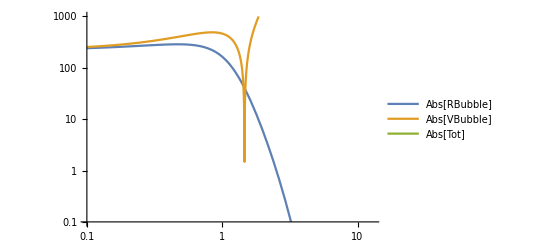

```mathematica
LogLogPlot[Evaluate[AllLines[{0.7,0.3,0.4,1-Exp[-ϵ],0.1,0.7}]],{ϵ,0.1,13.0},PlotRange->{0.1,10^3}, PlotLegends->AllLabels]
```

UV limit in k

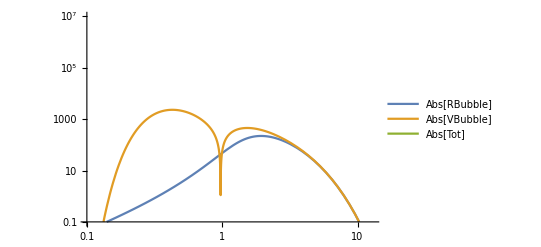

```mathematica
LogLogPlot[Evaluate[AllLines[{1-Exp[-ϵ],0.3,0.4,0.7,0.1,0.7}]],{ϵ,0.1,13.0},PlotRange->{0.1,10^7}, PlotLegends->AllLabels]
```

### IR limit

First compare directly the bubble

```mathematica
TMPkvec={10.,20.,30.};
```

```mathematica
TMPkvec=100.0/Sqrt[VDot[TMPkvec,TMPkvec]] TMPkvec;
```

```mathematica
TMPlvec={TMPkvec⟦1⟧+10^-ϵ,TMPkvec⟦2⟧+10^-ϵ,TMPkvec⟦3⟧+10^-ϵ};
```

```mathematica
VBubbleME[{100.0,0.,0.,100.0},{100.0,0.,0.,-100.0},{Sqrt[VDot[TMPkvec,TMPkvec]],TMPkvec⟦1⟧,TMPkvec⟦2⟧,TMPkvec⟦3⟧},1/3*{∞,TMPlvec⟦1⟧,TMPlvec⟦2⟧,TMPlvec⟦3⟧}/.{ϵ->3},True,True]
```

BUBBLE FACTOR :: q0=100.

BUBBLE FACTOR :: 1/(2  Sqrt[VDot[qvec,  qvec]])=0.005

BUBBLE FACTOR :: 1/(2  Sqrt[VDot[kminus,  kminus]])=0.014999759468417946

BUBBLE FACTOR :: 1/(2  Sqrt[VDot[kplus,  kplus]])=0.007500060134221397

BUBBLE FACTOR :: 1/(Sqrt[VDot[kminus,  kminus]] + Sqrt[VDot[kplus,  kplus]])^2=4.666738655959526*^6

BUBBLE FACTOR :: ME=-60589.90566016182

BUBBLE FACTOR :: MEUVCT=-2.0095987603270822*^-15

{-60589.9,0,2.0096×10^-15}

```mathematica
RBubbleMESoper[{100.0,0.,0.,100.0},{100.0,0.,0.,-100.0},{Sqrt[VDot[TMPkvec,TMPkvec]],TMPkvec⟦1⟧,TMPkvec⟦2⟧,TMPkvec⟦3⟧},1/3.*{∞,TMPlvec⟦1⟧,TMPlvec⟦2⟧,TMPlvec⟦3⟧}/.{ϵ->3},True]
```

BUBBLE FACTOR :: q0=100.

BUBBLE FACTOR :: Sqrt[VDot[kminus, kminus]]=33.3339

BUBBLE FACTOR :: Sqrt[VDot[kplus, kplus]]=66.6661

BUBBLE FACTOR :: VDot[qvec, qvec]=10000.

BUBBLE FACTOR :: qbar^2=          -7
2.14282 10

BUBBLE FACTOR :: ME=60589.905659512646

60589.9

Now compare directly the function given to the integrator

```mathematica
RBubbleIntegrandFunction[{
0.7,0.3,0.6,
0.1,0.3+10^-2,0.6+10^-2
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True,False]
```

xs={0.7, 0.3, 0.6, 0.1, 0.31, 0.61}

rescaling=0.428552

lmu=(0.0476169,{-0.0303451, -0.0251037, 0.0267647})

kmu=(1.00005,{-0.654479, -0.475507, 0.587759})

-lmu+kmu=(0.952428,{-0.624134, -0.450403, 0.560994})

|l|+|l-k|+|k|=2. vs Q0=2.

|l-k|=0.952428 vs -(l0-k0)=0.952428

|l|=0.0476169 vs l0=0.0476169

|k|=0.999955 vs k0=1.00005

|k|=0.999955 vs -(k0-Q0)=0.999955

RBubbleME=83.80294002495721

(1/Eb1)*(1/Eb2)=22.04990007391019

Integrand=         6
1.1481 10  + 0. I

Integrand*jac=2.759847543291734*^8 + 0.*I

h[rescaling,σ]=0.538871

rescaling^6=0.00619471

1/(rescaling jacobian)=0.214276

jacobian=240.384

Integrand=197408. + 0. I

197408.

```mathematica
VBubbleIntegrandFunction[{
0.7,0.3,0.6,
0.1,0.3+10^-2,0.6+10^-2
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.7, 0.3, 0.6, 0.1, 0.31, 0.61}

rescaling=0.428571

lmu=(Infinity,{-0.0303465, -0.0251048, 0.0267659})

kmu=(1.,{-0.654508, -0.475528, 0.587785})

-lmu+kmu=(-Infinity,{-0.624162, -0.450423, 0.561019})

|k|+|k|=2. vs Q0=2.

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

VBubbleME[p1,p2,kmu,lmu]*CorrFactor=-83.8048944912231

(1/Eb1)*(1/Eb2)=22.04790060018676

Integrand VBubbleIntegrandPlus*jac  =-2.759536516318684*^8 + 0.*I

Integrand VBubbleIntegrandMinus*jac =0. + 0.*I

UV CT VBubbleIntegrand*jac          =24.78102663810514 + 0.*I

Ratio                        =-1.1135682781097602*^7 + 0.*I

h[rescaling,σ]=0.538869

rescaling^6=0.0061964

1/(rescaling jacobian)=0.214286

jacobian=240.384

Integrand=-197447. + 0. I

-197447.

```mathematica
Manipulate[(((RBubbleIntegrandFunction[{
r,θ,ϕ,
0.1,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]
)

/(VBubbleIntegrandFunction[{
r,θ,ϕ,
0.1,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]
))),{{ϵ,3.},0.1,10.},{{r,0.3},0,1.},{{θ,0.1},0.,1},{{ϕ,0.3},0.,1}]
```

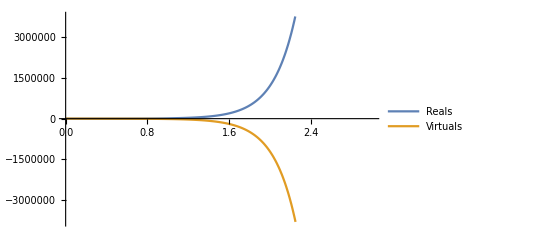

```mathematica
Plot[
{RBubbleIntegrandFunction[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]
,
VBubbleIntegrandFunction[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]},{ϵ,0.001,3.},
PlotRange->{Automatic,Automatic},PlotLegends->{"Reals","Virtuals"}
]
```

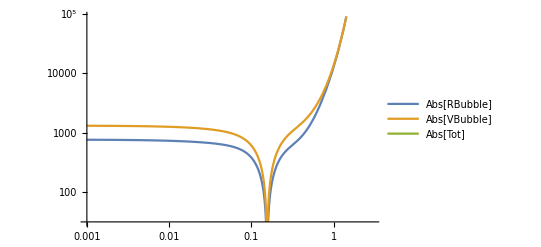

```mathematica
LogLogPlot[
Evaluate[AllLines[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
}]],{ϵ,0.001,3.},PlotLegends->AllLabels
]
```

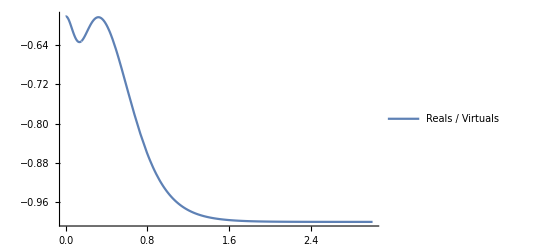

```mathematica
Plot[
(RBubbleIntegrandFunction[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]
/
VBubbleIntegrandFunction[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]),{ϵ,0.001,3.},
PlotRange->{Automatic,{-0.5,-1.1}},PlotLegends->{"Reals / Virtuals"}
]
```

## Numerical integration

```mathematica
(*ThisIntegrand[x1,x2,x3,x4,x5,x6]=RBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]+
VBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False];
(*MCPoints={};*)
rBoundMin=0.001;rBoundMax=0.999;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOBubbleResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {10000,100000,500000,1000000,5000000,10000000,50000000,100000000}}]
]*)
```

```mathematica
NLOBubbleResultsFullRange=<|10000->-351.5099534304602,100000->-362.6284658989167,500000->-356.88199610045723,1000000->-358.9294231531556,3000000->-357.7492342628907,5000000->-359.4055351033599,7000000->-359.4893767262666,10000000->-359.010342807277|>;
```

```mathematica
NLOBubbleResults0p01Boundary=<|10000->-350.4338020362801,100000->-356.4048168228259,500000->-354.495218469179,1000000->-353.9020269072824,5000000->-355.47644185972916,10000000->-355.873098262926,50000000->-356.2809429736474,100000000->-356.47355545089073|>;
```

```mathematica
(*NLOBubbleResults0p001Boundary=*)
```

```mathematica
FinalNLOBubbleResult = NLOBubbleResults0p01Boundary[Max[Keys[NLOBubbleResults0p01Boundary]]]
```

-356.474

```mathematica
(*ThisIntegrand[x1,x2,x3,x4,x5,x6]=RBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False]+
alaLTDSoperLRDifferentiatedVBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False,False];
(*MCPoints={};*)
rBoundMin=0.001;rBoundMax=0.999;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOBubbleResultsSHIFTEDUVCT=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {10000,100000,500000,1000000,10000000}}]
]*)
```

```mathematica
(*FinalNLOBubbleResultSHIFTEDUVCT = NLOBubbleResultsSHIFTEDUVCT[Max[Keys[NLOBubbleResultsSHIFTEDUVCT]]]*)
```

Double Triangle

## Virtual L x B* (LxB)

-Graphics-

### Direct computation

```mathematica
LxBLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[101],mu12,s[102]] delta[i[101],i[102]]
(ⅈ gamma[s[102],mu101,s[103]] vector[k,mu101] )
(-ⅈ) gamma[s[103],mu102,s[14]] T[a[1001],i[102],i[14]]
(-ⅈ g[mu102,mu103])delta[a[1001],a[1002]]
(-ⅈ) gamma[s[13],mu103,s[104]] T[a[1002],i[13],i[101]]
(ⅈ gamma[s[104],mu104,s[101]] (vector[k,mu104]-vector[p1,mu104]-vector[p2,mu104]) )
)
```

```mathematica
LxB4DUVLeftNum[p1_,p2_,k_,l_]:=Module[
{A10=4, A20=-2 ,B10=4,Q0,MUV},
Q0=Energy[p1]+Energy[p2];
MUV=2Q0;
(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
((ⅈ)delta[i[101],i[102]]delta[a[1001],a[1002]]T[a[1001],i[102],i[14]]T[a[1002],i[13],i[101]](
A10 gamma[s[13],mu1001,s[14]]vector[k,mu1001]vector[k,mu12]
+A20 SP[k,k]gamma[s[13],mu12,s[14]]
+MUV^2 B10 gamma[s[13],mu12,s[14]]
)
)
)
]
```

```mathematica
LxBLeftNumUV[p1_,p2_,k_,l_]:=
(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
)
```

```mathematica
LxBRightNum[p1_,p2_,k_,l_]:=(
(ⅈ )gamma[s[24],mu21,s[23]]delta[i[24],i[23]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
LxBMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK(?) but does not reproduce the matrix element

```mathematica
LxBNumerator[p1_,p2_,k_,l_]:=contractColor[contractSpin[
(
LxBLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[14],mu3,s[24]]vector[l,mu3])delta[i[14],i[24]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[l,mu5]))delta[i[23],i[13]]
LxBRightNum[p1,p2,k,l]
)
,{p1,p2,k,l}],i,a]
```

```mathematica
LxB4DUVNumerator[p1_,p2_,k_,l_]:=contractColor[contractSpin[
(
LxB4DUVLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[14],mu3,s[24]]vector[l,mu3])delta[i[14],i[24]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[l,mu5]))delta[i[23],i[13]]
LxBRightNum[p1,p2,k,l]
)
,{p1,p2,k,l}],i,a]
```

Below we omit the denominator of the loop propagator so that we can account for them in the LTD treatment

```mathematica
LxBME[p1_,p2_,k_,l_]:=Module[
{MENum },
MENum =( (LxBMEPrefactors[p1,p2,k,l]
(1/SP[p1+p2,p1+p2])LxBNumerator[p1,p2,k,l](1/SP[p1+p2,p1+p2]) )/.{
SP[l,l]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues;
MENum
]
```

```mathematica
LxBME[p1_List,p2_List,k_List,l_List]=LxBME[p1,p2,k,l];
```

```mathematica
LxBUV[p1_,p2_,k_,l_]:=Module[
{MENum ,kvec,A10=4, A20=-2 ,B10=4, Q0,MUV},
Q0=Energy[p1]+Energy[p2];
MUV=2Q0;
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
MENum =( ((contractColor[contractSpin[(LxBMEPrefactors[p1,p2,k,l](1/SP[p1+p2,p1+p2])
(
LxBLeftNumUV[p1,p2,k,l]
(ⅈ)4/3(
(-4 A20 gamma[s[13],mu12,s[14]]-A10  gamma[s[13],muX1,s[14]] vector[EnergyDirection,muX1]vector[NDirection,mu12])/(16 Sqrt[VDot[kvec,kvec]+MUV^2]^3)
+(3A10 gamma[s[13],muX2,s[14]]vector[kspace,muX2]vector[kspace,mu12]+3(A20+B10)MUV^2 gamma[s[13],mu12,s[14]])/(16 Sqrt[VDot[kvec,kvec]+MUV^2]^5)
)delta[i[13],i[14]]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[14],mu3,s[24]]vector[l,mu3])delta[i[14],i[24]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[l,mu5]))delta[i[23],i[13]]
LxBRightNum[p1,p2,k,l]
)
(1/SP[p1+p2,p1+p2]) ),{p1,p2,k,l,EnergyDirection,NDirection,kspace}],i,a])/.{
EnergyDirection->{1,0,0,0},
NDirection->{1,0,0,0},
kspace->{0,Xcomp[k],Ycomp[k],Zcomp[k]}
}
)/.{
SP[l,l]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues;
MENum
]
```

```mathematica
LxBUV[p1_List,p2_List,k_List,l_List]=LxBUV[p1,p2,k,l];
```

Now apply LTD to this ME:

```mathematica
LxBMELTD[p1_,p2_,k_,l_,DEBUG_]:=Module[
{LTD1,LTD2,LTD3,UV,Q0,MUV, kvec,lvec,k1,k2,k3
},
Q0=Energy[LTD1]+Energy[LTD2];
MUV=2 Q0;
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
k1={Sqrt[VDot[kvec,kvec]],Xcomp[k],Ycomp[k],Zcomp[k]};
LTD1=LxBME[p1,p2,k1,l] 1/(2Sqrt[VDot[kvec,kvec]])1/SP[l-k1,l-k1] 1/SP[k1-p1-p2,k1-p1-p2];
If[DEBUG,MyPrint["LTD1 = "<>ToString[LTD1, InputForm]];];
k2={Sqrt[VDot[kvec,kvec]]+Energy[p1]+Energy[p2],Xcomp[k],Ycomp[k],Zcomp[k]};
LTD2=LxBME[p1,p2,k2,l] 1/SP[k2,k2] 1/SP[l-k2,l-k2] 1/(2Sqrt[VDot[kvec,kvec]]);
If[DEBUG,MyPrint["LTD2 = "<>ToString[LTD2, InputForm]];];
k3={Sqrt[VDot[kvec-lvec,kvec-lvec]]+Energy[l],Xcomp[k],Ycomp[k],Zcomp[k]};
LTD3=LxBME[p1,p2,k3,l] 1/SP[k3,k3] 1/(2Sqrt[VDot[kvec-lvec,kvec-lvec]])1/SP[k3-p1-p2,k3-p1-p2];
If[DEBUG,MyPrint["LTD3 = "<>ToString[LTD3, InputForm]];];
UV=((2π)/(-2π ⅈ)) LxBUV[p1,p2,k,l] ;
If[DEBUG,MyPrint["UV = "<>ToString[UV, InputForm]];];
1/(2π)^4(-2π ⅈ ){LTD1,LTD2,LTD3,UV}
]
```

```mathematica
LxBIntegrand[p1_List,p2_List,k_List,l_List]:=GeVtoPbConversion(1/-ⅈ)^2 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[l]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[l]])LxBMELTD[p1,p2,k,l,False]
```

```mathematica
LxBRescalingSolutionParametric=Solve[
FullSimplify[Sqrt[t^2 INldotl]+Sqrt[t^2 INldotl]-INQ0==0,
Assumptions->{t>0,INldotl>0,INQ0>0}],{t}
];
LxBRescalingSolutionParametricJacobian=
Abs[(D[FullSimplify[Sqrt[t^2 INldotl]+Sqrt[t^2 INldotl]-INQ0,
Assumptions->{t>0,INldotl>0,INQ0>0}],t])/.{t->LxBRescalingSolutionParametric}];
LxBRescalingSolution[Q0_,lvec_]:=(LxBRescalingSolutionParametric/.{INldotl->VDot[lvec,lvec],INQ0->Q0})
LxBRescalingSolutionJacobian[Q0_,lvec_]:=Abs[(LxBRescalingSolutionParametricJacobian/.{INldotl->VDot[lvec,lvec],INQ0->Q0})]
```

```mathematica
LxBIntegrandFunction[xs_,p1_,p2_,DEBUG_,OptionsPattern[Cut->(NoCut[##]&)]]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,LTDIntegrand,
QMinuslmu,cutFunction=OptionValue[Cut]
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
If[DEBUG,MyPrint["k jacobian="<>ToString[kmap["jacobian"],InputForm]];];
If[DEBUG,MyPrint["|k|="<>ToString[Sqrt[VDot[kvec,kvec]],InputForm]];];
rescaling=(t/.LxBRescalingSolution[Q0,lvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=LxBRescalingSolutionJacobian[Q0,lvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
k0=∞;
l0=Sqrt[VDot[lvec,lvec]];
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
QMinuslmu={Q0-l0,-lvec⟦1⟧,-lvec⟦2⟧,-lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|l|+|l|="<>ToString[Sqrt[VDot[lvec,lvec]]+Sqrt[VDot[lvec,lvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|l|="<>ToString[Sqrt[VDot[lvec,lvec]]]<>" vs k0="<>ToString[l0]]];
If[DEBUG,Print["|l|="<>ToString[Sqrt[VDot[lvec,lvec]]]<>" vs Q0-l0="<>ToString[Q0-l0]]];
LTDIntegrand=LxBIntegrand[p1,p2,kmu,lmu];
Integrand=Integrand*Total[LTDIntegrand];
If[DEBUG,MyPrint["Integrand LTD1  ="<>ToString[LTDIntegrand⟦1⟧,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD2  ="<>ToString[LTDIntegrand⟦2⟧,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD3  ="<>ToString[LTDIntegrand⟦3⟧,InputForm]];];
If[DEBUG,MyPrint["Integrand UVCT  ="<>ToString[LTDIntegrand⟦4⟧,InputForm]];];
If[DEBUG,MyPrint["Total[LTD]      ="<>ToString[Total[LTDIntegrand],InputForm]];];
If[DEBUG,MyPrint["Ratio LTD/UV    ="<>ToString[Total[LTDIntegrand⟦;;-2⟧]/LTDIntegrand⟦4⟧,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD1*jac  ="<>ToString[LTDIntegrand⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD2*jac  ="<>ToString[LTDIntegrand⟦2⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD3*jac  ="<>ToString[LTDIntegrand⟦3⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Integrand UVCT*jac  ="<>ToString[LTDIntegrand⟦4⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Total[LTD]*jac      ="<>ToString[Total[LTDIntegrand]*jacobian,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
If[DEBUG,Print["Observable argument #1 lmu="<>ToString[lmu,InputForm]];];
If[DEBUG,Print["Observable argument #2 QMinuslmu="<>ToString[QMinuslmu,InputForm]];];
Re[Integrand]cutFunction[lmu,QMinuslmu]
]
```

Test the integrand now

```mathematica
LxBIntegrandFunction[{0.9999,0.2,0.3,0.4,0.5,0.6},{1,0,0,1},{1,0,0,-1},True]
```

xs={0.9999, 0.2, 0.3, 0.4, 0.5, 0.6}

k jacobian=1.1600095458706522*^17

|k|=9999.0000000011

rescaling=1.5

lmu=(1.,                                 -17
{-0.809017, -0.587785, 6.12323 10   })

kmu=(Infinity,{-2724.26, 8384.42, 12134.})

-lmu+kmu=(Infinity,{-2723.45, 8385., 12134.})

|l|+|l|=2. vs Q0=2

|l|=1. vs k0=1.

|l|=1. vs Q0-l0=1.

Integrand LTD1  =-0.00003246285624105382 + 0.*I

Integrand LTD2  =-0.000046886843250908985 + 0.*I

Integrand LTD3  =0.00007934970007188192 + 0.*I

Integrand UVCT  =-5.798297203212924*^-13 + 0.*I

Total[LTD]      =8.940602164858591*^-17 + 0.*I

Ratio LTD/UV    =-1.000154197593304 + 0.*I

Integrand LTD1*jac  =-9.176836915942822*^13 + 0.*I

Integrand LTD2*jac  =-1.3254314741191069*^14 + 0.*I

Integrand LTD3*jac  =2.2431151821069656*^14 + 0.*I

Integrand UVCT*jac  =-1.639104933618283*^6 + 0.*I

Total[LTD]*jac      =252.7394613338842 + 0.*I

h[rescaling,σ]=0.421118

rescaling^6=11.3906

1/(rescaling jacobian)=0.75

jacobian=          18
2.82687 10

Integrand=909.255 + 0. I

Observable argument #1 lmu={0.9999999999999998, -0.8090169943749473, -0.5877852522924729, 6.123233995736765*^-17}

Observable argument #2 QMinuslmu={1.0000000000000002, 0.8090169943749473, 0.5877852522924729, -6.123233995736765*^-17}

909.255

### Numerator coefficients

Below we will use Armin’s tools to extract the symmetric tensor coefficients of the LxB contribution

```mathematica
LxBNumeratorCoefs[p1_,p2_, IncludeZeros_]:=Module[
{Num,tensCoefs,symCoeffs,GeVtoPbParam, OverallFactors,RANK=4
},
(* The overall factor contains the correction for the -ⅈ part of each Cutkosky cut and the conversion to pb. The matrix element helicity+color averaging factor is part of RxRAMEPrefactors.*)
OverallFactors=(1/-ⅈ)^2;
Num=((OverallFactors LxBMEPrefactors[p1Param,p2Param,k,l]LxBNumerator[p1Param,p2Param,k,l])/.{
SP[l,l]:>0,SP[p1Param,p1Param]:>0,SP[p2Param,p2Param]:>0})/.NumericalValues;
CreateSymmetricPolynomial[
{p1Param,p2Param},{k,l},
Num,
RANK,False,{p1Param->p1,p2Param->p2}]
]
```

```mathematica
LxB4DUVNumeratorCoefs[p1_,p2_, IncludeZeros_]:=Module[
{Num, OverallFactors,RANK=4
},
(* The overall factor contains the correction for the -ⅈ part of each Cutkosky cut and the conversion to pb. The matrix element helicity+color averaging factor is part of RxRAMEPrefactors.*)
OverallFactors=(1/-ⅈ)^2;
Num=((OverallFactors LxBMEPrefactors[p1Param,p2Param,k,l]LxB4DUVNumerator[p1Param,p2Param,k,l])/.{
SP[l,l]:>0,SP[p1Param,p1Param]:>0,SP[p2Param,p2Param]:>0})/.NumericalValues;
CreateSymmetricPolynomial[
{p1Param,p2Param},{k,l},
Num,
RANK,False,{p1Param->p1,p2Param->p2}]
]
```

When we now evaluate them (removing the zero ones) and store them in the variable RxRANumeratorCoefsValues

```mathematica
LxBNumeratorCoefsValues=LxBNumeratorCoefs[{1,0,0,1},{1,0,0,-1},False];
```

```mathematica
LxB4DUVNumeratorCoefsValues=LxB4DUVNumeratorCoefs[{1,0,0,1},{1,0,0,-1},False];
```

There are 25 non-zero coefficients for the core contributions and three for the UV counterterm

```mathematica
{Length[LxBNumeratorCoefsValues],Length[LxB4DUVNumeratorCoefsValues]}
```

{25,22}

which read as follows:

```mathematica
LxBNumeratorCoefsValues
```

(sym({0}) | sym({0}) | {0.-0.758685 ⅈ}
sym({0}) | sym({0,0}) | {0.+0.379342 ⅈ}
sym({0}) | sym({3,3}) | {0.-0.379342 ⅈ}
sym({1}) | sym({0,1}) | {0.-0.379342 ⅈ}
sym({2}) | sym({0,2}) | {0.-0.379342 ⅈ}
sym({3}) | sym({3}) | {0.-0.758685 ⅈ}
sym({0,0}) | sym({0}) | {0.+0.379342 ⅈ}
sym({0,0}) | sym({0,0}) | {0.-0.189671 ⅈ}
sym({0,0}) | sym({3,3}) | {0.+0.189671 ⅈ}
sym({0,1}) | sym({1}) | {0.-0.379342 ⅈ}
sym({0,1}) | sym({0,1}) | {0.+0.379342 ⅈ}
sym({0,2}) | sym({2}) | {0.-0.379342 ⅈ}
sym({0,2}) | sym({0,2}) | {0.+0.379342 ⅈ}
sym({1,1}) | sym({0,0}) | {0.+0.189671 ⅈ}
sym({1,1}) | sym({1,1}) | {0.-0.379342 ⅈ}
sym({1,1}) | sym({3,3}) | {0.-0.189671 ⅈ}
sym({1,2}) | sym({1,2}) | {0.-0.758685 ⅈ}
sym({1,3}) | sym({1,3}) | {0.-0.379342 ⅈ}
sym({2,2}) | sym({0,0}) | {0.+0.189671 ⅈ}
sym({2,2}) | sym({2,2}) | {0.-0.379342 ⅈ}
sym({2,2}) | sym({3,3}) | {0.-0.189671 ⅈ}
sym({2,3}) | sym({2,3}) | {0.-0.379342 ⅈ}
sym({3,3}) | sym({0}) | {0.-0.379342 ⅈ}
sym({3,3}) | sym({0,0}) | {0.+0.189671 ⅈ}
sym({3,3}) | sym({3,3}) | {0.-0.189671 ⅈ})

We can now attempt to reproduce the UV contribution from the original complete integrand

```mathematica
LxB4DUVTarget=LxBIntegrand[{1,0,0,1},{1,0,0,-1},{3,4,5,6},{7,8,9,10}]⟦-1⟧
```

-0.0280269+0. ⅈ

Do not forget the factor 2π  from the integration over the loop momentum energy

```mathematica
LxB4DUVEnergyIntegrated[p1_,p2_,k_,l_]:=Module[
{
lmu={Energy[l],Xcomp[l],Ycomp[l],Zcomp[l]},
kvec={Xcomp[k],Ycomp[k],Zcomp[k]},
kmu={k0,Xcomp[k],Ycomp[k],Zcomp[k]
}
},(2π(1/((3-1)!)D[EvaluatePolynomial[LxB4DUVNumeratorCoefsValues,{kmu,lmu}]/((k0+Sqrt[VDot[kvec,kvec]+MUV^2])^3),{k0,3-1}])/.{k0->Sqrt[VDot[kvec,kvec]+MUV^2]})/.{MUV->2 (Energy[p1]+Energy[p2])}
]
```

```mathematica
(GeVtoPbConversion Hold[((1/LDot[p1+p2,p1+p2])
LxB4DUVEnergyIntegrated[p1,p2,k,l]
(1/LDot[p1+p2,p1+p2])1/(2π)^8 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[l]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[l]]))]/.{
p1->{1,0,0,1},
p2->{1,0,0,-1},
k->{3,4,5,6},
l->{7,8,9,10}
})//ReleaseHold//N
```

-0.0280269

They match!

## Virtual B x L* (BxL)

-Graphics-

### Direct computation

```mathematica
BxLLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
)
```

```mathematica
BxLRightNum[p1_,p2_,k_,l_]:=(
(-ⅈ gamma[s[202],mu204,s[204]] (vector[l,mu204]))
(ⅈ) gamma[s[204],mu203,s[23]] T[a[2002],i[202],i[23]]
(ⅈ g[mu202,mu203])delta[a[2001],a[2002]]
(ⅈ) gamma[s[24],mu202,s[203]] T[a[2001],i[24],i[201]]
(-ⅈ gamma[s[203],mu201,s[201]] (vector[l,mu201]-vector[p1,mu201]-vector[p2,mu201] ))
(ⅈ )gamma[s[201],mu21,s[202]]delta[i[201],i[202]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

```mathematica
BxLRightNumUV[p1_,p2_,k_,l_]:=
(
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

```mathematica
BxL4DUVRightNum[p1_,p2_,k_,l_]:=Module[
{A10=4, A20=-2 ,B10=4,Q0,MUV},
Q0=Energy[p1]+Energy[p2];
MUV=2Q0;
(
((-ⅈ)delta[i[201],i[202]]delta[a[2001],a[2002]]T[a[2002],i[202],i[23]] T[a[2001],i[24],i[201]](
A10 gamma[s[24],mu2001,s[23]]vector[l,mu2001]vector[l,mu21]
+A20 SP[l,l]gamma[s[24],mu21,s[23]]
+MUV^2 B10 gamma[s[24],mu21,s[23]]
)
)
(ⅈ g[mu21,mu22])
(ⅈ) gamma[s[22],mu22,s[21]]
)
]
```

Now build the squared matrix element

```mathematica
BxLMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK(?) but does not reproduce the matrix element

```mathematica
BxLNumerator[p1_,p2_,k_,l_]:=contractColor[contractSpin[
(
BxLLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[23],mu3,s[13]]vector[k,mu3])delta[i[23],i[13]]
(gamma[s[14],mu5,s[24]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[14],i[24]]
BxLRightNum[p1,p2,k,l]
)
,{p1,p2,k,l}],i,a]
```

```mathematica
BxL4DUVNumerator[p1_,p2_,k_,l_]:=contractColor[contractSpin[
(
BxLLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[23],mu3,s[13]]vector[k,mu3])delta[i[23],i[13]]
(gamma[s[14],mu5,s[24]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[14],i[24]]
BxL4DUVRightNum[p1,p2,k,l]
)
,{p1,p2,k,l}],i,a]
```

Below we omit the denominator of the loop propagator so that we can account for them in the LTD treatment

```mathematica
BxLME[p1_,p2_,k_,l_]:=Module[
{MENum },
MENum =( (BxLMEPrefactors[p1,p2,k,l]
(1/SP[p1+p2,p1+p2])BxLNumerator[p1,p2,k,l](1/SP[p1+p2,p1+p2]) )/.{
SP[k,k]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues;
MENum
]
```

```mathematica
BxLME[p1_List,p2_List,k_List,l_List]=BxLME[p1,p2,k,l];
```

```mathematica
BxLUV[p1_,p2_,k_,l_]:=Module[
{MENum ,lvec,A10=4, A20=-2 ,B10=4, Q0,MUV},
Q0=Energy[p1]+Energy[p2];
MUV=2Q0;
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
MENum =( ((contractColor[contractSpin[(BxLMEPrefactors[p1,p2,k,l](1/SP[p1+p2,p1+p2])
(
BxLLeftNum[p1,p2,k,l]
(-ⅈ)4/3(
(-4 A20 gamma[s[24],mu21,s[23]]-A10  gamma[s[24],muX1,s[23]] vector[EnergyDirection,muX1]vector[NDirection,mu21])/(16 Sqrt[VDot[lvec,lvec]+MUV^2]^3)
+(3A10 gamma[s[24],muX2,s[23]]vector[lspace,muX2]vector[lspace,mu21]+3(A20+B10)MUV^2 gamma[s[24],mu21,s[23]])/(16 Sqrt[VDot[lvec,lvec]+MUV^2]^5)
)delta[i[24],i[23]]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[23],mu3,s[13]]vector[k,mu3])delta[i[23],i[13]]
(gamma[s[14],mu5,s[24]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[14],i[24]]
BxLRightNumUV[p1,p2,k,l]
)
(1/SP[p1+p2,p1+p2]) ),{p1,p2,k,l,EnergyDirection,NDirection,lspace}],i,a])/.{
EnergyDirection->{1,0,0,0},
NDirection->{1,0,0,0},
lspace->{0,Xcomp[l],Ycomp[l],Zcomp[l]}
}
)/.{
SP[k,k]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues;
MENum
]
```

```mathematica
BxLUV[p1_List,p2_List,k_List,l_List]=BxLUV[p1,p2,k,l];
```

Now apply LTD to this ME:

```mathematica
BxLMELTD[p1_,p2_,k_,l_,DEBUG_]:=Module[
{LTD1,LTD2,LTD3,UV,kvec,lvec,l1,l2,l3},
lvec={Xcomp[l],Ycomp[l],Zcomp[l]};
kvec={Xcomp[k],Ycomp[k],Zcomp[k]};
l1={Sqrt[VDot[lvec,lvec]],Xcomp[l],Ycomp[l],Zcomp[l]};
LTD1=BxLME[p1,p2,k,l1] 1/(2Sqrt[VDot[lvec,lvec]])1/SP[l1-k,l1-k] 1/SP[l1-p1-p2,l1-p1-p2];
If[DEBUG,MyPrint["LTD1 = "<>ToString[LTD1, InputForm]];];
l2={Sqrt[VDot[lvec,lvec]]+Energy[p1]+Energy[p2],Xcomp[l],Ycomp[l],Zcomp[l]};
LTD2=BxLME[p1,p2,k,l2] 1/SP[l2,l2] 1/SP[l2-k,l2-k] 1/(2Sqrt[VDot[lvec,lvec]]);
If[DEBUG,MyPrint["LTD2 = "<>ToString[LTD2, InputForm]];];
l3={Sqrt[VDot[lvec-kvec,lvec-kvec]]+Energy[k],Xcomp[l],Ycomp[l],Zcomp[l]};
LTD3=BxLME[p1,p2,k,l3] 1/SP[l3,l3] 1/(2Sqrt[VDot[lvec-kvec,lvec-kvec]])1/SP[l3-p1-p2,l3-p1-p2];
If[DEBUG,MyPrint["LTD3 = "<>ToString[LTD3, InputForm]];];
UV=((2π)/(2π ⅈ)) BxLUV[p1,p2,k,l] ;
If[DEBUG,MyPrint["UV = "<>ToString[UV, InputForm]];];
1/(2π)^4(+2π ⅈ ){LTD1,LTD2,LTD3,UV}
]
```

```mathematica
BxLIntegrand[p1_List,p2_List,k_List,l_List]:=GeVtoPbConversion(1/-ⅈ)^2 1/(2π)^4 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[k]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])BxLMELTD[p1,p2,k,l,False]
```

```mathematica
(*BxLMELTD[{1,0,0,1},{1,0,0,-1},{0.1,0.2,0.3,0.4},{∞,0.5,0.6,0.7},True]*)
```

```mathematica
BxLRescalingSolutionParametric=Solve[
FullSimplify[Sqrt[t^2 INkdotk]+Sqrt[t^2 INkdotk]-INQ0==0,
Assumptions->{t>0,INkdotk>0,INQ0>0}],{t}
];
BxLRescalingSolutionParametricJacobian=
Abs[(D[FullSimplify[Sqrt[t^2 INkdotk]+Sqrt[t^2 INkdotk]-INQ0,
Assumptions->{t>0,INkdotk>0,INQ0>0}],t])/.{t->BxLRescalingSolutionParametric}];
BxLRescalingSolution[Q0_,kvec_]:=(BxLRescalingSolutionParametric/.{INkdotk->VDot[kvec,kvec],INQ0->Q0})
BxLRescalingSolutionJacobian[Q0_,kvec_]:=Abs[(BxLRescalingSolutionParametricJacobian/.{INkdotk->VDot[kvec,kvec],INQ0->Q0})]
```

```mathematica
BxLIntegrandFunction[xs_,p1_,p2_,DEBUG_,OptionsPattern[Cut->(NoCut[##]&)]]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,LTDIntegrand,
cutFunction=OptionValue[Cut],QMinuskmu
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
If[DEBUG,MyPrint["l jacobian="<>ToString[lmap["jacobian"],InputForm]];];
If[DEBUG,MyPrint["|l|="<>ToString[Sqrt[VDot[lvec,lvec]],InputForm]];];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.BxLRescalingSolution[Q0,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=BxLRescalingSolutionJacobian[Q0,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
(* Set l0 to infinity to make sure it is not used. *)
l0=∞;
k0=Sqrt[VDot[kvec,kvec]];
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
QMinuskmu={Q0-k0,-kvec⟦1⟧,-kvec⟦2⟧,-kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|k|+|k|="<>ToString[Sqrt[VDot[kvec,kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs Q0-k0="<>ToString[Q0-k0]]];
LTDIntegrand=BxLIntegrand[p1,p2,kmu,lmu];
Integrand=Integrand*Total[LTDIntegrand];
If[DEBUG,MyPrint["Integrand LTD1  ="<>ToString[LTDIntegrand⟦1⟧,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD2  ="<>ToString[LTDIntegrand⟦2⟧,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD3  ="<>ToString[LTDIntegrand⟦3⟧,InputForm]];];
If[DEBUG,MyPrint["Integrand UVCT  ="<>ToString[LTDIntegrand⟦4⟧,InputForm]];];
If[DEBUG,MyPrint["Total[LTD]      ="<>ToString[Total[LTDIntegrand],InputForm]];];
If[DEBUG,MyPrint["Ratio LTD/UV    ="<>ToString[Total[LTDIntegrand⟦;;-2⟧]/LTDIntegrand⟦4⟧,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD1*jac  ="<>ToString[LTDIntegrand⟦1⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD2*jac  ="<>ToString[LTDIntegrand⟦2⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Integrand LTD3*jac  ="<>ToString[LTDIntegrand⟦3⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Integrand UVCT*jac  ="<>ToString[LTDIntegrand⟦4⟧*jacobian,InputForm]];];
If[DEBUG,MyPrint["Total[LTD]*jac      ="<>ToString[Total[LTDIntegrand]*jacobian,InputForm]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
If[DEBUG,Print["Observable argument #1 kmu="<>ToString[kmu,InputForm]];];
If[DEBUG,Print["Observable argument #2 QMinuskmu="<>ToString[QMinuskmu,InputForm]];];
Re[Integrand]cutFunction[kmu,QMinuskmu]
]
```

Test the integrand now

```mathematica
BxLIntegrandFunction[{0.1,0.2,0.3,0.999,0.5,0.6},{1,0,0,1},{1,0,0,-1},True]
```

xs={0.1, 0.2, 0.3, 0.999, 0.5, 0.6}

l jacobian=1.9699750123783086*^13

|l|=998.9999999999992

rescaling=9.

lmu=(Infinity,                              -13
{-7273.87, -5284.78, 5.5054 10   })

kmu=(1.,{-0.181636, 0.559017, 0.809017})

-lmu+kmu=(-Infinity,{7273.69, 5285.34, 0.809017})

|k|+|k|=2. vs Q0=2

|k|=1. vs k0=1.

|k|=1. vs Q0-k0=1.

Integrand LTD1  =-0.00016758241058678288 + 0.*I

Integrand LTD2  =-0.00024201037218254145 + 0.*I

Integrand LTD3  =0.00040959278380251434 + 0.*I

Integrand UVCT  =-1.0335776785598596*^-12 + 0.*I

Total[LTD]      =-3.877106968808164*^-16 + 0.*I

Ratio LTD/UV    =-0.9996248891700951 + 0.*I

Integrand LTD1*jac  =-5.838046358963051*^8 + 0.*I

Integrand LTD2*jac  =-8.430883451338842*^8 + 0.*I

Integrand LTD3*jac  =1.4268929846294997*^9 + 0.*I

Integrand UVCT*jac  =-3.600660941618998 + 0.*I

Total[LTD]*jac      =-0.001350662646712516 + 0.*I

h[rescaling,σ]=0.000707529

rescaling^6=531441.

1/(rescaling jacobian)=4.5

jacobian=          12
3.48369 10

Integrand=-2.28538 + 0. I

Observable argument #1 kmu={1., -0.1816356320013402, 0.5590169943749476, 0.8090169943749475}

Observable argument #2 QMinuskmu={1., 0.1816356320013402, -0.5590169943749476, -0.8090169943749475}

-2.28538

### Numerator coefficients

Below we will use Armin’s tools to extract the symmetric tensor coefficients of the BxL contribution

```mathematica
BxLNumeratorCoefs[p1_,p2_, IncludeZeros_]:=Module[
{Num,tensCoefs,symCoeffs,GeVtoPbParam, OverallFactors,RANK=4
},
(* The overall factor contains the correction for the -ⅈ part of each Cutkosky cut and the conversion to pb. The matrix element helicity+color averaging factor is part of RxRAMEPrefactors.*)
OverallFactors=(1/-ⅈ)^2;
Num=((OverallFactors BxLMEPrefactors[p1Param,p2Param,k,l]BxLNumerator[p1Param,p2Param,k,l])/.{
SP[k,k]:>0,SP[p1Param,p1Param]:>0,SP[p2Param,p2Param]:>0})/.NumericalValues;
CreateSymmetricPolynomial[
{p1Param,p2Param},{k,l},
Num,
RANK,False,{p1Param->p1,p2Param->p2}]
]
```

```mathematica
BxL4DUVNumeratorCoefs[p1_,p2_, IncludeZeros_]:=Module[
{Num, OverallFactors,RANK=4
},
(* The overall factor contains the correction for the -ⅈ part of each Cutkosky cut and the conversion to pb. The matrix element helicity+color averaging factor is part of RxRAMEPrefactors.*)
OverallFactors=(1/-ⅈ)^2;
Num=((OverallFactors BxLMEPrefactors[p1Param,p2Param,k,l]BxL4DUVNumerator[p1Param,p2Param,k,l])/.{
SP[k,k]:>0,SP[p1Param,p1Param]:>0,SP[p2Param,p2Param]:>0})/.NumericalValues;
CreateSymmetricPolynomial[
{p1Param,p2Param},{k,l},
Num,
RANK,False,{p1Param->p1,p2Param->p2}]
]
```

When we now evaluate them (removing the zero ones) and store them in the variable RxRANumeratorCoefsValues

```mathematica
BxLNumeratorCoefsValues=BxLNumeratorCoefs[{1,0,0,1},{1,0,0,-1},False];
```

```mathematica
BxL4DUVNumeratorCoefsValues=BxL4DUVNumeratorCoefs[{1,0,0,1},{1,0,0,-1},False];
```

There are 25 non-zero coefficients for the core contributions and three for the UV counterterm

```mathematica
{Length[BxLNumeratorCoefsValues],Length[BxL4DUVNumeratorCoefsValues]}
```

{25,22}

which read as follows:

```mathematica
BxLNumeratorCoefsValues
```

(sym({0}) | sym({0}) | {0.+0.758685 ⅈ}
sym({0}) | sym({0,0}) | {0.-0.379342 ⅈ}
sym({0}) | sym({3,3}) | {0.+0.379342 ⅈ}
sym({1}) | sym({0,1}) | {0.+0.379342 ⅈ}
sym({2}) | sym({0,2}) | {0.+0.379342 ⅈ}
sym({3}) | sym({3}) | {0.+0.758685 ⅈ}
sym({0,0}) | sym({0}) | {0.-0.379342 ⅈ}
sym({0,0}) | sym({0,0}) | {0.+0.189671 ⅈ}
sym({0,0}) | sym({1,1}) | {0.-0.189671 ⅈ}
sym({0,0}) | sym({2,2}) | {0.-0.189671 ⅈ}
sym({0,0}) | sym({3,3}) | {0.-0.189671 ⅈ}
sym({0,1}) | sym({1}) | {0.+0.379342 ⅈ}
sym({0,1}) | sym({0,1}) | {0.-0.379342 ⅈ}
sym({0,2}) | sym({2}) | {0.+0.379342 ⅈ}
sym({0,2}) | sym({0,2}) | {0.-0.379342 ⅈ}
sym({1,1}) | sym({1,1}) | {0.+0.379342 ⅈ}
sym({1,2}) | sym({1,2}) | {0.+0.758685 ⅈ}
sym({1,3}) | sym({1,3}) | {0.+0.379342 ⅈ}
sym({2,2}) | sym({2,2}) | {0.+0.379342 ⅈ}
sym({2,3}) | sym({2,3}) | {0.+0.379342 ⅈ}
sym({3,3}) | sym({0}) | {0.+0.379342 ⅈ}
sym({3,3}) | sym({0,0}) | {0.-0.189671 ⅈ}
sym({3,3}) | sym({1,1}) | {0.+0.189671 ⅈ}
sym({3,3}) | sym({2,2}) | {0.+0.189671 ⅈ}
sym({3,3}) | sym({3,3}) | {0.+0.189671 ⅈ})

We can now attempt to reproduce the UV contribution from the original complete integrand

```mathematica
BxL4DUVTarget=BxLIntegrand[{1,0,0,1},{1,0,0,-1},{3,4,5,6},{7,8,9,10}]⟦-1⟧
```

-0.0269699+0. ⅈ

Do not forge the factor 2π  from the integration over the loop momentum energy

```mathematica
BxL4DUVEnergyIntegrated[p1_,p2_,k_,l_]:=Module[
{
kmu={Energy[k],Xcomp[k],Ycomp[k],Zcomp[k]},
lvec={Xcomp[l],Ycomp[l],Zcomp[l]},
lmu={l0,Xcomp[l],Ycomp[l],Zcomp[l]
}
},(2π(1/((3-1)!)D[EvaluatePolynomial[BxL4DUVNumeratorCoefsValues,{kmu,lmu}]/((l0+Sqrt[VDot[lvec,lvec]+MUV^2])^3),{l0,3-1}])/.{l0->Sqrt[VDot[lvec,lvec]+MUV^2]})/.{MUV->2 (Energy[p1]+Energy[p2])}
]
```

```mathematica
(GeVtoPbConversion Hold[((1/LDot[p1+p2,p1+p2])
BxL4DUVEnergyIntegrated[p1,p2,k,l]
(1/LDot[p1+p2,p1+p2])1/(2π)^8 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[k]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]]))]/.{
p1->{1,0,0,1},
p2->{1,0,0,-1},
k->{3,4,5,6},
l->{7,8,9,10}
})//ReleaseHold//N
```

-0.0269699

They match!

## Real-emission A (RxRA)

-Graphics-

### Direct computation

Let’s now write down the integrand for this super graph

```mathematica
RxRALeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
(ⅈ gamma[s[15],mu13,s[13]](vector[p1,mu13]+vector[p2,mu13]-vector[k,mu13] ))
(-ⅈ) gamma[s[16],mu14,s[15]] T[a[11],i[16],i[13]]
)
```

```mathematica
RxRARightNum[p1_,p2_,k_,l_]:=(
(ⅈ)gamma[s[24],mu24,s[25]] T[a[21],i[24],i[27]]
(-ⅈ gamma[s[25],mu23,s[27]] vector[l,mu23] )
(ⅈ )gamma[s[27],mu21,s[26]]delta[i[27],i[26]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
RxRAMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK(?) but does not reproduce the matrix element

```mathematica
RxRANumerator[p1_,p2_,k_,l_]:=contractColor[contractSpin[
(
RxRALeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[14],mu3,s[24]]vector[k,mu3])delta[i[14],i[24]]
(-g[mu24,mu14])delta[a[11],a[21]]
(gamma[s[26],mu5,s[16]](vector[l,mu5]-vector[p1,mu5]-vector[p2,mu5]))delta[i[26],i[16]]
RxRARightNum[p1,p2,k,l]
)
,{p1,p2,k,l}],i,a]
```

Below we also capture the +(k^μ(k̄)^ν+ (k̄)^μ k^ν)/(k ·k̄) piece of the sum over polarisations, with (k̄)^μ=2(k ·n)n^μ-k^μ, with n^μ=(1,0,0,0).
This piece will only be used for comparing against the ME.

```mathematica
RxRANumeratorUnphysical[p1_,p2_,k_,l_,lmkbar_]:=contractColor[contractSpin[
(
RxRALeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[14],mu3,s[24]]vector[k,mu3])delta[i[14],i[24]]
(+(((vector[k,mu24]-vector[l,mu24])vector[lmkbar,mu14]+vector[lmkbar,mu24](vector[k,mu14]-vector[l,mu14]))/(SP[k,lmkbar]-SP[l,lmkbar])))delta[a[11],a[21]]
(gamma[s[26],mu5,s[16]](vector[l,mu5]-vector[p1,mu5]-vector[p2,mu5]))delta[i[26],i[16]]
RxRARightNum[p1,p2,k,l]
)
,{p1,p2,k,l,lmkbar}],i,a]
```

```mathematica
RxRAME[p1_,p2_,k_,l_]:=Module[
{MENum },
MENum =( (RxRAMEPrefactors[p1,p2,k,l]
(1/SP[p1+p2,p1+p2] 1/SP[k-p1-p2,k-p1-p2])RxRANumerator[p1,p2,k,l](1/SP[p1+p2,p1+p2] 1/SP[l,l]) )/.{
SP[k,k]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues;
MENum
]
```

```mathematica
RxRAME[p1_List,p2_List,k_List,l_List]=RxRAME[p1,p2,k,l];
```

```mathematica
RxRAMEUnphysical[p1_,p2_,k_,l_]:=Module[
{MENum ,lmkbar},
MENum =(( (RxRAMEPrefactors[p1,p2,k,l]
(1/SP[p1+p2,p1+p2] 1/SP[k-p1-p2,k-p1-p2])RxRANumeratorUnphysical[p1,p2,k,l,lmkbar](1/SP[p1+p2,p1+p2] 1/SP[l,l]) )/.{
SP[k,k]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues)/.{
lmkbar->{
(Energy[k]-Energy[l]),-(Xcomp[k]-Xcomp[l]),-(Ycomp[k]-Ycomp[l]),-(Zcomp[k]-Zcomp[l])}
};
MENum
]
```

```mathematica
RxRAMEUnphysical[p1_List,p2_List,k_List,l_List]=RxRAMEUnphysical[p1,p2,k,l];
```

```mathematica
RxRABenchmarkMG5=1/2(2.5438652024116041*^-7-5.4611133073987217*^-9-2.2316965847261361*^-7);
TestPSPoint={
{500.0,0.,0.,500.},
{500.0,0.,0.,-500.},
{0.45857878788544019*^3, 0.16945322030967981*^3, 0.37965366207819869*^3,-0.19350247465025248*^3},
{0.36406662073681781*^3,-0.18329869293191848*^2,-0.34770430131936712*^3, 0.10634960775870815*^3}
};
AppendTo[TestPSPoint,Total[TestPSPoint⟦;;2⟧]-Total[TestPSPoint⟦3;;4⟧]];
RxRALTD=RxRAME[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧
];
RxRALTDUnphysical=RxRAMEUnphysical[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧
];
ClearAll[TestPSPoint];
MyPrint[""];
MyPrint["Test PS point A"];
MyPrint["---------------"];
MyPrint["RxRAenchmarkMG5        : "<>ToString[RxRABenchmarkMG5,InputForm]];
MyPrint["RxRA LTD               : "<>ToString[RxRALTD,InputForm]];
MyPrint["RxRA LTD Unphysical    : "<>ToString[RxRALTDUnphysical,InputForm]];
MyPrint["LTD/benchmark Ratio    : "<>ToString[(RxRALTD+RxRALTDUnphysical)/RxRABenchmarkMG5,InputForm]];
RelativeDiscrepancy=Abs[(RxRALTD+RxRALTDUnphysical-RxRABenchmarkMG5)/RxRABenchmarkMG5];
MyPrint["Relative discrepancy in of the LO ME: "<>ToString[RelativeDiscrepancy*100,InputForm]<>" %."];
MyPrint[""];
RxRABenchmarkMG5=1/2(1.4675581816763366*^-5-3.7555340149497745*^-8-1.3357882045738507*^-5);
TestPSPoint={
{500.0,0.,0.,500.},
{500.0,0.,0.,-500.},
{0.49515339207738344*^3, 0.18672291576921197*^3, 0.31968357808502418*^3,-0.32880669749130601*^3},
{0.10267791387500911*^3,-0.70620427307722238*^2,-0.43455952956966151*^2, 0.60556497563849021*^2}
};
AppendTo[TestPSPoint,Total[TestPSPoint⟦;;2⟧]-Total[TestPSPoint⟦3;;4⟧]];
RxRALTD=RxRAME[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧
];
RxRALTDUnphysical=RxRAMEUnphysical[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧
];
ClearAll[TestPSPoint];
MyPrint["Test PS point B"];
MyPrint["---------------"];
MyPrint["RxRAenchmarkMG5        : "<>ToString[RxRABenchmarkMG5,InputForm]];
MyPrint["RxRA LTD               : "<>ToString[RxRALTD,InputForm]];
MyPrint["RxRA LTD Unphysical    : "<>ToString[RxRALTDUnphysical,InputForm]];
MyPrint["LTD/benchmark Ratio    : "<>ToString[(RxRALTD+RxRALTDUnphysical)/RxRABenchmarkMG5,InputForm]];
RelativeDiscrepancy=Abs[(RxRALTD+RxRALTDUnphysical-RxRABenchmarkMG5)/RxRABenchmarkMG5];
MyPrint["Relative discrepancy in of the LO ME: "<>ToString[RelativeDiscrepancy*100,InputForm]<>" %."];
MyPrint[""];
```

Test PS point A

---------------

RxRAenchmarkMG5        : 1.2877874230574052*^-8

RxRA LTD               : 7.149111198770587*^-8

RxRA LTD Unphysical    : -5.861323775713186*^-8

LTD/benchmark Ratio    : 0.999999999999997

Relative discrepancy in of the LO ME: 3.0831695271786664*^-13 %.

Test PS point B

---------------

RxRAenchmarkMG5        : 6.400722154376803*^-7

RxRA LTD               : 7.161699635739474*^-6

RxRA LTD Unphysical    : -6.521627420301795*^-6

LTD/benchmark Ratio    : 0.9999999999999987

Relative discrepancy in of the LO ME: 1.3233396589088007*^-13 %.

The 1/ⅈundoes the ⅈ from the Cytotoxic cut and seems necessary.

```mathematica
RxRAIntegrand[p1_List,p2_List,k_List,l_List]:=GeVtoPbConversion(1/-ⅈ)^3 1/(2π)^8 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[k]])(-2π ⅈ)/(2Abs[Energy[k]-Energy[l]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[l]])RxRAME[p1,p2,k,l]
```

```mathematica
RxRARescalingSolutionParametric=Solve[
FullSimplify[Sqrt[t^2 INldotl]+Sqrt[t^2 INlkdotlk]+Sqrt[t^2 INkdotk]-INQ0==0,
Assumptions->{t>0,INkdotk>0,INlkdotlk>0,INldotl>0,INQ0>0}],{t}
];
RxRARescalingSolutionParametricJacobian=
Abs[(D[FullSimplify[Sqrt[t^2 INldotl]+Sqrt[t^2 INlkdotlk]+Sqrt[t^2 INkdotk]-INQ0,
Assumptions->{t>0,INkdotk>0,INlkdotlk>0,INldotl>0,INQ0>0}],t])/.{t->RxRARescalingSolutionParametric}];
RxRARescalingSolution[Q0_,kvec_,lvec_]:=(RxRARescalingSolutionParametric/.{INldotl->VDot[-lvec,-lvec],INlkdotlk->VDot[kvec-lvec,kvec-lvec],INkdotk->VDot[kvec,kvec],INQ0->Q0})
RxRARescalingSolutionJacobian[Q0_,kvec_,lvec_]:=(RxRARescalingSolutionParametricJacobian/.{INldotl->VDot[-lvec,-lvec],INlkdotlk->VDot[kvec-lvec,kvec-lvec],INkdotk->VDot[kvec,kvec],INQ0->Q0})
```

```mathematica
RxRAIntegrandFunction[xs_,p1_,p2_,DEBUG_,OptionsPattern[Cut->(NoCut[##]&)]]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,
cutFunction=OptionValue[Cut],lmk,Qml
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.RxRARescalingSolution[Q0,lvec,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=RxRARescalingSolutionJacobian[Q0,lvec,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
k0=Sqrt[VDot[kvec,kvec]];
(* Pick the negative energy solution *)
l0=-Sqrt[VDot[lvec,lvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
lmk=lmu-kmu;
Qml={Q0-l0,-lvec⟦1⟧,-lvec⟦2⟧,-lvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|l|+|l-k|+|k|="<>ToString[Sqrt[VDot[lvec,lvec]]+Sqrt[VDot[lvec-kvec,lvec-kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|l-k|="<>ToString[Sqrt[VDot[lvec-kvec,lvec-kvec]]]<>" vs (l0-k0)="<>ToString[(l0-k0)]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|l|="<>ToString[Sqrt[VDot[lvec,lvec]]]<>" vs -(l0-Q0)="<>ToString[-(l0-Q0)]]];
Integrand=Integrand*RxRAIntegrand[p1,p2,kmu,lmu];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]cutFunction[kmu,lmk,Qml]
]
```

Test the integrand now

```mathematica
RxRAIntegrandFunction[{0.1,0.2,0.3,0.4,0.5,0.6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.1, 0.2, 0.3, 0.4, 0.5, 0.6}

rescaling=1.35753

lmu=(1.09498,                                 -17
{-0.732177, -0.531958, 5.54165 10   })

kmu=(0.150837,{-0.0273973, 0.0843203, 0.12203})

-lmu+kmu=(-0.944142,{0.70478, 0.616278, 0.12203})

|l|+|l-k|+|k|=2. vs Q0=2.

|l-k|=0.944142 vs (l0-k0)=0.944142

|k|=0.150837 vs k0=0.150837

|l|=0.905021 vs -(l0-Q0)=0.905021

Integrand=10.2897 + 0. I

h[rescaling,σ]=0.422189

rescaling^6=6.25891

1/(rescaling jacobian)=0.678766

jacobian=4.30946

Integrand=79.5334 + 0. I

79.5334

### Numerator coefficients

Below we will use Armin’s tools to extract the symmetric tensor coefficients of the RxRA contribution

```mathematica
RxRANumeratorCoefs[p1_,p2_, IncludeZeros_]:=Module[
{Num, OverallFactors,RANK=4
},
(* The overall factor contains the correction for the -ⅈ part of each Cutkosky cut.
The matrix element helicity+color averaging factor is part of RxRAMEPrefactors.*)
OverallFactors=(1/-ⅈ)^3;
Num=((OverallFactors RxRAMEPrefactors[p1Param,p2Param,k,l]RxRANumerator[p1Param,p2Param,k,l])/.{
SP[k,k]:>0,SP[p1Param,p1Param]:>0,SP[p2Param,p2Param]:>0})/.NumericalValues;
CreateSymmetricPolynomial[
{p1Param,p2Param},{k,l},
Num,
RANK,False,{p1Param->p1,p2Param->p2}
]
]
```

When we now evaluate them (removing the zero ones) and store them in the variable RxRANumeratorCoefsValues

```mathematica
RxRANumeratorCoefsValues=RxRANumeratorCoefs[{1,0,0,1},{1,0,0,-1},False];
```

There are 25 non-zero coefficients...

```mathematica
Length[RxRANumeratorCoefsValues]
```

25

which read as follows:

```mathematica
RxRANumeratorCoefsValues
```

(sym({0}) | sym({0}) | {0.-0.758685 ⅈ}
sym({0}) | sym({0,0}) | {0.+0.379342 ⅈ}
sym({0}) | sym({3,3}) | {0.-0.379342 ⅈ}
sym({1}) | sym({0,1}) | {0.-0.379342 ⅈ}
sym({2}) | sym({0,2}) | {0.-0.379342 ⅈ}
sym({3}) | sym({3}) | {0.-0.758685 ⅈ}
sym({0,0}) | sym({0}) | {0.+0.379342 ⅈ}
sym({0,0}) | sym({0,0}) | {0.-0.189671 ⅈ}
sym({0,0}) | sym({1,1}) | {0.+0.189671 ⅈ}
sym({0,0}) | sym({2,2}) | {0.+0.189671 ⅈ}
sym({0,0}) | sym({3,3}) | {0.+0.189671 ⅈ}
sym({0,1}) | sym({1}) | {0.-0.379342 ⅈ}
sym({0,1}) | sym({0,1}) | {0.+0.379342 ⅈ}
sym({0,2}) | sym({2}) | {0.-0.379342 ⅈ}
sym({0,2}) | sym({0,2}) | {0.+0.379342 ⅈ}
sym({1,1}) | sym({1,1}) | {0.-0.379342 ⅈ}
sym({1,2}) | sym({1,2}) | {0.-0.758685 ⅈ}
sym({1,3}) | sym({1,3}) | {0.-0.379342 ⅈ}
sym({2,2}) | sym({2,2}) | {0.-0.379342 ⅈ}
sym({2,3}) | sym({2,3}) | {0.-0.379342 ⅈ}
sym({3,3}) | sym({0}) | {0.-0.379342 ⅈ}
sym({3,3}) | sym({0,0}) | {0.+0.189671 ⅈ}
sym({3,3}) | sym({1,1}) | {0.-0.189671 ⅈ}
sym({3,3}) | sym({2,2}) | {0.-0.189671 ⅈ}
sym({3,3}) | sym({3,3}) | {0.-0.189671 ⅈ})

Test it by trying to reproduce the original integrand for a test point which is:

```mathematica
RxRAIntegrand[{1,0,0,1},{1,0,0,-1},{3,4,5,6},{7,8,9,10}]
```

0.211814+0. ⅈ

To be compared against the version using the symmetric tensor polynomial

```mathematica
(Hold[GeVtoPbConversion((1/LDot[p1+p2,p1+p2] 1/LDot[k-p1-p2,k-p1-p2])EvaluatePolynomial[RxRANumeratorCoefsValues,{k,l}](1/LDot[p1+p2,p1+p2] 1/LDot[l,l])1/(2π)^8 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[k]])(-2π ⅈ)/(2Abs[Energy[k]-Energy[l]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[l]]))]/.{
p1->{1,0,0,1},
p2->{1,0,0,-1},
k->{3,4,5,6},
l->{7,8,9,10}
})//ReleaseHold
```

0.211814+0. ⅈ

## Real-emission B (RxRB)

-Graphics-

### Direct computation

Let’s now write down the integrand for this super graph

```mathematica
RxRBLeftNum[p1_,p2_,k_,l_]:=(
(-ⅈ) gamma[s[11],mu11,s[12]]
(-ⅈ g[mu11,mu12])
(-ⅈ)gamma[s[13],mu12,s[14]] delta[i[13],i[14]]
(ⅈ gamma[s[14],mu13,s[16]] vector[k,mu13] )
(-ⅈ) gamma[s[16],mu14,s[15]] T[a[11],i[14],i[15]]
)
```

```mathematica
RxRBRightNum[p1_,p2_,k_,l_]:=(
(ⅈ)gamma[s[27],mu24,s[23]] T[a[21],i[27],i[23]]
(-ⅈ gamma[s[28],mu23,s[27]] (vector[l,mu23] -vector[p1,mu23]-vector[p2,mu23]) )
(ⅈ )gamma[s[25],mu21,s[28]]delta[i[25],i[27]]
(ⅈ g[mu21,mu22] )
(ⅈ ) gamma[s[22],mu22,s[21]]
)
```

Now build the squared matrix element

```mathematica
RxRBMEPrefactors[p1_,p2_,k_,l_]:=1/(2 2)AllNLOCouplings
```

Note below that we used below that the polarisation sum of gluons if -g^μν which is OK(?) but does not reproduce the matrix element

```mathematica
RxRBNumerator[p1_,p2_,k_,l_]:=contractColor[contractSpin[
(
RxRBLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[15],mu3,s[25]]vector[l,mu3])delta[i[15],i[25]]
(-g[mu24,mu14])delta[a[11],a[21]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
RxRBRightNum[p1,p2,k,l]
)
,{p1,p2,k,l}],i,a]
```

Below we also capture the +(k^μ(k̄)^ν+ (k̄)^μ k^ν)/(k ·k̄) piece of the sum over polarisations, with (k̄)^μ=2(k ·n)n^μ-k^μ, with n^μ=(1,0,0,0).
This piece will only be used for comparing against the ME.

```mathematica
RxRBNumeratorUnphysical[p1_,p2_,k_,l_,lmkbar_]:=contractColor[contractSpin[
(
RxRBLeftNum[p1,p2,k,l]
(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(gamma[s[15],mu3,s[25]]vector[l,mu3])delta[i[15],i[25]]
(+(((vector[k,mu24]-vector[l,mu24])vector[lmkbar,mu14]+vector[lmkbar,mu24](vector[k,mu14]-vector[l,mu14]))/(SP[k,lmkbar]-SP[l,lmkbar])))delta[a[11],a[21]]
(gamma[s[23],mu5,s[13]](vector[p1,mu5]+vector[p2,mu5]-vector[k,mu5]))delta[i[23],i[13]]
RxRBRightNum[p1,p2,k,l]
)
,{p1,p2,k,l,lmkbar}],i,a]
```

```mathematica
RxRBME[p1_,p2_,k_,l_]:=Module[
{MENum },
MENum =( (RxRBMEPrefactors[p1,p2,k,l]
(1/SP[p1+p2,p1+p2] 1/SP[k,k])RxRBNumerator[p1,p2,k,l](1/SP[p1+p2,p1+p2] 1/SP[l-p1-p2,l-p1-p2]) )/.{
SP[l,l]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues;
MENum
]
```

```mathematica
RxRBME[p1_List,p2_List,k_List,l_List]=RxRBME[p1,p2,k,l];
```

```mathematica
RxRBMEUnphysical[p1_,p2_,k_,l_]:=Module[
{MENum ,lmkbar},
MENum =(( (RxRBMEPrefactors[p1,p2,k,l]
(1/SP[p1+p2,p1+p2] 1/SP[k,k])RxRBNumeratorUnphysical[p1,p2,k,l,lmkbar](1/SP[p1+p2,p1+p2] 1/SP[l-p1-p2,l-p1-p2]) )/.{
SP[l,l]:>0,SP[p1,p1]:>0,SP[p2,p2]:>0})/.NumericalValues)/.{
lmkbar->{
(Energy[k]-Energy[l]),-(Xcomp[k]-Xcomp[l]),-(Ycomp[k]-Ycomp[l]),-(Zcomp[k]-Zcomp[l])}
};
MENum
]
```

```mathematica
RxRBMEUnphysical[p1_List,p2_List,k_List,l_List]=RxRBMEUnphysical[p1,p2,k,l];
```

```mathematica
RxRBBenchmarkMG5=1/2(2.5438652024116041*^-7-5.4611133073987217*^-9-2.2316965847261361*^-7);
TestPSPoint={
{500.0,0.,0.,500.},
{500.0,0.,0.,-500.},
{0.45857878788544019*^3, 0.16945322030967981*^3, 0.37965366207819869*^3,-0.19350247465025248*^3},
{0.36406662073681781*^3,-0.18329869293191848*^2,-0.34770430131936712*^3, 0.10634960775870815*^3}
};
AppendTo[TestPSPoint,Total[TestPSPoint⟦;;2⟧]-Total[TestPSPoint⟦3;;4⟧]];
RxRBLTD=RxRBME[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
RxRBLTDUnphysical=RxRBMEUnphysical[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
ClearAll[TestPSPoint];
MyPrint[""];
MyPrint["Test PS point A"];
MyPrint["---------------"];
MyPrint["RxRBenchmarkMG5        : "<>ToString[RxRBBenchmarkMG5,InputForm]];
MyPrint["RxRB LTD               : "<>ToString[RxRBLTD,InputForm]];
MyPrint["RxRB LTD Unphysical    : "<>ToString[RxRBLTDUnphysical,InputForm]];
MyPrint["LTD/benchmark Ratio    : "<>ToString[(RxRBLTD+RxRBLTDUnphysical)/RxRBBenchmarkMG5,InputForm]];
RelativeDiscrepancy=Abs[(RxRBLTD+RxRBLTDUnphysical-RxRBBenchmarkMG5)/RxRBBenchmarkMG5];
MyPrint["Relative discrepancy in of the LO ME: "<>ToString[RelativeDiscrepancy*100,InputForm]<>" %."];
MyPrint[""];
RxRBBenchmarkMG5=1/2(1.4675581816763366*^-5-3.7555340149497745*^-8-1.3357882045738507*^-5);
TestPSPoint={
{500.0,0.,0.,500.},
{500.0,0.,0.,-500.},
{0.49515339207738344*^3, 0.18672291576921197*^3, 0.31968357808502418*^3,-0.32880669749130601*^3},
{0.10267791387500911*^3,-0.70620427307722238*^2,-0.43455952956966151*^2, 0.60556497563849021*^2}
};
AppendTo[TestPSPoint,Total[TestPSPoint⟦;;2⟧]-Total[TestPSPoint⟦3;;4⟧]];
RxRBLTD=RxRBME[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
RxRBLTDUnphysical=RxRBMEUnphysical[
TestPSPoint⟦1⟧,
TestPSPoint⟦2⟧,
TestPSPoint⟦3⟧+TestPSPoint⟦4⟧,
TestPSPoint⟦3⟧
];
ClearAll[TestPSPoint];
MyPrint["Test PS point B"];
MyPrint["---------------"];
MyPrint["RxRBenchmarkMG5        : "<>ToString[RxRBBenchmarkMG5,InputForm]];
MyPrint["RxRB LTD               : "<>ToString[RxRBLTD,InputForm]];
MyPrint["RxRB LTD Unphysical    : "<>ToString[RxRBLTDUnphysical,InputForm]];
MyPrint["LTD/benchmark Ratio    : "<>ToString[(RxRBLTD+RxRBLTDUnphysical)/RxRBBenchmarkMG5,InputForm]];
RelativeDiscrepancy=Abs[(RxRBLTD+RxRBLTDUnphysical-RxRBBenchmarkMG5)/RxRBBenchmarkMG5];
MyPrint["Relative discrepancy in of the LO ME: "<>ToString[RelativeDiscrepancy*100,InputForm]<>" %."];
MyPrint[""];
```

Test PS point A

---------------

RxRBenchmarkMG5        : 1.2877874230574052*^-8

RxRB LTD               : 7.149111198770587*^-8

RxRB LTD Unphysical    : -5.8613237757131765*^-8

LTD/benchmark Ratio    : 1.0000000000000042

Relative discrepancy in of the LO ME: 4.1108927029048884*^-13 %.

Test PS point B

---------------

RxRBenchmarkMG5        : 6.400722154376803*^-7

RxRB LTD               : 7.161699635739476*^-6

RxRB LTD Unphysical    : -6.521627420301797*^-6

LTD/benchmark Ratio    : 0.9999999999999973

Relative discrepancy in of the LO ME: 2.6466793178176014*^-13 %.

The 1/ⅈundoes the ⅈ from the Cytotoxic cut and seems necessary.

```mathematica
RxRBIntegrand[p1_List,p2_List,k_List,l_List]:=GeVtoPbConversion(1/-ⅈ)^3 1/(2π)^8 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[l]])(-2π ⅈ)/(2Abs[Energy[k]-Energy[l]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]])RxRBME[p1,p2,k,l]
```

```mathematica
RxRBRescalingSolutionParametric=Solve[
FullSimplify[Sqrt[t^2 INldotl]+Sqrt[t^2 INlkdotlk]+Sqrt[t^2 INkdotk]-INQ0==0,
Assumptions->{t>0,INkdotk>0,INlkdotlk>0,INldotl>0,INQ0>0}],{t}
];
RxRBRescalingSolutionParametricJacobian=
Abs[(D[FullSimplify[Sqrt[t^2 INldotl]+Sqrt[t^2 INlkdotlk]+Sqrt[t^2 INkdotk]-INQ0,
Assumptions->{t>0,INkdotk>0,INlkdotlk>0,INldotl>0,INQ0>0}],t])/.{t->RxRBRescalingSolutionParametric}];
RxRBRescalingSolution[Q0_,kvec_,lvec_]:=(RxRBRescalingSolutionParametric/.{INldotl->VDot[lvec,lvec],INlkdotlk->VDot[kvec-lvec,kvec-lvec],INkdotk->VDot[-kvec,-kvec],INQ0->Q0})
RxRBRescalingSolutionJacobian[Q0_,kvec_,lvec_]:=(RxRBRescalingSolutionParametricJacobian/.{INldotl->VDot[lvec,lvec],INlkdotlk->VDot[kvec-lvec,kvec-lvec],INkdotk->VDot[-kvec,-kvec],INQ0->Q0})
```

```mathematica
RxRBIntegrandFunction[xs_,p1_,p2_,DEBUG_,OptionsPattern[Cut->(NoCut[##]&)]]:=Module[
{
kmap=SphericalMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],
(*kmap=CartesianMap[xs⟦1⟧,xs⟦2⟧,xs⟦3⟧],*)
lmap=SphericalMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],
(*lmap=CartesianMap[xs⟦4⟧,xs⟦5⟧,xs⟦6⟧],*)
jacobian=1,Integrand=1,kvec,lvec,kmu,lmu,k0,l0,rescaling,rescalingJacobian,Q0,σ,
cutFunction=OptionValue[Cut],kml,Qmk
},
Q0=Energy[p1]+Energy[p2];
σ=Q0;
If[DEBUG,Print["xs="<>ToString[xs]];];
lvec=lmap["vector"];
jacobian=jacobian*lmap["jacobian"];
kvec=kmap["vector"];
jacobian=jacobian*kmap["jacobian"];
rescaling=(t/.RxRBRescalingSolution[Q0,lvec,kvec]⟦1⟧);
If[DEBUG,Print["rescaling="<>ToString[rescaling]];];
rescalingJacobian=RxRBRescalingSolutionJacobian[Q0,lvec,kvec];
lvec=rescaling*lvec;
kvec=rescaling*kvec;
l0=Sqrt[VDot[lvec,lvec]];
(*Must pick negative solution*)
k0=-Sqrt[VDot[kvec,kvec]]+Q0;
kmu={k0,kvec⟦1⟧,kvec⟦2⟧,kvec⟦3⟧};
lmu={l0,lvec⟦1⟧,lvec⟦2⟧,lvec⟦3⟧};
kml=kmu-lmu;
Qmk={Q0-k0,-kvec⟦1⟧,-kvec⟦2⟧,-kvec⟦3⟧};
If[DEBUG,Print["lmu=("<>ToString[l0]<>","<>ToString[lvec]<>")"];];
If[DEBUG,Print["kmu=("<>ToString[k0]<>","<>ToString[kvec]<>")"];];
If[DEBUG,Print["-lmu+kmu=("<>ToString[-l0+k0]<>","<>ToString[-lvec+kvec]<>")"];];
If[DEBUG,Print["|l|+|l-k|+|k|="<>ToString[Sqrt[VDot[lvec,lvec]]+Sqrt[VDot[lvec-kvec,lvec-kvec]]+Sqrt[VDot[kvec,kvec]]]<>" vs Q0="<>ToString[Q0]]];
If[DEBUG,Print["|l-k|="<>ToString[Sqrt[VDot[lvec-kvec,lvec-kvec]]]<>" vs -(l0-k0)="<>ToString[-(l0-k0)]]];
If[DEBUG,Print["|l|="<>ToString[Sqrt[VDot[lvec,lvec]]]<>" vs l0="<>ToString[l0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs k0="<>ToString[k0]]];
If[DEBUG,Print["|k|="<>ToString[Sqrt[VDot[kvec,kvec]]]<>" vs -(k0-Q0)="<>ToString[-(k0-Q0)]]];
Integrand=Integrand*RxRBIntegrand[p1,p2,kmu,lmu];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Integrand=Integrand*h[rescaling,σ]*(rescaling^6);
If[DEBUG,Print["h[rescaling,σ]="<>ToString[h[rescaling,σ]]];];
If[DEBUG,Print["rescaling^6="<>ToString[rescaling^6]];];
Integrand=Integrand*(1/rescalingJacobian);
If[DEBUG,Print["1/(rescaling jacobian)="<>ToString[1/rescalingJacobian]];];
Integrand=Integrand*jacobian;
If[DEBUG,Print["jacobian="<>ToString[jacobian]];];
If[DEBUG,Print["Integrand="<>ToString[Integrand]];];
Re[Integrand]cutFunction[lmu,kml,Qmk]
]
```

Test the integrand now

```mathematica
RxRBIntegrandFunction[{0.1,0.2,0.3,0.4,0.5,0.6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},True]
```

xs={0.1, 0.2, 0.3, 0.4, 0.5, 0.6}

rescaling=1.35753

lmu=(0.905021,                                 -17
{-0.732177, -0.531958, 5.54165 10   })

kmu=(1.84916,{-0.0273973, 0.0843203, 0.12203})

-lmu+kmu=(0.944142,{0.70478, 0.616278, 0.12203})

|l|+|l-k|+|k|=2. vs Q0=2.

|l-k|=0.944142 vs -(l0-k0)=0.944142

|l|=0.905021 vs l0=0.905021

|k|=0.150837 vs k0=1.84916

|k|=0.150837 vs -(k0-Q0)=0.150837

Integrand=10.2897 + 0. I

h[rescaling,σ]=0.422189

rescaling^6=6.25891

1/(rescaling jacobian)=0.678766

jacobian=4.30946

Integrand=79.5334 + 0. I

79.5334

### Numerator coefficients

Below we will use Armin’s tools to extract the symmetric tensor coefficients of the RxRA contribution

```mathematica
RxRBNumeratorCoefs[p1_,p2_, IncludeZeros_]:=Module[
{Num, OverallFactors,RANK=4
},
(* The overall factor contains the correction for the -ⅈ part of each Cutkosky cut.
The matrix element helicity+color averaging factor is part of RxRAMEPrefactors.*)
OverallFactors=(1/-ⅈ)^3;
Num=((OverallFactors RxRBMEPrefactors[p1Param,p2Param,k,l]RxRBNumerator[p1Param,p2Param,k,l])/.{
SP[l,l]:>0,SP[p1Param,p1Param]:>0,SP[p2Param,p2Param]:>0})/.NumericalValues;
CreateSymmetricPolynomial[
{p1Param,p2Param},{k,l},
Num,
RANK,False,{p1Param->p1,p2Param->p2}
]
]
```

When we now evaluate them (removing the zero ones) and store them in the variable RxRANumeratorCoefsValues

```mathematica
RxRBNumeratorCoefsValues=RxRBNumeratorCoefs[{1,0,0,1},{1,0,0,-1},False];
```

There are 25 non-zero coefficients...

```mathematica
Length[RxRBNumeratorCoefsValues]
```

25

which read as follows:

```mathematica
RxRBNumeratorCoefsValues
```

(sym({0}) | sym({0}) | {0.-0.758685 ⅈ}
sym({0}) | sym({0,0}) | {0.+0.379342 ⅈ}
sym({0}) | sym({3,3}) | {0.-0.379342 ⅈ}
sym({1}) | sym({0,1}) | {0.-0.379342 ⅈ}
sym({2}) | sym({0,2}) | {0.-0.379342 ⅈ}
sym({3}) | sym({3}) | {0.-0.758685 ⅈ}
sym({0,0}) | sym({0}) | {0.+0.379342 ⅈ}
sym({0,0}) | sym({0,0}) | {0.-0.189671 ⅈ}
sym({0,0}) | sym({3,3}) | {0.+0.189671 ⅈ}
sym({0,1}) | sym({1}) | {0.-0.379342 ⅈ}
sym({0,1}) | sym({0,1}) | {0.+0.379342 ⅈ}
sym({0,2}) | sym({2}) | {0.-0.379342 ⅈ}
sym({0,2}) | sym({0,2}) | {0.+0.379342 ⅈ}
sym({1,1}) | sym({0,0}) | {0.+0.189671 ⅈ}
sym({1,1}) | sym({1,1}) | {0.-0.379342 ⅈ}
sym({1,1}) | sym({3,3}) | {0.-0.189671 ⅈ}
sym({1,2}) | sym({1,2}) | {0.-0.758685 ⅈ}
sym({1,3}) | sym({1,3}) | {0.-0.379342 ⅈ}
sym({2,2}) | sym({0,0}) | {0.+0.189671 ⅈ}
sym({2,2}) | sym({2,2}) | {0.-0.379342 ⅈ}
sym({2,2}) | sym({3,3}) | {0.-0.189671 ⅈ}
sym({2,3}) | sym({2,3}) | {0.-0.379342 ⅈ}
sym({3,3}) | sym({0}) | {0.-0.379342 ⅈ}
sym({3,3}) | sym({0,0}) | {0.+0.189671 ⅈ}
sym({3,3}) | sym({3,3}) | {0.-0.189671 ⅈ})

Test it by trying to reproduce the original integrand for a test point which is:

```mathematica
RxRBIntegrand[{1,0,0,1},{1,0,0,-1},{3,4,5,6},{7,8,9,10}]
```

0.419875+0. ⅈ

To be compared against the version using the symmetric tensor polynomial

```mathematica
(Hold[GeVtoPbConversion((1/LDot[p1+p2,p1+p2] 1/LDot[l-p1-p2,l-p1-p2])EvaluatePolynomial[RxRBNumeratorCoefsValues,{k,l}](1/LDot[p1+p2,p1+p2] 1/LDot[k,k])1/(2π)^8 1/(2LDot[p1+p2,p1+p2])(-2π ⅈ)/(2Abs[Energy[l]])(-2π ⅈ)/(2Abs[Energy[k]-Energy[l]])(-2π ⅈ)/(2Abs[(Energy[p1]+Energy[p2])-Energy[k]]))]/.{
p1->{1,0,0,1},
p2->{1,0,0,-1},
k->{3,4,5,6},
l->{7,8,9,10}
})//ReleaseHold
```

0.419875+0. ⅈ

## Testing limits

```mathematica
AllLines[xs_]:=Module[{p1={1.0,0.,0.,1.0},p2={1.0,0.,0.,-1.0}},
{Abs[RxRBIntegrandFunction[xs,p1,p2,False]],
Abs[RxRAIntegrandFunction[xs,p1,p2,False]],
Abs[BxLIntegrandFunction[xs,p1,p2,False]],
Abs[LxBIntegrandFunction[xs,p1,p2,False]],
Abs[
RxRBIntegrandFunction[xs,p1,p2,False]+
RxRAIntegrandFunction[xs,p1,p2,False]+
BxLIntegrandFunction[xs,p1,p2,False]+
LxBIntegrandFunction[xs,p1,p2,False]
]}
];
```

```mathematica
AllLabels={"Abs[RxRB]","Abs[RxRA]","Abs[BxL]","Abs[LxB]","Abs[Tot]"};
```

### UV limit

UV limit in l

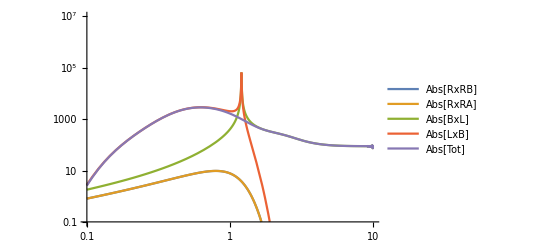

```mathematica
LogLogPlot[Evaluate[AllLines[{0.7,0.3,0.4,1-Exp[-ϵ],0.1,0.7}]],{ϵ,0.1,10.0},PlotRange->{0.1,10^7}, PlotLegends->AllLabels]
```

UV limit in k

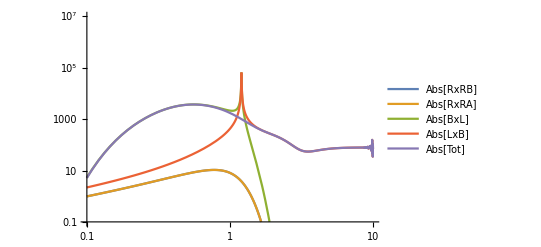

```mathematica
LogLogPlot[Evaluate[AllLines[{1-Exp[-ϵ],0.3,0.4,0.7,0.1,0.7}]],{ϵ,0.1,10.0},PlotRange->{0.1,10^7}, PlotLegends->AllLabels]
```

### IR limit

Then the IR limit

```mathematica
Manipulate[(((BxLIntegrandFunction[{
r,θ,ϕ,
0.4,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
LxBIntegrandFunction[{
r,θ,ϕ,
0.4,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]
)

/(RxRAIntegrandFunction[{
r,θ,ϕ,
0.4,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
RxRBIntegrandFunction[{
r,θ,ϕ,
0.4,θ+10^-ϵ,ϕ+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]
))),{{ϵ,3.},0.1,10.},{{r,0.3},0,1.},{{θ,0.1},0.,1},{{ϕ,0.3},0.,1}]
```

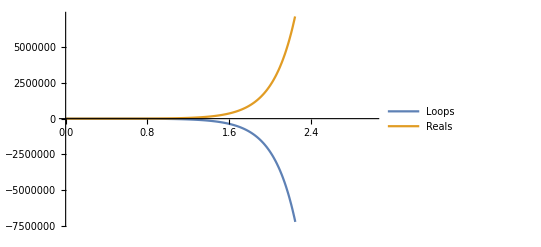

```mathematica
Plot[
{(BxLIntegrandFunction[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
LxBIntegrandFunction[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]
),
(RxRAIntegrandFunction[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
RxRBIntegrandFunction[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]
)},{ϵ,0.001,3.},PlotLegends->{"Loops","Reals"}
]
```

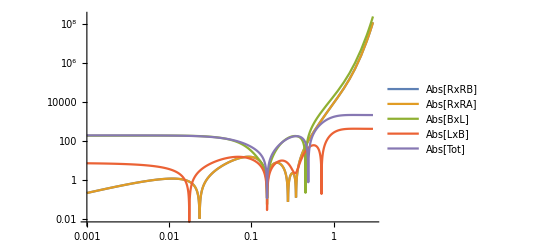

```mathematica
LogLogPlot[
Evaluate[AllLines[{
0.3,0.3,0.4,
0.1,0.3+10^-ϵ,0.4+10^-ϵ
}]],{ϵ,0.001,3.},PlotLegends->AllLabels
]
```

## Numerical integration

```mathematica
(* ThisIntegrand[x1,x2,x3,x4,x5,x6]=LxBIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
BxLIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
RxRAIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
RxRBIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False];
(*MCPoints={};*)
rBoundMin=0.001;rBoundMax=0.909;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOTriangleResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,AccuracyGoal->5,MaxPoints->statistics,MaxRecursion->10000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {10000,100000,500000,1000000,3000000,5000000,7000000,10000000,50000000,100000000,500000000,1000000000}}]
] *)
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 757.939 and 39.9229 for the integral and error estimates.

Result for 10000 sample points: 757.939

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 910.722 and 12.1939 for the integral and error estimates.

Result for 100000 sample points: 910.722

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 957.789 and 4.472 for the integral and error estimates.

Result for 500000 sample points: 957.789

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 951.787 and 2.94392 for the integral and error estimates.

Result for 1000000 sample points: 951.787

NIntegrate::maxp: The integral failed to converge after 3000100 integrand evaluations. NIntegrate obtained 985.49 and 1.42284 for the integral and error estimates.

Result for 3000000 sample points: 985.49

$Aborted

```mathematica
NLOTriangleResults0p01Boundary=<|10000->845.4004303717252,100000->879.4715339400847,500000->925.4408263870366,1000000->942.4793227334869,3000000->956.6029873462251,5000000->963.0694576240127,7000000->965.4487212248251,10000000->974.3858074871224,50000000->984.585542008315,100000000->985.8452258234571,500000000->993.8989860249346,1000000000->994.6674869973305|>;
```

```mathematica
(*NLOTriangleResults0p001Boundary=*)
```

```mathematica
FinalNLOTriangleResult = NLOTriangleResults0p01Boundary[Max[Keys[NLOTriangleResults0p01Boundary]]]
```

994.667

Finally reproducing α_s/π!

Compute the relative difference of the total NLO correction w.r.t to the target which is α_s/πBorn

Target result:

```mathematica
targetNLOResult=(((gs^2/(4π))/π)FinalLOResult)/.NumericalValues
```

290.792

NLO contribution from the triangle super graph:

```mathematica
FinalNLOTriangleResult
```

994.667

NLO contribution from one bubble graph (there are two):

```mathematica
FinalNLOBubbleResult
```

FinalNLOBubbleResult

Absolute difference between Final NLO result and target:

```mathematica
(FinalNLOTriangleResult+2*FinalNLOBubbleResult)-targetNLOResult
```

2 FinalNLOBubbleResult+703.875

Relative difference between Final NLO result and target:

```mathematica
MyPrint["Relative difference: "<>ToString[Abs[(((FinalNLOTriangleResult+2*FinalNLOBubbleResult)-targetNLOResult)/targetNLOResult)]*100.,InputForm]<>" %."];
```

Relative difference: 0.3438878574113566*Abs[703.8750154260513 + 2*FinalNLOBubbleResult] %.

One can also of course directly integrate all contributions at once:

```mathematica
(*ThisIntegrand[x1,x2,x3,x4,x5,x6]=LxBIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
BxLIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
RxRAIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
RxRBIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+2(
RBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]+
VBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False]);
(*MCPoints={};*)
rBoundMin=0.001;rBoundMax=0.999;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
AllNLOResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,AccuracyGoal->5,MaxPoints->statistics,MaxRecursion->10000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, { 10000,100000,500000,1000000,3000000,5000000,7000000,10000000,50000000,100000000,500000000,1000000000}}]
]*)
```

```mathematica
AllNLOResults0p001Boundary=<|10000->266.3279180198415,100000->189.80010631798697,500000->224.46257769782477,1000000->232.26211652496414,3000000->251.6080209740919,5000000->255.6637907734908,7000000->258.4061992689343,10000000->266.6870103226783,50000000->273.8477491890012,100000000->276.8124408548081,500000000->283.16369289028125,1000000000->284.6220710686282|>;
```

```mathematica
FinalNLOResult = AllNLOResults0p001Boundary[Max[Keys[AllNLOResults0p001Boundary]]]
```

284.622

```mathematica
MyPrint["Relative difference: "<>ToString[Abs[((FinalNLOResult-targetNLOResult)/targetNLOResult)]*100.,InputForm]<>" %."];
```

Relative difference: 2.121925808226583 %.

## Differential Next-to-Leading Order

## Testing cuts by comparing semi-inclusive cross-sections

### Semi-inclusive cross-section in Pt(j1) at Leading-Order

```mathematica
(*
ClearAll[ThisIntegrand,CutFunction];
(* Min pt(j1)=0.2, Max pt(j2)=0.8 *)
CutFunction=(NJ1PtCut2[0.2,0.8,0.4,##]&);
ThisIntegrand[x1,x2,x3]=LOIntegrandFunction[{x1,x2,x3},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,Cut->CutFunction];
(*MCPoints={};*)
rBoundMin=0.0+10^-5;rBoundMax=1.0-10^-5;
BoundMin=0.0+10^-5;BoundMax=1.0-10^-5;
IntermediateResult=0;
LOSemiInclusiveResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3},RealCutRescalingIntegrand[{x1,x2,x3},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics,{1000,5000,10000,50000,100000,500000,1000000}}]
]
*)
```

```mathematica
LOSemiInclusiveResults=<|1000->3974.013383847001,5000->3646.405799069494,10000->3592.6104018653814,50000->3604.0795114647767,100000->3594.5494071275302,500000->3607.912570605782,1000000->3607.0955492904245|>;
```

```mathematica
FinalLOSemiInclusiveResult = LOSemiInclusiveResults[Max[Keys[LOSemiInclusiveResults]]]
```

3607.1

Semi-inclusive cross-section (0.8>pt(j1)>0.2) :  ( 3.60697995e+03 +/- 1.88676908e-01 pb )

```mathematica
LOSemiInclusiveResultBenchmark=3607.0;
```

```mathematica
LOSemiInclusiveResultRelDiff=Abs[(FinalLOSemiInclusiveResult-LOSemiInclusiveResultBenchmark)/LOSemiInclusiveResultBenchmark];
```

```mathematica
MyPrint["Relative difference: "<>ToString[LOSemiInclusiveResultRelDiff*100,InputForm]<>"%"]
```

Relative difference: 0.002648996130427357%

### Semi-inclusive cross-section in Pt(j3) at Next-to-Leading-Order (which is LO really...)

First the bubble supergraph, we ignore the virtual contribution of course as it would yield no contribution

```mathematica
(*ClearAll[ThisIntegrand,CutFunction3];
(* Min pt(j3)=0.2, Max pt(j3)=0.8 *)
CutFunction3=(J3PtCut3[0.2,0.8,0.4,##]&);
ThisIntegrand[x1,x2,x3,x4,x5,x6]=RBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,False,Cut->CutFunction3];
(*+VBubbleIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,Cut->CutFunction2];*)
(*MCPoints={};*)
rBoundMin=0.0+10^-5;rBoundMax=1.0-10^-5;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOSemiInclusiveJ3BubbleResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {1000,10000,50000,100000}}]
]*)
```

```mathematica
NLOSemiInclusiveJ3BubbleResults=<|1000->158.740208271654,10000->126.09769908361994,50000->127.58177330902717,100000->134.54961393872588|>;
```

```mathematica
FinalNLOSemiInclusiveJ3BubbleResult = NLOSemiInclusiveJ3BubbleResults[Max[Keys[NLOSemiInclusiveJ3BubbleResults]]]
```

134.55

Then the double triangle supergraph, we ignore the virtual contribution of course as it would yield no contribution

```mathematica
(*ClearAll[ThisIntegrand,CutFunction];
(* Min pt(j3)=0.2, Max pt(j3)=0.8 *)
CutFunction3=(J3PtCut3[0.2,0.8,0.4,##]&);
ThisIntegrand[x1,x2,x3,x4,x5,x6]=(*LxBIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,Cut->CutFunction2]+
BxLIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,Cut->CutFunction2]+*)
RxRAIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,Cut->CutFunction3]+
RxRBIntegrandFunction[{x1,x2,x3,x4,x5,x6},{1.0,0.,0.,1.0},{1.0,0.,0.,-1.0},False,Cut->CutFunction3];
(*MCPoints={};*)
rBoundMin=0.0+10^-5;rBoundMax=1.0-10^-5;
BoundMin=0.0;BoundMax=1.0;
IntermediateResult=0;
NLOSemiInclusiveJ3TriangleResults=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,AccuracyGoal->5,MaxPoints->statistics,MaxRecursion->10000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult
,{statistics, {1000,10000,50000,100000}}]
]*)
```

```mathematica
NLOSemiInclusiveJ3TriangleResults=<|1000->383.18597740201994,10000->726.0413312061487,50000->820.7454322454215,100000->850.7915798163485|>;
```

```mathematica
FinalNLOSemiInclusiveJ3TriangleResult = NLOSemiInclusiveJ3TriangleResults[Max[Keys[NLOSemiInclusiveJ3TriangleResults]]]
```

850.792

Semi-inclusive cross-section (0.8>pt(j3)>0.2) :  (  2.02618357e+03 +/- 1.28315800e-01 pb )

```mathematica
NLOSemiInclusiveJ3ResultBenchmark=2026.0;
```

```mathematica
NLOSemiInclusiveJ3ResultRelDiff=Abs[(NLOSemiInclusiveJ3ResultBenchmark-FinalNLOSemiInclusiveJ3TriangleResult-2FinalNLOSemiInclusiveJ3BubbleResult)/NLOSemiInclusiveJ3ResultBenchmark];
```

```mathematica
MyPrint["Relative difference: "<>ToString[NLOSemiInclusiveJ3ResultRelDiff*100,InputForm]<>"%"]
```

Relative difference: 44.72404700425467%

## Laying out the problem

The problem for differential Next-to-Leading Order is that our above procedure does not realise unitarity locally.
I will illustrate what this imply with a specific example that is problematic when computing a semi-inclusive cross-section, for example in the transverse momentum of the first pT-ordered jet:

First take the following particular configuration that appears in the computation of the inclusive cross-section.

The xs-configuration below corresponds to a momentum in k that is ϵk away from the E-surface of the k-triangle and a momentum in l which will be ϵl aways fromt he E-surface of the l-triangle.

```mathematica
EsurfaceCancelingXs[ϵk_,ϵl_]:=N[Join[{1/2,1/2+0.01,1/8}+10^-ϵk{1,1,1},{1/2,0+0.01,1}-10^-ϵl{1,1,1}],16]
```

Let us investigate the loop momenta k⃗ and l⃗induced by the above x coordinates in the unit hypercube. In particular, let us look at the transverse momentum of these:

```mathematica
Block[{vec,vec4},
vec=(SphericalMap@@(EsurfaceCancelingXs[10,10]⟦4;;6⟧))["vector"];
vec4={0,vec⟦1⟧,vec⟦2⟧,vec⟦3⟧};
MyPrint["K three-vector:"<>ToString[vec,InputForm]];
MyPrint["pT(K):"<>ToString[ObsPT[vec4],InputForm]];
vec=(SphericalMap@@(EsurfaceCancelingXs[10,10]⟦1;;3⟧))["vector"];
vec4={0,vec⟦1⟧,vec⟦2⟧,vec⟦3⟧};
MyPrint["L three-vector:"<>ToString[vec,InputForm]];
MyPrint["pT(L):"<>ToString[ObsPT[vec4],InputForm]];
]
```

K three-vector:{0.03141075875155974, -1.973596178751628*^-11, 0.9995065599757968}

pT(K):0.03141075875155974

L three-vector:{0.7067578665067065, 0.7067578673948447, -0.031410759404696925}

pT(L):0.9995065607556662

It is thus clear that a cut considering the transverse momentum could allow for the event when evaluated on K but reject it when evaluated on L!

This is a problem, because we can see below that we face a large cancellation between the BxLIntegrandFunction and LxBIntegrandFunction for this single configuration that lies very close to the E-surface!

```mathematica
BxLIntegrandFunction[EsurfaceCancelingXs[6,6],{1,0,0,-1},{1,0,0,1},False,Cut->NoCutFunction]
```

-9.40529×10^6

```mathematica
LxBIntegrandFunction[EsurfaceCancelingXs[6,6],{1,0,0,-1},{1,0,0,1},False,Cut->NoCutFunction]
```

9.40543×10^6

Now however, putting a cut function like on the first jet pt, we can see the mis-cancellation at play

```mathematica
BxLIntegrandFunction[EsurfaceCancelingXs[6,6],{1,0,0,-1},{1,0,0,1},False,Cut->(J1PtCut2[0.2,1.0,0.4,##]&)]
```

-9.40529×10^6

```mathematica
LxBIntegrandFunction[EsurfaceCancelingXs[6,6],{1,0,0,-1},{1,0,0,1},False,Cut->(J1PtCut2[0.2,1.0,0.4,##]&)]
```

0.

And that, my friend, is the miscancellation of E-surfaces in the presence of observables!

What one can attempt now is simply  to symmetrize the complex-conjugate and non-complex conjugate quantities by including with each Cutkosky contribution term a complex conjugate copy of it with a factor one half!
This complex conjugate can be emulated quite simply In the case of this symmetric double-triangle by reusing the same Cutkosky cut implementation but with k and l swapped (in general however this copy will need to be build explicitly as if would correspond to one appearing in another squared graph with possibly a different momentum routing)! We get:

```mathematica
SwapKL[xs_]:=Join[xs⟦4;;6⟧,xs⟦1;;3⟧];
```

In the absence of the cuts, out two original expressions for the two Cutkosky contributions featuring a triangle are:

```mathematica
{BxLIntegrandFunction[EsurfaceCancelingXs[6,6],{1,0,0,-1},{1,0,0,1},False,Cut->NoCutFunction(*(J1PtCut2[0.2,1.0,0.4,##]&)*)],
LxBIntegrandFunction[EsurfaceCancelingXs[6,6],{1,0,0,-1},{1,0,0,1},False,Cut->NoCutFunction(*(J1PtCut2[0.2,1.0,0.4,##]&)*)]}
```

{-9.40529×10^6,9.40543×10^6}

And their complex conjugate can be built as follows then:

```mathematica
{LxBIntegrandFunction[SwapKL[EsurfaceCancelingXs[6,6]],{1,0,0,-1},{1,0,0,1},False,Cut->NoCutFunction(*(J1PtCut2[0.2,1.0,0.4,##]&)*)],
BxLIntegrandFunction[SwapKL[EsurfaceCancelingXs[6,6]],{1,0,0,-1},{1,0,0,1},False,Cut->NoCutFunction(*(J1PtCut2[0.2,1.0,0.4,##]&)*)]}
```

{-9.40529×10^6,9.40543×10^6}

Which unsurprisingly yield the same real part but would have an opposite imaginary part, thus rendering the above combination real, as observables out to be.

The surprising characteristic of the above procedure is that it seems irrelevant to follow the causal prescription of E-surfaces. Indeed, as long as the opposite prescription (locally on any E-surface) is followed in the complex-conjugate counterpart, one should get the same result after integration for the surviving real part irrespectively of whether the deformation followed the causal prescription. 
This is what we will test directly using our Rust implementation.

## Semi-inclusive cross-section in Pt(j1) at Next-to-Leading-Order

TODO